# Bosonic Complexity of Purification (BCoP)

IMPORTANT: Please read the instructions/advice carefully before running the file.

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

First step: Import the GaussianOptimization Package (Run):

```mathematica
Import["/Users/HugoCamargo89/Desktop/gaussian_purifications/Mathematica Code/GaussianOptimization.m"]
```

```mathematica
(*<<GaussianOptimization`*)
```

In this Mathematica notebook we use the optimization procedure to find the complexity of purification for two bosonic systems. The first system, studied in the first Chapter is a lattice free scalar field theory with periodic conditions. This Chapter is called Bosons on a Periodic Lattice.
 
The second system, studied in the second Chapter, as a free scalar field theory undergoing a smooth quench through a critical point. This Chapter is called Bosons under a Smooth Quench Through a Critical Point.

## Chapter 1: Bosons on a Periodic Lattice

In this Chapter of the Mathematica notebook, we use the optimization procedure to find the complexity of purification CoP for a bosonic system on a periodic lattice. The SubChapter: Definitions, should be run at the beginning, as it has the necessary field-theoretic definitions for the physical system in question.

This part of the notebook is divided into  four scenarios. Each one of these is also divided into several sections, each one with a number of subsections. These are organized as follows:

1. In Scenario 1 we look at bosonic complexity of purification BCoP, as a function of lattice separation d between subsystems with fixed total number of sites N for a scalar field mass of m=1/10 with variable subsystem sizes dim1 and dim2.

2. In Scenario 2 we look at BCoP, as a function of subsystem size dim1 dim2 with fixed d=0 lattice separation between subsystems for a scalar field mass of m=1/10 with variable N.

3. In Scenario 3 we look at BCoP, as a function of subsystem size dim1 dim2 with variable lattice separation d between subsystems for a scalar field mass of m=1/10 with variable N.

4. In Scenario 4 we look at BCoP, as a function of total number of lattice sites N with fixed subsystem size dim1 dim2 for a scalar field mass of m=1/10 with variable subsystem separation d.

In each Scenario, there are several Cases that are studied individually, where the rest of the parameters is varied. Each Case is divided into Subcases. At the end of each Case, a Summary for the Case contains the relevant outcome of the numerical optimization for the given Case. Atfter all the cases have been studied for a given Scenario, a Summary for the Scenario is presented, with the relevant information for the setup.

IMPORTANT: At the moment of writing this sentence (04.09.19 - 13:21), Scenario 1 is being studied. Scenarios 2, 3, 4 are pending.

Definitions (Run)

The following definitions are equivalent to the ones used in Michal and Lucas’ recent work on complexity for the thermofield double theory. The parameters of the theory are the following:

1. Total number of lattice sites: N,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: l,
4. Dimension of subsystems on the lattice: dim1 & dim2,
5. Lattice Site Separation between the subsystems: d,
6. Total length of the circle: L==(N-1)l .

The relevant quantities that are calculated from these parameters are the full covariance matrix of the vacuum state of the theory (assuming a small mass m) CM[N,m,l], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) partialCM[N,m,l,d,dim1,dim2].

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

Scenario 1: BCoP as a Function of Subsystem Partition Separation (Fixed Bipartite Subsystem Size) with m=1/10:

In this Scenario, we look at bosonic complexity of purification BCoP, as a function of lattice separation d between subsystems with fixed total number of sites N for a scalar field mass of m=1/10 with variable subsystem sizes dim1 and dim2. This scenario is interesting, as it will tell us about the behaviour of complexity of purification in the case where the subsystem in a mixed state is comprised of two regions in the lattice. By varying the separation between the regions that make up the subsystem, we can study the effect that separating the subregions has on the complexity of the purified state.

This Scenario consists of 5 Cases. The difference between the Cases studied is the total length L of the periodic lattice.

1. Case 1: N=100, m=1/10, δ=1 ;  ( N-1)δ == L=99

2. Case 2: N=100, m=1/10, δ=1/10;  (N-1)δ == L=9.9

3. Case 3: N=10, m=1/10, δ=1 ;  (N-1)δ == L=9

4. Case 4: N=10, m=1/10, δ=1/10 ; (N-1)δ == L=0.9

5. Case 5: N=300, m=1/10, δ=1 ; (N-1)δ == L=299

Each Case is followed by Subcases, where the dimension of the subsystem regions dim1 = dim2 is varied. Each Subcase has then several SubSubCases, where BCoP is calculated for a given subsystem region separation d. At the end of the last SubSubCase, a Summary section for the SubCase is presented, which contains the result of the optimization for BCoP as a function of subsystem separation: BCoP[d].

IMPORTANT: At the moment of writing this sentence (04.09.19 - 13:21), only Case 1 is being studied. Cases 2,3,4,5 are pending.

IMPORTANT (04.09.19 - 13:21): SubCases 1.1. , 1.2 , and 1.3 where studied a previous version of the Optimization Algorithm, which does not take into account the newest specifications (according to the .m file from 30.08.19). SubCase 1.4 is being studied with the most recent function definitions.

IMPORTANT (04.09.19 - 13:21): Results for SubCases 1.1, 1.2, and 1.3 can be found in a subsection within each section called Summary.

## Case 1: N=100, m=1/10, δ=1 ; (N-1)δ == L=99

### SubCase 1.1: N=100, m=1/10, δ=1, dimS=1 (No need to run. See relevant info. in Subsubsection Summary Case 1.1.)

#### Case 1.1.1: N=100, m=1/10, δ=1, dimS=1, l=0

```mathematica
CM0=partialCM[100,1/10,1,0,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0
0 | 1.39418 | 0 | 0.760649
-0.41982 | 0 | 1.28101 | 0
0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.413685,0.137482},{{0.,0.56222,0.,0.56222},{-0.889332,0.,-0.889332,0.},{0.552411,0.,-0.552411,0.},{0.,0.905123,0.,-0.905123}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.707459

Number of iterations: 8

Number of total corrections: 0

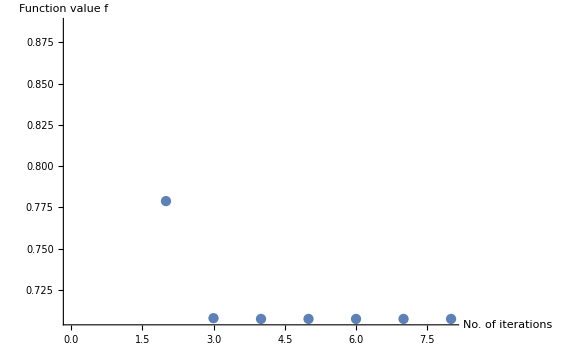

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.707459

#### Case 1.1.2: N=100, m=1/10, δ=1, dimS=1, l=1

```mathematica
CM0=partialCM[100,1/10,1,1,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0813337 | 0
0 | 1.39418 | 0 | 0.554542
-0.0813337 | 0 | 1.28101 | 0
0 | 0.554542 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.493961,0.185378},{{0.,0.626344,0.,0.626344},{-0.798283,0.,-0.798283,0.},{0.626523,0.,-0.626523,0.},{0.,0.798056,0.,-0.798056}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.767223

Number of iterations: 10

Number of total corrections: 0

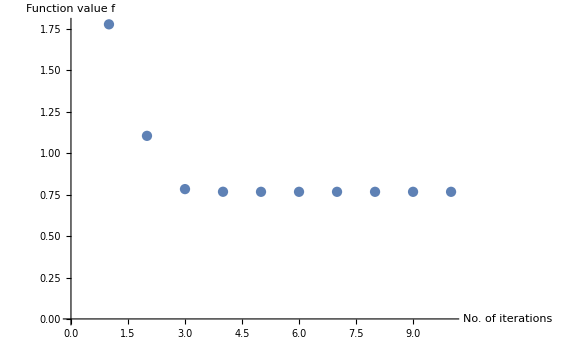

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.767223

#### Case 1.1.3: N=100, m=1/10, δ=1, dimS=1, l=2

```mathematica
CM0=partialCM[100,1/10,1,2,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0334432 | 0
0 | 1.39418 | 0 | 0.435315
-0.0334432 | 0 | 1.28101 | 0
0 | 0.435315 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.485996,0.245193},{{0.,0.642566,0.,0.642566},{-0.77813,0.,-0.77813,0.},{0.653489,0.,-0.653489,0.},{0.,0.765123,0.,-0.765123}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.780635

Number of iterations: 9

Number of total corrections: 0

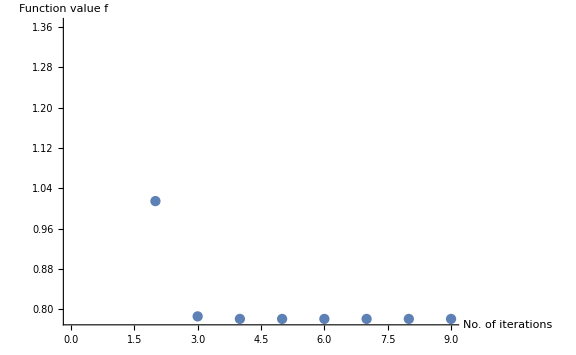

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.780635

#### Case 1.1.4: N=100, m=1/10, δ=1, dimS=1, l=3

```mathematica
CM0=partialCM[100,1/10,1,3,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0177027 | 0
0 | 1.39418 | 0 | 0.353884
-0.0177027 | 0 | 1.28101 | 0
0 | 0.353884 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.47492,0.281188},{{0.,0.651963,0.,0.651963},{-0.766915,0.,-0.766915,0.},{0.668954,0.,-0.668954,0.},{0.,0.747435,0.,-0.747435}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.787262

Number of iterations: 9

Number of total corrections: 0

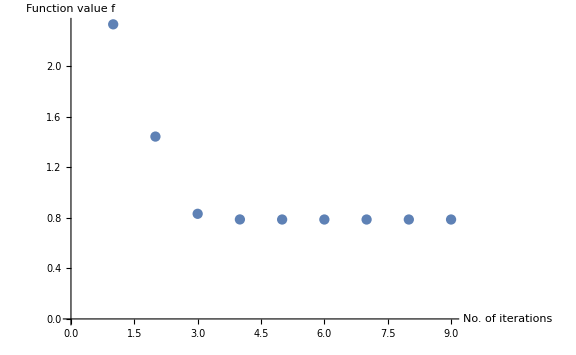

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.787262

#### Case 1.1.5: N=100, m=1/10, δ=1, dimS=1, l=4

```mathematica
CM0=partialCM[100,1/10,1,4,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.293694
-0.0106767 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.46489,0.305284},{{0.,0.658611,0.,0.658611},{-0.759173,0.,-0.759173,0.},{-0.679348,0.,0.679348,0.},{0.,-0.736,0.,0.736}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.79114

Number of iterations: 9

Number of total corrections: 0

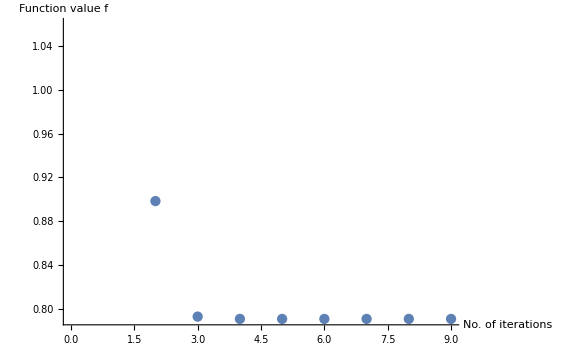

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.79114

#### Case 1.1.6: N=100, m=1/10, δ=1, dimS=1, l=5

```mathematica
CM0=partialCM[100,1/10,1,5,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.00697557 | 0
0 | 1.39418 | 0 | 0.247118
-0.00697557 | 0 | 1.28101 | 0
0 | 0.247118 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.456261,0.322614},{{0.,-0.663717,0.,-0.663717},{0.753333,0.,0.753333,0.},{-0.686917,0.,0.686917,0.},{0.,-0.72789,0.,0.72789}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.793601

Number of iterations: 10

Number of total corrections: 0

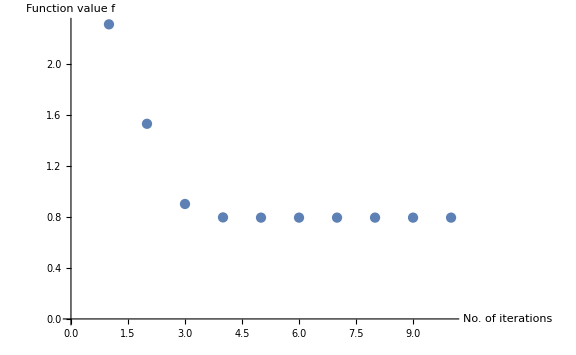

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.793601

#### Case 1.1.7: N=100, m=1/10, δ=1, dimS=1, l=10

```mathematica
CM0=partialCM[100,1/10,1,10,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0014811 | 0
0 | 1.39418 | 0 | 0.116311
-0.0014811 | 0 | 1.28101 | 0
0 | 0.116311 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.428481,0.366055},{{0.,0.678372,0.,0.678372},{-0.737059,0.,-0.737059,0.},{-0.706469,0.,0.706469,0.},{0.,-0.707745,0.,0.707745}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.798164

Number of iterations: 9

Number of total corrections: 0

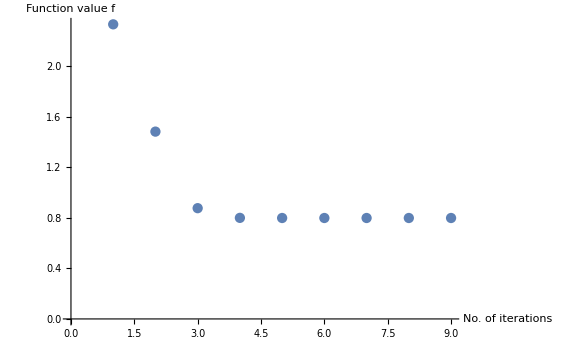

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.798164

#### Case 1.1.8: N=100, m=1/10, δ=1, dimS=1, l=15

```mathematica
CM0=partialCM[100,1/10,1,15,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.000480174 | 0
0 | 1.39418 | 0 | 0.0598408
-0.000480174 | 0 | 1.28101 | 0
0 | 0.0598408 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.414912,0.382787},{{0.,0.684998,0.,0.684998},{-0.729929,0.,-0.729929,0.},{0.,-0.699998,0.,0.699998},{0.714288,0.,-0.714288,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799105

Number of iterations: 8

Number of total corrections: 0

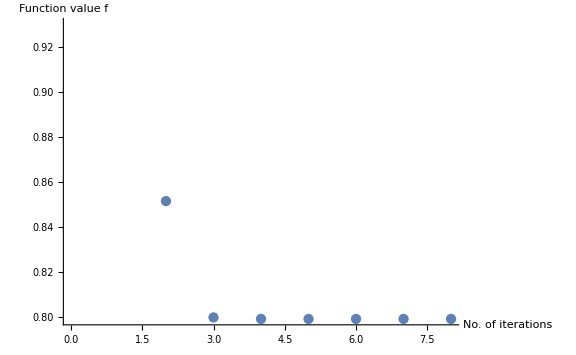

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799105

#### Case 1.1.9: N=100, m=1/10, δ=1, dimS=1, l=20

```mathematica
CM0=partialCM[100,1/10,1,20,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.00018661 | 0
0 | 1.39418 | 0 | 0.0321328
-0.00018661 | 0 | 1.28101 | 0
0 | 0.0321328 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.407887,0.390617},{{0.,0.68834,0.,0.68834},{-0.726385,0.,-0.726385,0.},{0.,-0.696371,0.,0.696371},{0.718008,0.,-0.718008,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799346

Number of iterations: 8

Number of total corrections: 0

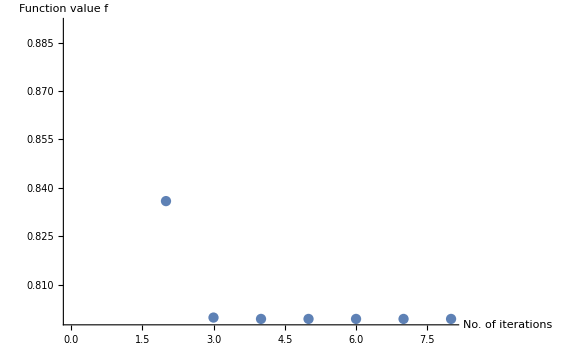

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799346

#### Case 1.1.10: N=100, m=1/10, δ=1, dimS=1, l=30

```mathematica
CM0=partialCM[100,1/10,1,30,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0000369176 | 0
0 | 1.39418 | 0 | 0.0100091
-0.0000369176 | 0 | 1.28101 | 0
0 | 0.0100091 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.402094,0.396705},{{0.,-0.691056,0.,-0.691056},{0.72353,0.,0.72353,0.},{0.,-0.693551,0.,0.693551},{0.720927,0.,-0.720927,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799434

Number of iterations: 10

Number of total corrections: 0

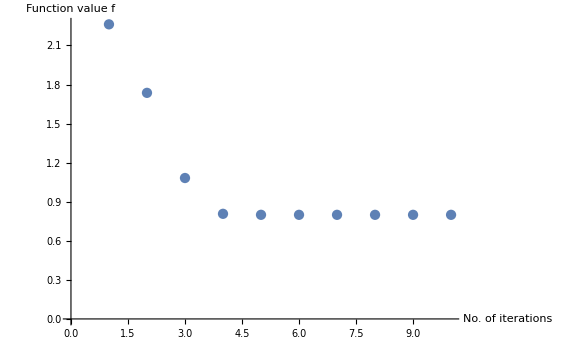

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799434

#### Case 1.1.11: N=100, m=1/10, δ=1, dimS=1, l=45

```mathematica
CM0=partialCM[100,1/10,1,45,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.9252×10^-6 | 0
0 | 1.39418 | 0 | 0.00258647
-5.9252×10^-6 | 0 | 1.28101 | 0
0 | 0.00258647 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400112,0.398717},{{0.,-0.691976,0.,-0.691976},{0.722568,0.,0.722568,0.},{0.,-0.69262,0.,0.69262},{0.721896,0.,-0.721896,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799442

Number of iterations: 9

Number of total corrections: 0

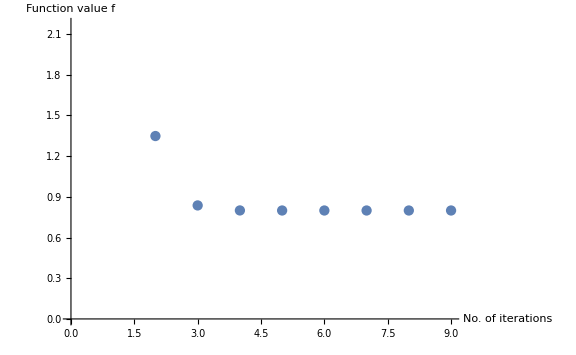

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799442

#### Case 1.1.12: N=100, m=1/10, δ=1, dimS=1, l=46

```mathematica
CM0=partialCM[100,1/10,1,46,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.58759×10^-6 | 0
0 | 1.39418 | 0 | 0.00248335
-5.58759×10^-6 | 0 | 1.28101 | 0
0 | 0.00248335 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400084,0.398745},{{0.,0.691989,0.,0.691989},{-0.722555,0.,-0.722555,0.},{0.,-0.692607,0.,0.692607},{0.72191,0.,-0.72191,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799442

Number of iterations: 9

Number of total corrections: 1

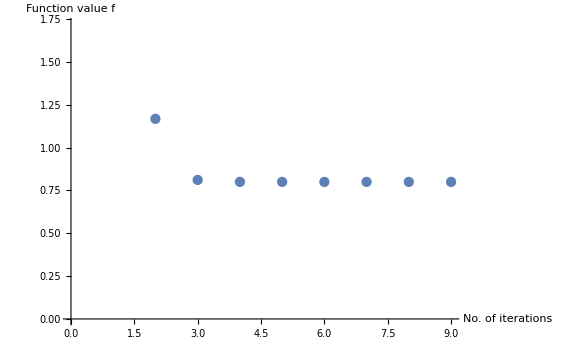

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799442

#### Case 1.1.13: N=100, m=1/10, δ=1, dimS=1, l=47

```mathematica
CM0=partialCM[100,1/10,1,47,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.35149×10^-6 | 0
0 | 1.39418 | 0 | 0.00241066
-5.35149×10^-6 | 0 | 1.28101 | 0
0 | 0.00241066 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400064,0.398764},{{0.,0.691998,0.,0.691998},{-0.722545,0.,-0.722545,0.},{0.,-0.692598,0.,0.692598},{0.721919,0.,-0.721919,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799442

Number of iterations: 7

Number of total corrections: 0

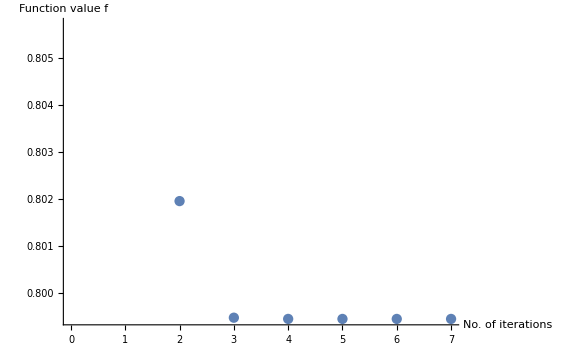

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799442

#### Case 1.1.14: N=100, m=1/10, δ=1, dimS=1, l=48

```mathematica
CM0=partialCM[100,1/10,1,48,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.21181×10^-6 | 0
0 | 1.39418 | 0 | 0.00236743
-5.21181×10^-6 | 0 | 1.28101 | 0
0 | 0.00236743 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400053,0.398776},{{0.,0.692004,0.,0.692004},{-0.722539,0.,-0.722539,0.},{0.,-0.692593,0.,0.692593},{0.721925,0.,-0.721925,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799443

Number of iterations: 9

Number of total corrections: 1

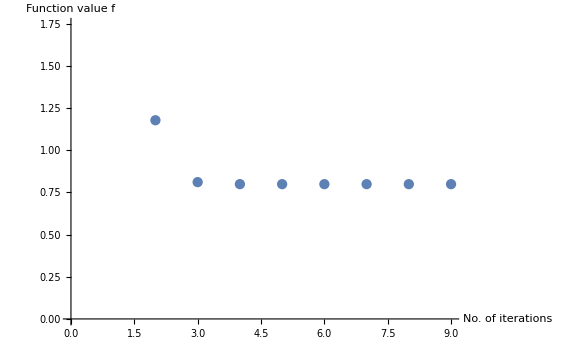

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799443

#### Case 1.1.15: N=100, m=1/10, δ=1, dimS=1, l=49

```mathematica
CM0=partialCM[100,1/10,1,49,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.16558×10^-6 | 0
0 | 1.39418 | 0 | 0.00235308
-5.16558×10^-6 | 0 | 1.28101 | 0
0 | 0.00235308 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400049,0.39878},{{0.,0.692006,0.,0.692006},{-0.722538,0.,-0.722538,0.},{0.,-0.692591,0.,0.692591},{0.721927,0.,-0.721927,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799443

Number of iterations: 8

Number of total corrections: 0

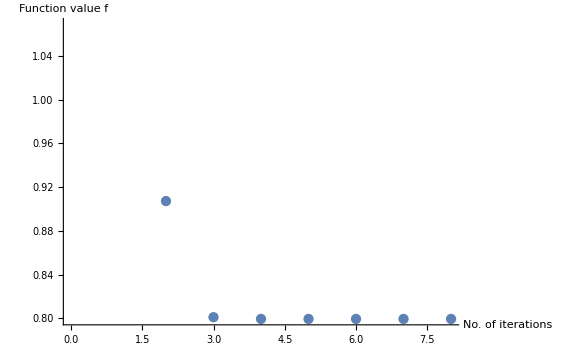

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799443

#### Summary Case 1.1

```mathematica
listCase11={{0,0.7074591735168936},{1,0.7672233438804287},{2,0.7806345878621787},{3,0.7872619247999597},{4,0.7911400250356868},{5,0.7936011522537301},{10,0.7981635927445374},{15,0.7991053475076283},{20,0.7993457814692719},{30,0.7994336154396451},{45,0.799442414994183},{46,0.7994424641780215},{47,0.7994424976489363},{48,0.799442517083822},{49,0.7994425234562166}};
```

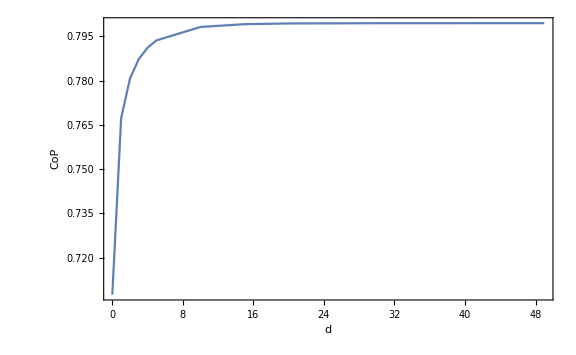

```mathematica
ListPlot[listCase11,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

In this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

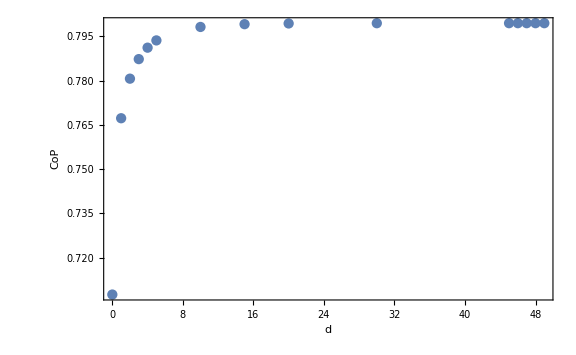
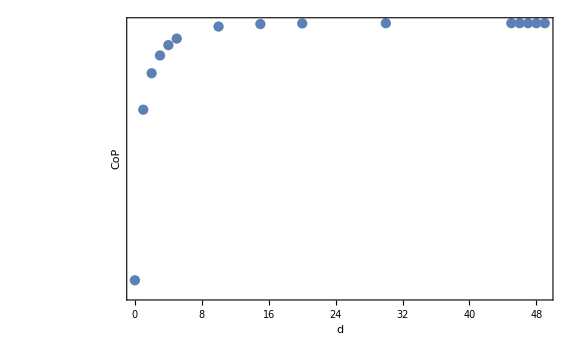

```mathematica
PlotlistCase11=Row[{ListPlot[listCase11,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[listCase11,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotlistCase11.pdf",PlotlistCase11];
```

### SubCase 1.2: N=100, m=1/10, δ=1, dimS=2 (No need to run. See relevant info. in Subsubsection Summary Case 1.2.)

#### Case 1.2.1: N=100, m=1/10, δ=1, dimS=2, l=0

```mathematica
CM0=partialCM[100,1/10,1,0,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.406088,0.215895,0.0215537,0.00399736},{{0.,-0.473851,0.,-0.164523,0.,-0.164523,0.,-0.473851},{0.803418,0.,0.725127,0.,0.725127,0.,0.803418,0.},{-0.65825,0.,-0.195085,0.,0.195085,0.,0.65825,0.},{0.,-0.73008,0.,-0.0995702,0.,0.0995702,0.,0.73008},{0.210653,0.,-0.606712,0.,-0.606712,0.,0.210653,0.},{0.,0.566334,0.,-0.62748,0.,-0.62748,0.,0.566334},{0.0715321,0.,-0.524496,0.,0.524496,0.,-0.0715321,0.},{0.,0.271552,0.,-0.916261,0.,0.916261,0.,-0.271552}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.890738

Number of iterations: 10

Number of total corrections: 0

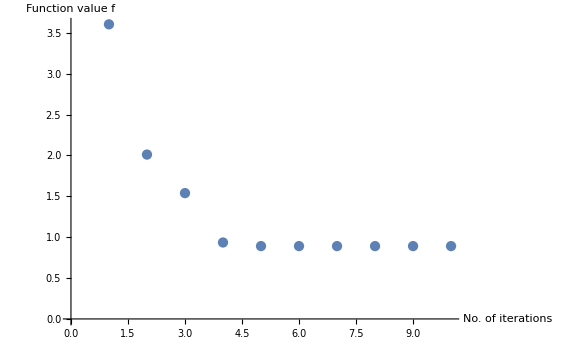

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.890738

#### Case 1.2.2: N=100, m=1/10, δ=1, dimS=2, l=1

```mathematica
CM0=partialCM[100,1/10,1,1,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.435315 | 0 | 0.353884
-0.41982 | 0 | 1.28101 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 1.39418 | 0 | 0.760649
-0.0177027 | 0 | -0.0334432 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.498362,0.237597,0.150009,0.00695197},{{0.,0.334637,0.,0.374853,0.,0.374853,0.,0.334637},{-0.671292,0.,-0.734583,0.,-0.734583,0.,-0.671292,0.},{-0.67583,0.,-0.294457,0.,0.294457,0.,0.67583,0.},{0.,-0.685117,0.,-0.125579,0.,0.125579,0.,0.685117},{-0.415423,0.,0.370854,0.,0.370854,0.,-0.415423,0.},{0.,-0.662845,0.,0.605734,0.,0.605734,0.,-0.662845},{0.10419,0.,-0.568427,0.,0.568427,0.,-0.10419,0.},{0.,0.354905,0.,-0.814569,0.,0.814569,0.,-0.354905}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.956594

Number of iterations: 9

Number of total corrections: 0

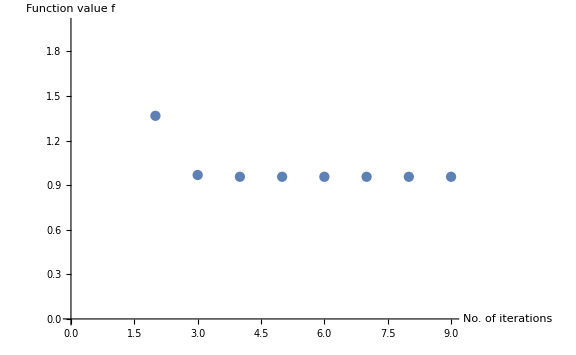

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.956594

#### Case 1.2.3: N=100, m=1/10, δ=1, dimS=2, l=2

```mathematica
CM0=partialCM[100,1/10,1,2,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.435315 | 0 | 0.353884
-0.0177027 | 0 | -0.0334432 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.497468,0.26826,0.146622,0.0970826},{{0.,-0.339803,0.,-0.390006,0.,-0.390006,0.,-0.339803},{0.655902,0.,0.71056,0.,0.71056,0.,0.655902,0.},{0.,0.596893,0.,0.250308,0.,-0.250308,0.,-0.596893},{-0.661218,0.,-0.420779,0.,0.420779,0.,0.661218,0.},{0.418406,0.,-0.364547,0.,-0.364547,0.,0.418406,0.},{0.,0.66233,0.,-0.611382,0.,-0.611382,0.,0.66233},{-0.218365,0.,0.520722,0.,-0.520722,0.,0.218365,0.},{0.,-0.48233,0.,0.75794,0.,-0.75794,0.,0.48233}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.973802

Number of iterations: 10

Number of total corrections: 0

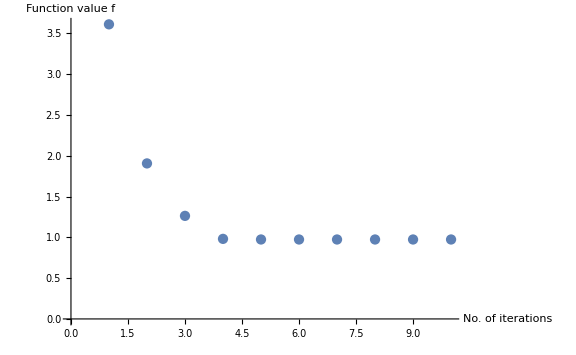

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.973802

#### Case 1.2.4: N=100, m=1/10, δ=1, dimS=2, l=3

```mathematica
CM0=partialCM[100,1/10,1,3,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.293694 | 0 | 0.247118
-0.41982 | 0 | 1.28101 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.353884 | 0 | 0.293694
-0.0106767 | 0 | -0.0177027 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 1.39418 | 0 | 0.760649
-0.00697557 | 0 | -0.0106767 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.489482,0.295129,0.143934,0.116778},{{0.,-0.347893,0.,-0.394144,0.,-0.394144,0.,-0.347893},{0.649608,0.,0.695193,0.,0.695193,0.,0.649608,0.},{0.,-0.533833,0.,-0.317167,0.,0.317167,0.,0.533833},{0.644815,0.,0.491151,0.,-0.491151,0.,-0.644815,0.},{-0.415419,0.,0.366671,0.,0.366671,0.,-0.415419,0.},{0.,-0.659589,0.,0.61634,0.,0.61634,0.,-0.659589},{0.28455,0.,-0.478935,0.,0.478935,0.,-0.28455,0.},{0.,0.547449,0.,-0.718727,0.,0.718727,0.,-0.547449}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.982673

Number of iterations: 9

Number of total corrections: 1

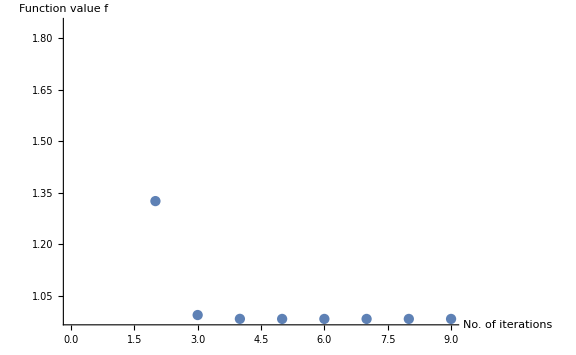

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.982673

#### Case 1.2.5: N=100, m=1/10, δ=1, dimS=2, l=4

```mathematica
CM0=partialCM[100,1/10,1,4,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.247118 | 0 | 0.209989
-0.41982 | 0 | 1.28101 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.293694 | 0 | 0.247118
-0.00697557 | 0 | -0.0106767 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 1.39418 | 0 | 0.760649
-0.0048107 | 0 | -0.00697557 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.480922,0.316223,0.142229,0.125062},{{0.,0.35492,0.,0.395822,0.,0.395822,0.,0.35492},{-0.645779,0.,-0.684146,0.,-0.684146,0.,-0.645779,0.},{0.,0.495248,0.,0.350071,0.,-0.350071,0.,-0.495248},{-0.634962,0.,-0.529997,0.,0.529997,0.,0.634962,0.},{-0.412178,0.,0.369586,0.,0.369586,0.,-0.412178,0.},{0.,-0.656998,0.,0.620153,0.,0.620153,0.,-0.656998},{0.319912,0.,-0.452583,0.,0.452583,0.,-0.319912,0.},{0.,0.579959,0.,-0.69482,0.,0.69482,0.,-0.579959}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.987995

Number of iterations: 9

Number of total corrections: 0

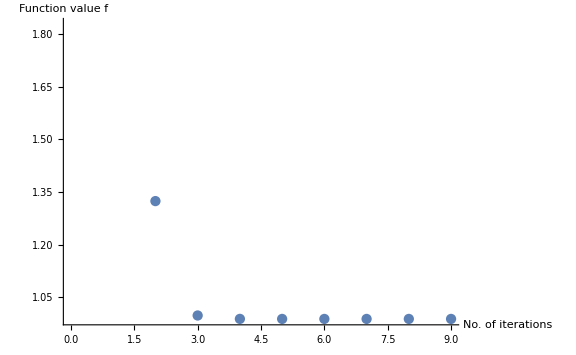

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.987995

#### Case 1.2.6: N=100, m=1/10, δ=1, dimS=2, l=5

```mathematica
CM0=partialCM[100,1/10,1,5,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0048107 | 0 | -0.00344953 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.209989 | 0 | 0.179771
-0.41982 | 0 | 1.28101 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.247118 | 0 | 0.209989
-0.0048107 | 0 | -0.00697557 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 1.39418 | 0 | 0.760649
-0.00344953 | 0 | -0.0048107 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.179771 | 0 | 0.209989 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.472988,0.332629,0.141112,0.129291},{{0.,0.360775,0.,0.396659,0.,0.396659,0.,0.360775},{-0.643032,0.,-0.67567,0.,-0.67567,0.,-0.643032,0.},{0.,0.470868,0.,0.367524,0.,-0.367524,0.,-0.470868},{-0.62966,0.,-0.553741,0.,0.553741,0.,0.62966,0.},{0.409321,0.,-0.372291,0.,-0.372291,0.,0.409321,0.},{0.,0.654768,0.,-0.62314,0.,-0.62314,0.,0.654768},{0.340329,0.,-0.436026,0.,0.436026,0.,-0.340329,0.},{0.,0.59799,0.,-0.679974,0.,0.679974,0.,-0.59799}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.991432

Number of iterations: 10

Number of total corrections: 0

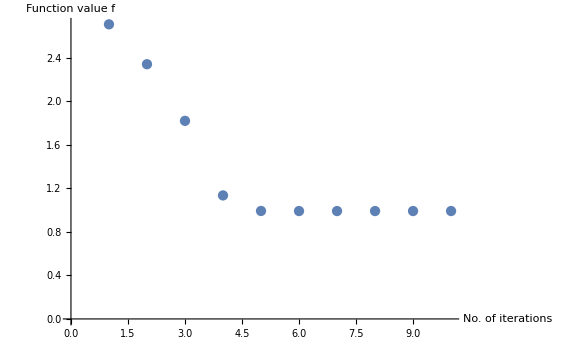

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.991432

#### Case 1.2.7: N=100, m=1/10, δ=1, dimS=2, l=8

```mathematica
CM0=partialCM[100,1/10,1,8,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.133923 | 0 | 0.116311
-0.41982 | 0 | 1.28101 | 0 | -0.00254724 | 0 | -0.00192459 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.154799 | 0 | 0.133923
-0.00192459 | 0 | -0.00254724 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.133923 | 0 | 0.154799 | 0 | 1.39418 | 0 | 0.760649
-0.0014811 | 0 | -0.00192459 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.454211,0.36437,0.139371,0.134277},{{0.,0.373308,0.,0.397579,0.,0.397579,0.,0.373308},{-0.637782,0.,-0.658764,0.,-0.658764,0.,-0.637782,0.},{0.,0.434527,0.,0.387706,0.,-0.387706,0.,-0.434527},{-0.624861,0.,-0.589315,0.,0.589315,0.,0.624861,0.},{0.403023,0.,-0.37842,0.,-0.37842,0.,0.403023,0.},{0.,0.649865,0.,-0.629167,0.,-0.629167,0.,0.649865},{0.367738,0.,-0.412147,0.,0.412147,0.,-0.367738,0.},{0.,0.621315,0.,-0.65879,0.,0.65879,0.,-0.621315}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.996523

Number of iterations: 9

Number of total corrections: 0

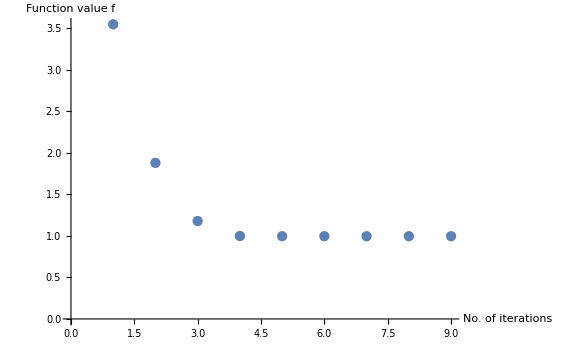

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.996523

#### Case 1.2.8: N=100, m=1/10, δ=1, dimS=2, l=10

```mathematica
CM0=partialCM[100,1/10,1,10,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.101343 | 0 | 0.0885453
-0.41982 | 0 | 1.28101 | 0 | -0.0014811 | 0 | -0.00115709 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.116311 | 0 | 0.101343
-0.00115709 | 0 | -0.0014811 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.101343 | 0 | 0.116311 | 0 | 1.39418 | 0 | 0.760649
-0.000915362 | 0 | -0.00115709 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.445226,0.377118,0.1388,0.135503},{{0.,-0.378918,0.,-0.397744,0.,-0.397744,0.,-0.378918},{0.635602,0.,0.651571,0.,0.651571,0.,0.635602,0.},{0.,0.423069,0.,0.392225,0.,-0.392225,0.,-0.423069},{-0.624699,0.,-0.600954,0.,0.600954,0.,0.624699,0.},{0.400168,0.,-0.381227,0.,-0.381227,0.,0.400168,0.},{0.,0.647625,0.,-0.631753,0.,-0.631753,0.,0.647625},{-0.375494,0.,0.405023,0.,-0.405023,0.,0.375494,0.},{0.,-0.62773,0.,0.652533,0.,-0.652533,0.,0.62773}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.99797

Number of iterations: 7

Number of total corrections: 0

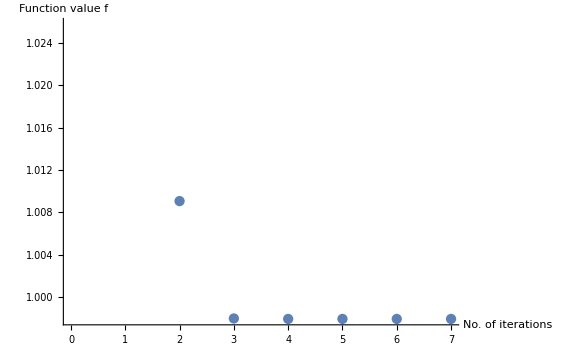

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.99797

#### Case 1.2.9: N=100, m=1/10, δ=1, dimS=2, l=15

```mathematica
CM0=partialCM[100,1/10,1,15,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.000393171 | 0 | -0.00032389 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.0527011 | 0 | 0.0464815
-0.41982 | 0 | 1.28101 | 0 | -0.000480174 | 0 | -0.000393171 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.0598408 | 0 | 0.0527011
-0.000393171 | 0 | -0.000480174 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0527011 | 0 | 0.0598408 | 0 | 1.39418 | 0 | 0.760649
-0.00032389 | 0 | -0.000393171 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.430786,0.395223,0.138089,0.136727},{{0.,-0.387634,0.,-0.397767,0.,-0.397767,0.,-0.387634},{0.63238,0.,0.640748,0.,0.640748,0.,0.63238,0.},{0.,-0.409189,0.,-0.396107,0.,0.396107,0.,0.409189},{0.625945,0.,0.615666,0.,-0.615666,0.,-0.625945,0.},{0.395702,0.,-0.385621,0.,-0.385621,0.,0.395702,0.},{0.,0.644092,0.,-0.63568,0.,-0.63568,0.,0.644092},{0.384164,0.,-0.396851,0.,0.396851,0.,-0.384164,0.},{0.,0.634808,0.,-0.645406,0.,0.645406,0.,-0.634808}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.999362

Number of iterations: 9

Number of total corrections: 0

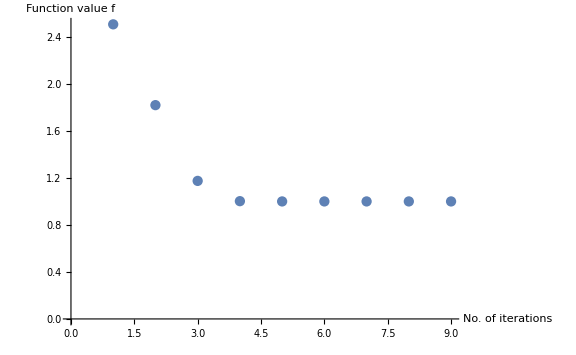

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.999362

#### Case 1.2.10: N=100, m=1/10, δ=1, dimS=2, l=20

```mathematica
CM0=partialCM[100,1/10,1,20,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.000156594 | 0 | -0.000131877 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.0284749 | 0 | 0.0252583
-0.41982 | 0 | 1.28101 | 0 | -0.00018661 | 0 | -0.000156594 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.0321328 | 0 | 0.0284749
-0.000156594 | 0 | -0.00018661 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0284749 | 0 | 0.0321328 | 0 | 1.39418 | 0 | 0.760649
-0.000131877 | 0 | -0.000156594 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.423124,0.403847,0.137787,0.137138},{{0.,-0.392148,0.,-0.397678,0.,-0.397678,0.,-0.392148},{0.630781,0.,0.635288,0.,0.635288,0.,0.630781,0.},{0.,-0.403434,0.,-0.397086,0.,0.397086,0.,0.403434},{0.627093,0.,0.622055,0.,-0.622055,0.,-0.627093,0.},{0.393376,0.,-0.387906,0.,-0.387906,0.,0.393376,0.},{0.,0.642236,0.,-0.63768,0.,-0.63768,0.,0.642236},{0.387474,0.,-0.393668,0.,0.393668,0.,-0.387474,0.},{0.,0.637487,0.,-0.642649,0.,0.642649,0.,-0.637487}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.999723

Number of iterations: 9

Number of total corrections: 0

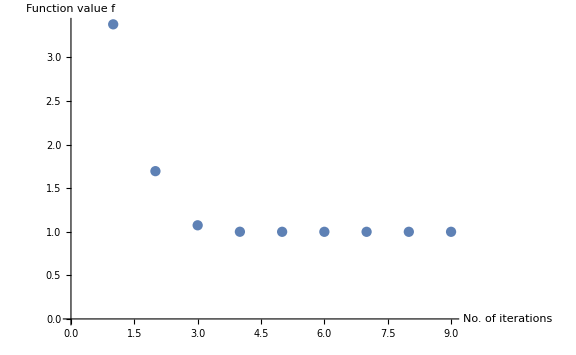

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.999723

#### Case 1.2.11: N=100, m=1/10, δ=1, dimS=2, l=30

```mathematica
CM0=partialCM[100,1/10,1,30,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.000031822 | 0 | -0.000027491 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.00895661 | 0 | 0.00802546
-0.41982 | 0 | 1.28101 | 0 | -0.0000369176 | 0 | -0.000031822 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.0100091 | 0 | 0.00895661
-0.000031822 | 0 | -0.0000369176 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00895661 | 0 | 0.0100091 | 0 | 1.39418 | 0 | 0.760649
-0.000027491 | 0 | -0.000031822 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00802546 | 0 | 0.00895661 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.416709,0.410621,0.13757,0.137392},{{0.,0.395878,0.,0.397555,0.,0.397555,0.,0.395878},{-0.629495,0.,-0.630847,0.,-0.630847,0.,-0.629495,0.},{0.,-0.399265,0.,-0.397514,0.,0.397514,0.,0.399265},{0.628225,0.,0.626825,0.,-0.626825,0.,-0.628225,0.},{-0.391448,0.,0.389797,0.,0.389797,0.,-0.391448,0.},{0.,-0.64069,0.,0.639317,0.,0.639317,0.,-0.64069},{0.389745,0.,-0.391462,0.,0.391462,0.,-0.389745,0.},{0.,0.63932,0.,-0.640748,0.,0.640748,0.,-0.63932}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.999857

Number of iterations: 10

Number of total corrections: 0

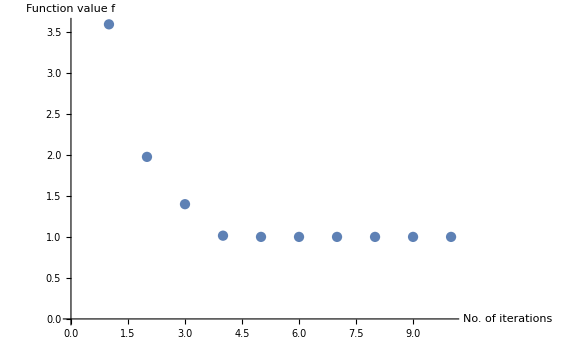

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.999857

#### Case 1.2.12: N=100, m=1/10, δ=1, dimS=2, l=40

```mathematica
CM0=partialCM[100,1/10,1,40,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -8.47426×10^-6 | 0 | -7.6322×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.00333708 | 0 | 0.00309418
-0.41982 | 0 | 1.28101 | 0 | -9.48153×10^-6 | 0 | -8.47426×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.00362182 | 0 | 0.00333708
-8.47426×10^-6 | 0 | -9.48153×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00333708 | 0 | 0.00362182 | 0 | 1.39418 | 0 | 0.760649
-7.6322×10^-6 | 0 | -8.47426×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00309418 | 0 | 0.00333708 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.414819,0.412545,0.137513,0.137452},{{0.,-0.397013,0.,-0.397466,0.,-0.397466,0.,-0.397013},{0.629162,0.,0.629525,0.,0.629525,0.,0.629162,0.},{0.,-0.398091,0.,-0.397631,0.,0.397631,0.,0.398091},{0.628545,0.,0.628176,0.,-0.628176,0.,-0.628545,0.},{0.390839,0.,-0.390394,0.,-0.390394,0.,0.390839,0.},{0.,0.640199,0.,-0.639829,0.,-0.639829,0.,0.640199},{-0.390384,0.,0.390836,0.,-0.390836,0.,0.390384,0.},{0.,-0.639836,0.,0.640212,0.,-0.640212,0.,0.639836}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.999869

Number of iterations: 8

Number of total corrections: 0

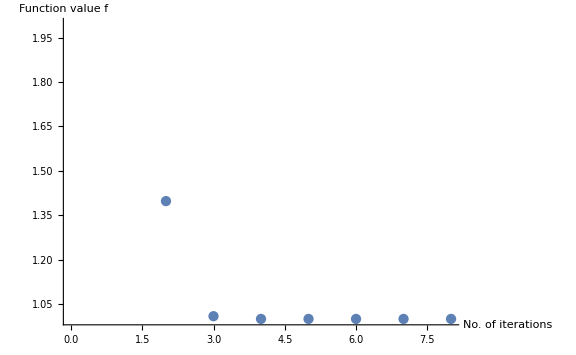

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.999869

#### Case 1.2.13: N=100, m=1/10, δ=1, dimS=2, l=45

```mathematica
CM0=partialCM[100,1/10,1,45,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -5.58759×10^-6 | 0 | -5.35149×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.00248335 | 0 | 0.00241066
-0.41982 | 0 | 1.28101 | 0 | -5.9252×10^-6 | 0 | -5.58759×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.00258647 | 0 | 0.00248335
-5.58759×10^-6 | 0 | -5.9252×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00248335 | 0 | 0.00258647 | 0 | 1.39418 | 0 | 0.760649
-5.35149×10^-6 | 0 | -5.58759×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00241066 | 0 | 0.00248335 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.41453,0.412837,0.137505,0.13746},{{0.,0.397243,0.,0.397394,0.,0.397394,0.,0.397243},{-0.629157,0.,-0.629278,0.,-0.629278,0.,-0.629157,0.},{0.,0.397857,0.,0.397704,0.,-0.397704,0.,-0.397857},{-0.628548,0.,-0.628425,0.,0.628425,0.,0.628548,0.},{-0.39069,0.,0.390541,0.,0.390541,0.,-0.39069,0.},{0.,-0.640077,0.,0.639953,0.,0.639953,0.,-0.640077},{0.390536,0.,-0.390686,0.,0.390686,0.,-0.390536,0.},{0.,0.63996,0.,-0.640085,0.,0.640085,0.,-0.63996}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.99987

Number of iterations: 9

Number of total corrections: 0

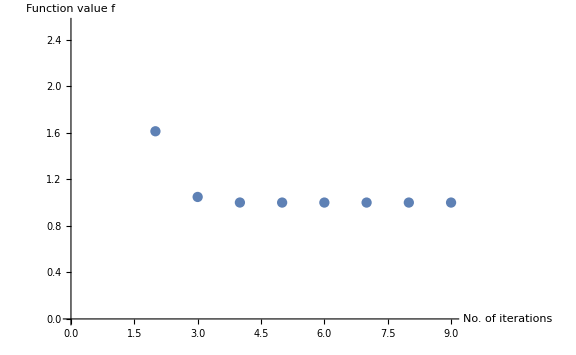

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.99987

#### Case 1.2.14: N=100, m=1/10, δ=1, dimS=2, l=48

```mathematica
CM0=partialCM[100,1/10,1,48,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -5.16558×10^-6 | 0 | -5.21181×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.00235308 | 0 | 0.00236743
-0.41982 | 0 | 1.28101 | 0 | -5.21181×10^-6 | 0 | -5.16558×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.00236743 | 0 | 0.00235308
-5.16558×10^-6 | 0 | -5.21181×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00235308 | 0 | 0.00236743 | 0 | 1.39418 | 0 | 0.760649
-5.21181×10^-6 | 0 | -5.16558×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00236743 | 0 | 0.00235308 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.414485,0.412881,0.137503,0.137461},{{0.,-0.397331,0.,-0.397331,0.,-0.397331,0.,-0.397331},{0.629199,0.,0.629199,0.,0.629199,0.,0.629199,0.},{0.,-0.397769,0.,-0.397769,0.,0.397769,0.,0.397769},{0.628506,0.,0.628506,0.,-0.628506,0.,-0.628506,0.},{0.390616,0.,-0.390616,0.,-0.390616,0.,0.390616,0.},{0.,0.640015,0.,-0.640015,0.,-0.640015,0.,0.640015},{0.390611,0.,-0.390611,0.,0.390611,0.,-0.390611,0.},{0.,0.640022,0.,-0.640022,0.,0.640022,0.,-0.640022}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.99987

Number of iterations: 9

Number of total corrections: 0

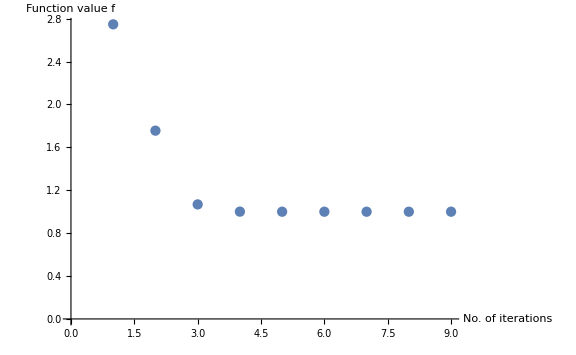

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.99987

#### Summary Case 1.2

```mathematica
listCase12={{0,0.8907375335066201},{1,0.9565937985206172},{2,0.9738019994613343},{3,0.982673119719363},{4,0.9879949368237251},{5,0.9914320951322009},{8,0.9965233529563681},{10,0.9979697604259276},{15,0.9993623138824264},{20,0.9997234483230049},{30,0.9998568167242625},{40,0.9998693733738202},{45,0.9998702749184759},{48,0.9998703891905889}};
```

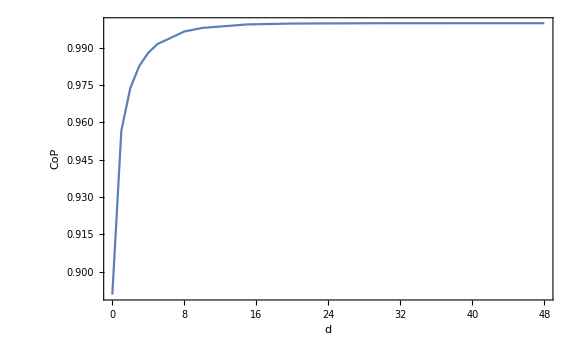

```mathematica
ListPlot[listCase12,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

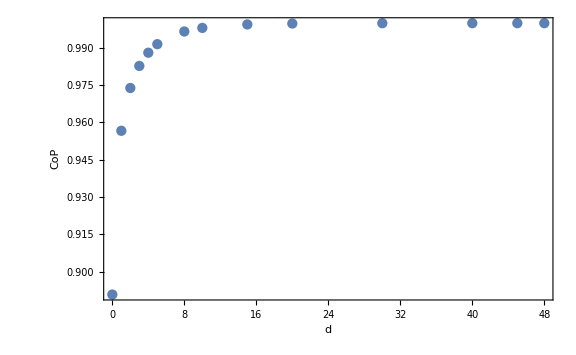
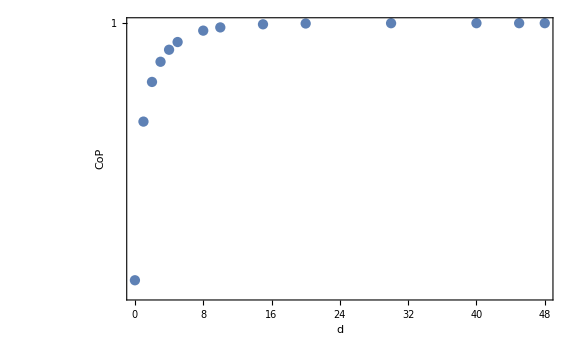

```mathematica
PlotlistCase12=Row[{ListPlot[listCase12,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[listCase12,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotlistCase12.pdf",PlotlistCase12];
```

### SubCase 1.3: N=100, m=1/10, δ=1, dimS=3 (No need to run. See relevant info. in Subsubsection Summary Case 1.3.)

#### Case 1.3.1: N=100, m=1/10, δ=1, dimS=3, l=0

```mathematica
CM0=partialCM[100,1/10,1,0,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.393413,0.253958,0.0303521,0.00965265,0.000795038,0.000113332},{{0.,0.464828,0.,0.134223,0.,0.0864634,0.,0.0864634,0.,0.134223,0.,0.464828},{-0.769132,0.,-0.66172,0.,-0.6207,0.,-0.6207,0.,-0.66172,0.,-0.769132,0.},{0.,0.653325,0.,0.134353,0.,0.0321798,0.,-0.0321798,0.,-0.134353,0.,-0.653325},{-0.686934,0.,-0.354492,0.,-0.111304,0.,0.111304,0.,0.354492,0.,0.686934,0.},{0.,-0.566478,0.,0.327234,0.,0.353083,0.,0.353083,0.,0.327234,0.,-0.566478},{0.241485,0.,-0.430893,0.,-0.629317,0.,-0.629317,0.,-0.430893,0.,0.241485,0.},{-0.126864,0.,0.557757,0.,0.246952,0.,-0.246952,0.,-0.557757,0.,0.126864,0.},{0.,-0.399904,0.,0.700438,0.,0.237261,0.,-0.237261,0.,-0.700438,0.,0.399904},{-0.0344984,0.,0.384944,0.,-0.412111,0.,-0.412111,0.,0.384944,0.,-0.0344984,0.},{0.,-0.164945,0.,0.701866,0.,-0.543861,0.,-0.543861,0.,0.701866,0.,-0.164945},{-0.00897789,0.,0.161422,0.,-0.491679,0.,0.491679,0.,-0.161422,0.,0.00897789,0.},{0.,-0.0529604,0.,0.382218,0.,-0.890471,0.,0.890471,0.,-0.382218,0.,0.0529604}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.0354

Number of iterations: 10

Number of total corrections: 0

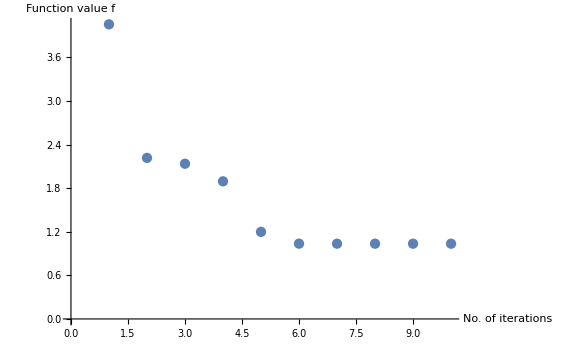

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.0354

#### Case 1.3.2: N=100, m=1/10, δ=1, dimS=3, l=1

```mathematica
CM0=partialCM[100,1/10,1,1,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.487641,0.266758,0.201283,0.0126127,0.0120973,0.000233834},{{0.,0.288111,0.,0.131376,0.,0.340432,0.,0.340432,0.,0.131376,0.,0.288111},{-0.607889,0.,-0.62104,0.,-0.714596,0.,-0.714596,0.,-0.62104,0.,-0.607889,0.},{0.,-0.629703,0.,-0.137445,0.,-0.0460643,0.,0.0460643,0.,0.137445,0.,0.629703},{0.694522,0.,0.39452,0.,0.18307,0.,-0.18307,0.,-0.39452,0.,-0.694522,0.},{-0.475034,0.,-0.0484566,0.,0.420726,0.,0.420726,0.,-0.0484566,0.,-0.475034,0.},{0.,-0.578503,0.,-0.0438156,0.,0.530198,0.,0.530198,0.,-0.0438156,0.,-0.578503},{-0.129622,0.,0.535978,0.,-0.0971383,0.,-0.0971383,0.,0.535978,0.,-0.129622,0.},{0.,-0.386136,0.,0.776688,0.,-0.346526,0.,-0.346526,0.,0.776688,0.,-0.386136},{0.143635,0.,-0.53435,0.,-0.36912,0.,0.36912,0.,0.53435,0.,-0.143635,0.},{0.,0.426987,0.,-0.609935,0.,-0.305458,0.,0.305458,0.,0.609935,0.,-0.426987},{0.0155292,0.,-0.23708,0.,0.495107,0.,-0.495107,0.,0.23708,0.,-0.0155292,0.},{0.,0.0854969,0.,-0.50555,0.,0.765119,0.,-0.765119,0.,0.50555,0.,-0.0854969}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.09587

Number of iterations: 9

Number of total corrections: 0

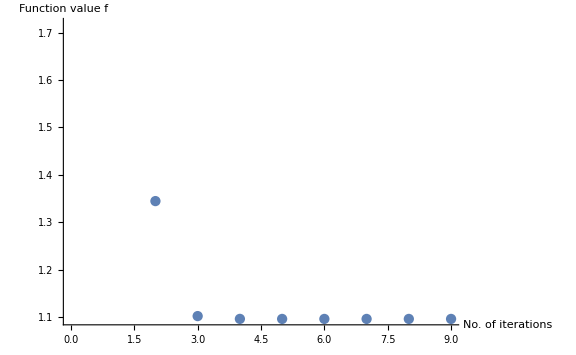

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.09587

#### Case 1.3.3: N=100, m=1/10, δ=1, dimS=3, l=2

```mathematica
CM0=partialCM[100,1/10,1,2,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.490822,0.284201,0.198414,0.118019,0.0116615,0.00930244},{{0.,0.285109,0.,0.141438,0.,0.355596,0.,0.355596,0.,0.141438,0.,0.285109},{-0.592423,0.,-0.606122,0.,-0.690013,0.,-0.690013,0.,-0.606122,0.,-0.592423,0.},{0.,0.580859,0.,0.142929,0.,0.137343,0.,-0.137343,0.,-0.142929,0.,-0.580859},{-0.683633,0.,-0.438657,0.,-0.292767,0.,0.292767,0.,0.438657,0.,0.683633,0.},{-0.483822,0.,-0.0442017,0.,0.405499,0.,0.405499,0.,-0.0442017,0.,-0.483822,0.},{0.,-0.588916,0.,-0.0250729,0.,0.527649,0.,0.527649,0.,-0.0250729,0.,-0.588916},{-0.180561,0.,0.154493,0.,0.602865,0.,-0.602865,0.,-0.154493,0.,0.180561,0.},{0.,-0.32933,0.,0.0308151,0.,0.72284,0.,-0.72284,0.,-0.0308151,0.,0.32933},{-0.123437,0.,0.531675,0.,-0.112505,0.,-0.112505,0.,0.531675,0.,-0.123437,0.},{0.,-0.373992,0.,0.777097,0.,-0.361521,0.,-0.361521,0.,0.777097,0.,-0.373992},{0.116938,0.,-0.548914,0.,0.076678,0.,-0.076678,0.,0.548914,0.,-0.116938,0.},{0.,0.371495,0.,-0.787998,0.,0.3132,0.,-0.3132,0.,0.787998,0.,-0.371495}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.11317

Number of iterations: 9

Number of total corrections: 1

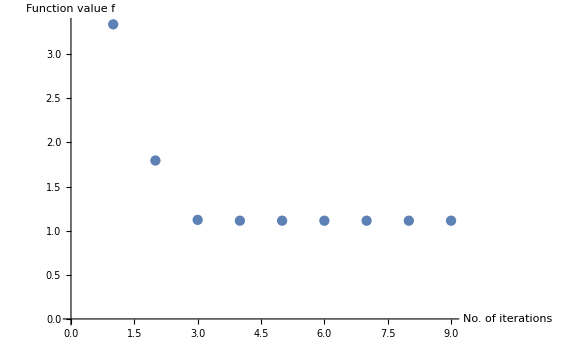

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.11317

#### Case 1.3.4: N=100, m=1/10, δ=1, dimS=3, l=3

```mathematica
CM0=partialCM[100,1/10,1,3,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.484977,0.302442,0.19528,0.14809,0.0124742,0.009514},{{0.,0.290822,0.,0.147149,0.,0.358219,0.,0.358219,0.,0.147149,0.,0.290822},{-0.588506,0.,-0.597618,0.,-0.672524,0.,-0.672524,0.,-0.597618,0.,-0.588506,0.},{0.,0.528553,0.,0.147111,0.,0.211768,0.,-0.211768,0.,-0.147111,0.,-0.528553},{-0.662964,0.,-0.47004,0.,-0.37985,0.,0.37985,0.,0.47004,0.,0.662964,0.},{0.481644,0.,0.0363619,0.,-0.405961,0.,-0.405961,0.,0.0363619,0.,0.481644,0.},{0.,0.590153,0.,0.0153822,0.,-0.530094,0.,-0.530094,0.,0.0153822,0.,0.590153},{-0.260853,0.,0.11431,0.,0.571657,0.,-0.571657,0.,-0.11431,0.,0.260853,0.},{0.,-0.407018,0.,0.0206819,0.,0.684788,0.,-0.684788,0.,-0.0206819,0.,0.407018},{-0.120968,0.,0.529524,0.,-0.119308,0.,-0.119308,0.,0.529524,0.,-0.120968,0.},{0.,-0.368745,0.,0.777117,0.,-0.367884,0.,-0.367884,0.,0.777117,0.,-0.368745},{-0.117228,0.,0.545188,0.,-0.0861423,0.,0.0861423,0.,-0.545188,0.,0.117228,0.},{0.,-0.370359,0.,0.785945,0.,-0.326158,0.,0.326158,0.,-0.785945,0.,0.370359}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.12242

Number of iterations: 8

Number of total corrections: 0

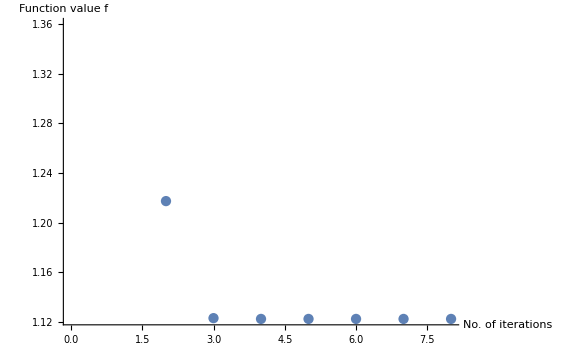

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.12242

#### Case 1.3.5: N=100, m=1/10, δ=1, dimS=3, l=5

```mathematica
CM0=partialCM[100,1/10,1,5,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771
-0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.470471,0.332902,0.191476,0.169796,0.0141584,0.0102293},{{0.,-0.303333,0.,-0.152753,0.,-0.358001,0.,-0.358001,0.,-0.152753,0.,-0.303333},{0.586758,0.,0.586321,0.,0.649312,0.,0.649312,0.,0.586321,0.,0.586758,0.},{0.,0.45562,0.,0.151281,0.,0.288489,0.,-0.288489,0.,-0.151281,0.,-0.45562},{-0.629266,0.,-0.502955,0.,-0.475604,0.,0.475604,0.,0.502955,0.,0.629266,0.},{0.474122,0.,0.025439,0.,-0.412577,0.,-0.412577,0.,0.025439,0.,0.474122,0.},{0.,0.587098,0.,0.0069248,0.,-0.536791,0.,-0.536791,0.,0.0069248,0.,0.587098},{0.34957,0.,-0.061922,0.,-0.519617,0.,0.519617,0.,0.061922,0.,-0.34957,0.},{0.,0.486463,0.,-0.00921973,0.,-0.633883,0.,0.633883,0.,0.00921973,0.,-0.486463},{0.119548,0.,-0.527872,0.,0.123942,0.,0.123942,0.,-0.527872,0.,0.119548,0.},{0.,0.365213,0.,-0.777198,0.,0.371772,0.,0.371772,0.,-0.777198,0.,0.365213},{0.117388,0.,-0.540326,0.,0.0979465,0.,-0.0979465,0.,0.540326,0.,-0.117388,0.},{0.,0.368359,0.,-0.783493,0.,0.34118,0.,-0.34118,0.,0.783493,0.,-0.368359}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.13188

Number of iterations: 9

Number of total corrections: 0

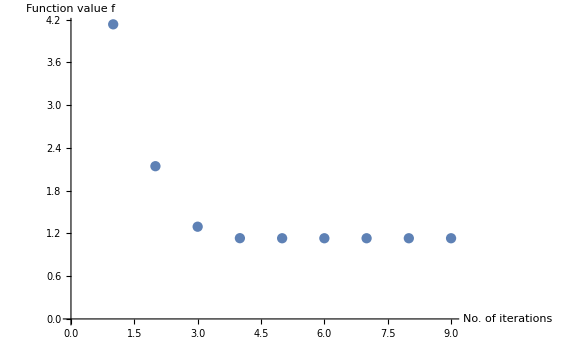

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.13188

#### Case 1.3.6: N=100, m=1/10, δ=1, dimS=3, l=8

```mathematica
CM0=partialCM[100,1/10,1,8,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311
-0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.452619,0.362174,0.188786,0.179115,0.0151884,0.0114143},{{0.,0.317715,0.,0.155839,0.,0.356112,0.,0.356112,0.,0.155839,0.,0.317715},{-0.586948,0.,-0.575487,0.,-0.628551,0.,-0.628551,0.,-0.575487,0.,-0.586948,0.},{0.,0.404818,0.,0.153755,0.,0.326403,0.,-0.326403,0.,-0.153755,0.,-0.404818},{-0.60671,0.,-0.524283,0.,-0.532416,0.,0.532416,0.,0.524283,0.,0.60671,0.},{0.464733,0.,0.016221,0.,-0.421723,0.,-0.421723,0.,0.016221,0.,0.464733,0.},{0.,0.581083,0.,0.00277285,0.,-0.545161,0.,-0.545161,0.,0.00277285,0.,0.581083},{0.399581,0.,-0.0293371,0.,-0.481756,0.,0.481756,0.,0.0293371,0.,-0.399581,0.},{0.,0.528696,0.,-0.00337196,0.,-0.599151,0.,0.599151,0.,0.00337196,0.,-0.528696},{0.1193,0.,-0.527665,0.,0.124477,0.,0.124477,0.,-0.527665,0.,0.1193,0.},{0.,0.364373,0.,-0.777523,0.,0.371627,0.,0.371627,0.,-0.777523,0.,0.364373},{-0.117622,0.,0.536426,0.,-0.106809,0.,0.106809,0.,-0.536426,0.,0.117622,0.},{0.,-0.366739,0.,0.781636,0.,-0.351782,0.,0.351782,0.,-0.781636,0.,0.366739}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.13761

Number of iterations: 8

Number of total corrections: 0

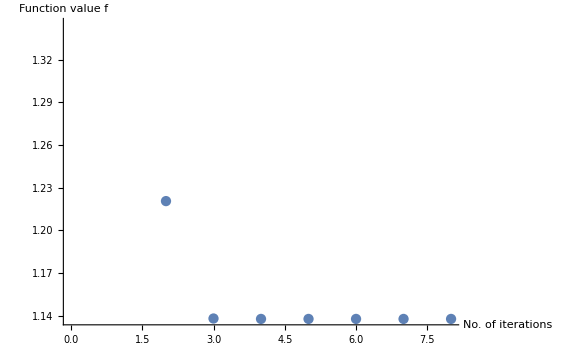

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.13761

#### Case 1.3.7: N=100, m=1/10, δ=1, dimS=3, l=10

```mathematica
CM0=partialCM[100,1/10,1,10,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.443786,0.37457,0.187824,0.181474,0.0153554,0.012045},{{0.,0.324702,0.,0.156621,0.,0.354976,0.,0.354976,0.,0.156621,0.,0.324702},{-0.58739,0.,-0.570512,0.,-0.619531,0.,-0.619531,0.,-0.570512,0.,-0.58739,0.},{0.,0.387991,0.,0.154593,0.,0.335965,0.,-0.335965,0.,-0.154593,0.,-0.387991},{-0.600231,0.,-0.53199,0.,-0.550277,0.,0.550277,0.,0.53199,0.,0.600231,0.},{0.46009,0.,0.0123661,0.,-0.426307,0.,-0.426307,0.,0.0123661,0.,0.46009,0.},{0.,0.577727,0.,0.00168325,0.,-0.549305,0.,-0.549305,0.,0.00168325,0.,0.577727},{0.414207,0.,-0.0194997,0.,-0.469377,0.,0.469377,0.,0.0194997,0.,-0.414207,0.},{0.,0.540756,0.,-0.00194599,0.,-0.587964,0.,0.587964,0.,0.00194599,0.,-0.540756},{0.119281,0.,-0.527957,0.,0.123835,0.,0.123835,0.,-0.527957,0.,0.119281,0.},{0.,0.364406,0.,-0.777762,0.,0.370722,0.,0.370722,0.,-0.777762,0.,0.364406},{0.117789,0.,-0.534899,0.,0.110102,0.,-0.110102,0.,0.534899,0.,-0.117789,0.},{0.,0.366168,0.,-0.780933,0.,0.355572,0.,-0.355572,0.,0.780933,0.,-0.366168}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.13931

Number of iterations: 9

Number of total corrections: 0

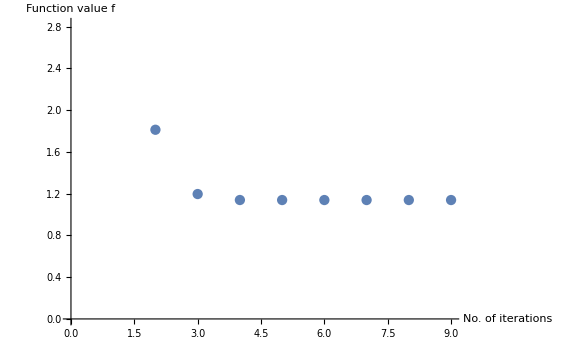

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.13931

#### Case 1.3.8: N=100, m=1/10, δ=1, dimS=3, l=15

```mathematica
CM0=partialCM[100,1/10,1,15,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815
-0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.429294,0.392665,0.186552,0.18387,0.0152167,0.0130845},{{0.,-0.33618,0.,-0.157164,0.,-0.352908,0.,-0.352908,0.,-0.157164,0.,-0.33618},{0.588452,0.,0.562565,0.,0.605707,0.,0.605707,0.,0.562565,0.,0.588452,0.},{0.,-0.367418,0.,-0.155682,0.,-0.345203,0.,0.345203,0.,0.155682,0.,0.367418},{0.593654,0.,0.542518,0.,0.571896,0.,-0.571896,0.,-0.542518,0.,-0.593654,0.},{-0.452408,0.,-0.00653595,0.,0.433874,0.,0.433874,0.,-0.00653595,0.,-0.452408,0.},{0.,-0.571854,0.,-0.000596745,0.,0.556118,0.,0.556118,0.,-0.000596745,0.,-0.571854},{0.430687,0.,-0.00833143,0.,-0.454645,0.,0.454645,0.,0.00833143,0.,-0.430687,0.},{0.,0.554236,0.,-0.000636749,0.,-0.574718,0.,0.574718,0.,0.000636749,0.,-0.554236},{-0.119181,0.,0.52885,0.,-0.121986,0.,-0.121986,0.,0.52885,0.,-0.119181,0.},{0.,-0.364679,0.,0.778256,0.,-0.368534,0.,-0.368534,0.,0.778256,0.,-0.364679},{0.118142,0.,-0.532756,0.,0.114522,0.,-0.114522,0.,0.532756,0.,-0.118142,0.},{0.,0.365483,0.,-0.779971,0.,0.360516,0.,-0.360516,0.,0.779971,0.,-0.365483}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.14101

Number of iterations: 9

Number of total corrections: 0

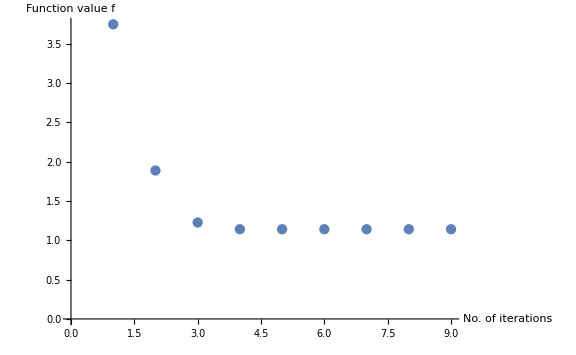

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.14101

#### Case 1.3.9: N=100, m=1/10, δ=1, dimS=3, l=20

```mathematica
CM0=partialCM[100,1/10,1,20,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.000131877 | 0 | -0.000111427 | 0 | -0.0000944326 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.0252583 | 0 | 0.0224262 | 0 | 0.0199298
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.000156594 | 0 | -0.000131877 | 0 | -0.000111427 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.0284749 | 0 | 0.0252583 | 0 | 0.0224262
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.00018661 | 0 | -0.000156594 | 0 | -0.000131877 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.0321328 | 0 | 0.0284749 | 0 | 0.0252583
-0.000131877 | 0 | -0.000156594 | 0 | -0.00018661 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.0321328 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000111427 | 0 | -0.000131877 | 0 | -0.000156594 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0224262 | 0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0000944326 | 0 | -0.000111427 | 0 | -0.000131877 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0199298 | 0 | 0.0224262 | 0 | 0.0252583 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.421469,0.401467,0.185981,0.184686,0.0149372,0.0136413},{{0.,0.342429,0.,0.157125,0.,0.351693,0.,0.351693,0.,0.157125,0.,0.342429},{-0.589176,0.,-0.558323,0.,-0.598597,0.,-0.598597,0.,-0.558323,0.,-0.589176,0.},{0.,-0.358893,0.,-0.156173,0.,-0.348082,0.,0.348082,0.,0.156173,0.,0.358893},{0.591572,0.,0.547435,0.,0.580881,0.,-0.580881,0.,-0.547435,0.,-0.591572,0.},{-0.448206,0.,-0.00354532,0.,0.437983,0.,0.437983,0.,-0.00354532,0.,-0.448206,0.},{0.,-0.56852,0.,-0.000250714,0.,0.559806,0.,0.559806,0.,-0.000250714,0.,-0.56852},{-0.437004,0.,0.00405017,0.,0.448759,0.,-0.448759,0.,-0.00405017,0.,0.437004,0.},{0.,-0.559391,0.,0.000257718,0.,0.569443,0.,-0.569443,0.,-0.000257718,0.,0.559391},{0.119047,0.,-0.529523,0.,0.120663,0.,0.120663,0.,-0.529523,0.,0.119047,0.},{0.,0.36486,0.,-0.778573,0.,0.367073,0.,0.367073,0.,-0.778573,0.,0.36486},{0.118373,0.,-0.53174,0.,0.116524,0.,-0.116524,0.,0.53174,0.,-0.118373,0.},{0.,0.365226,0.,-0.779525,0.,0.362694,0.,-0.362694,0.,0.779525,0.,-0.365226}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.1415

Number of iterations: 10

Number of total corrections: 1

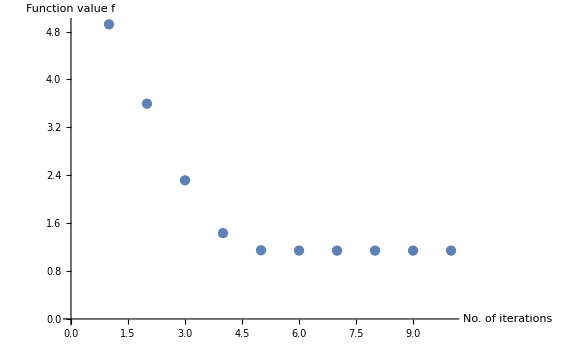

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.1415

#### Case 1.3.10: N=100, m=1/10, δ=1, dimS=3, l=30

```mathematica
CM0=partialCM[100,1/10,1,30,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.000027491 | 0 | -0.0000238043 | 0 | -0.0000206625 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.00802546 | 0 | 0.00720207 | 0 | 0.00647449
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.000031822 | 0 | -0.000027491 | 0 | -0.0000238043 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.00895661 | 0 | 0.00802546 | 0 | 0.00720207
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0000369176 | 0 | -0.000031822 | 0 | -0.000027491 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.0100091 | 0 | 0.00895661 | 0 | 0.00802546
-0.000027491 | 0 | -0.000031822 | 0 | -0.0000369176 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.00802546 | 0 | 0.00895661 | 0 | 0.0100091 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0000238043 | 0 | -0.000027491 | 0 | -0.000031822 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00720207 | 0 | 0.00802546 | 0 | 0.00895661 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0000206625 | 0 | -0.0000238043 | 0 | -0.000027491 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00647449 | 0 | 0.00720207 | 0 | 0.00802546 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.414849,0.408457,0.185556,0.185194,0.014579,0.0141155},{{0.,-0.347766,0.,-0.156916,0.,-0.350606,0.,-0.350606,0.,-0.156916,0.,-0.347766},{0.589875,0.,0.554739,0.,0.592729,0.,0.592729,0.,0.554739,0.,0.589875,0.},{0.,0.35273,0.,0.156558,0.,0.349747,0.,-0.349747,0.,-0.156558,0.,-0.35273},{-0.590387,0.,-0.551273,0.,-0.587415,0.,0.587415,0.,0.551273,0.,0.590387,0.},{0.444606,0.,0.00106784,0.,-0.441483,0.,-0.441483,0.,0.00106784,0.,0.444606,0.},{0.,0.565608,0.,0.0000562221,0.,-0.562937,0.,-0.562937,0.,0.0000562221,0.,0.565608},{0.441354,0.,-0.00111448,0.,-0.44462,0.,0.44462,0.,0.00111448,0.,-0.441354,0.},{0.,0.562948,0.,-0.0000564537,0.,-0.565743,0.,0.565743,0.,0.0000564537,0.,-0.562948},{-0.118872,0.,0.530195,0.,-0.119383,0.,-0.119383,0.,0.530195,0.,-0.118872,0.},{0.,-0.365004,0.,0.778869,0.,-0.365703,0.,-0.365703,0.,0.778869,0.,-0.365004},{-0.118593,0.,0.530934,0.,-0.11806,0.,0.11806,0.,-0.530934,0.,0.118593,0.},{0.,-0.36506,0.,0.77918,0.,-0.364332,0.,0.364332,0.,-0.77918,0.,0.36506}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.14171

Number of iterations: 9

Number of total corrections: 1

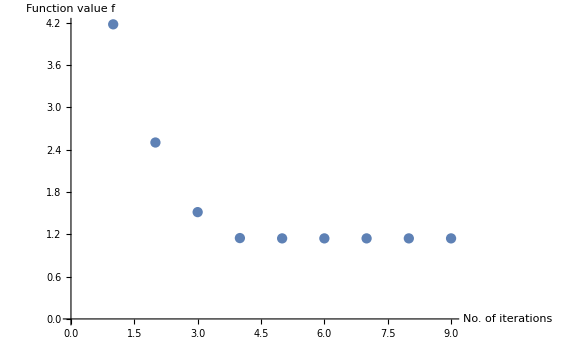

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.14171

#### Case 1.3.11: N=100, m=1/10, δ=1, dimS=3, l=40

```mathematica
CM0=partialCM[100,1/10,1,40,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -7.6322×10^-6 | 0 | -6.93646×10^-6 | 0 | -6.37158×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.00309418 | 0 | 0.00288986 | 0 | 0.00272137
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -8.47426×10^-6 | 0 | -7.6322×10^-6 | 0 | -6.93646×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.00333708 | 0 | 0.00309418 | 0 | 0.00288986
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -9.48153×10^-6 | 0 | -8.47426×10^-6 | 0 | -7.6322×10^-6 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.00362182 | 0 | 0.00333708 | 0 | 0.00309418
-7.6322×10^-6 | 0 | -8.47426×10^-6 | 0 | -9.48153×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.00309418 | 0 | 0.00333708 | 0 | 0.00362182 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-6.93646×10^-6 | 0 | -7.6322×10^-6 | 0 | -8.47426×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00288986 | 0 | 0.00309418 | 0 | 0.00333708 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-6.37158×10^-6 | 0 | -6.93646×10^-6 | 0 | -7.6322×10^-6 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00272137 | 0 | 0.00288986 | 0 | 0.00309418 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.412907,0.410435,0.185443,0.185313,0.0144485,0.0142582},{{0.,0.349441,0.,0.156821,0.,0.350177,0.,0.350177,0.,0.156821,0.,0.349441},{-0.590197,0.,-0.553688,0.,-0.590934,0.,-0.590934,0.,-0.553688,0.,-0.590197,0.},{0.,-0.350978,0.,-0.156671,0.,-0.350227,0.,0.350227,0.,0.156671,0.,0.350978},{0.59002,0.,0.552349,0.,0.589271,0.,-0.589271,0.,-0.552349,0.,-0.59002,0.},{-0.443433,0.,-0.000275096,0.,0.442624,0.,0.442624,0.,-0.000275096,0.,-0.443433,0.},{0.,-0.564644,0.,-0.0000126052,0.,0.563951,0.,0.563951,0.,-0.0000126052,0.,-0.564644},{-0.442596,0.,0.000279692,0.,0.443419,0.,-0.443419,0.,-0.000279692,0.,0.442596,0.},{0.,-0.563971,0.,0.000012607,0.,0.564676,0.,-0.564676,0.,-0.000012607,0.,0.563971},{-0.118826,0.,0.530412,0.,-0.11896,0.,-0.11896,0.,0.530412,0.,-0.118826,0.},{0.,-0.365068,0.,0.778961,0.,-0.365251,0.,-0.365251,0.,0.778961,0.,-0.365068},{-0.118644,0.,0.530705,0.,-0.118508,0.,0.118508,0.,-0.530705,0.,0.118644,0.},{0.,-0.364995,0.,0.779083,0.,-0.364809,0.,0.364809,0.,-0.779083,0.,0.364995}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.14174

Number of iterations: 11

Number of total corrections: 0

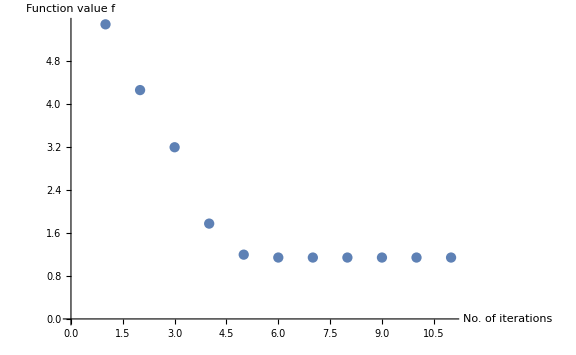

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.14174

#### Case 1.3.12: N=100, m=1/10, δ=1, dimS=3, l=47

```mathematica
CM0=partialCM[100,1/10,1,47,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -5.16558×10^-6 | 0 | -5.21181×10^-6 | 0 | -5.35149×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.00235308 | 0 | 0.00236743 | 0 | 0.00241066
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -5.21181×10^-6 | 0 | -5.16558×10^-6 | 0 | -5.21181×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.00236743 | 0 | 0.00235308 | 0 | 0.00236743
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -5.35149×10^-6 | 0 | -5.21181×10^-6 | 0 | -5.16558×10^-6 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.00241066 | 0 | 0.00236743 | 0 | 0.00235308
-5.16558×10^-6 | 0 | -5.21181×10^-6 | 0 | -5.35149×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.00235308 | 0 | 0.00236743 | 0 | 0.00241066 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-5.21181×10^-6 | 0 | -5.16558×10^-6 | 0 | -5.21181×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00236743 | 0 | 0.00235308 | 0 | 0.00236743 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-5.35149×10^-6 | 0 | -5.21181×10^-6 | 0 | -5.16558×10^-6 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00241066 | 0 | 0.00236743 | 0 | 0.00235308 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.412613,0.410732,0.185427,0.18533,0.0144274,0.0142802},{{0.,0.349903,0.,0.156805,0.,0.349903,0.,0.349903,0.,0.156805,0.,0.349903},{-0.590455,0.,-0.553529,0.,-0.590455,0.,-0.590455,0.,-0.553529,0.,-0.590455,0.},{0.,0.350507,0.,0.156688,0.,0.350507,0.,-0.350507,0.,-0.156688,0.,-0.350507},{-0.589757,0.,-0.55251,0.,-0.589757,0.,0.589757,0.,0.55251,0.,0.589757,0.},{0.443026,0.,0.,0.,-0.443026,0.,-0.443026,0.,0.,0.,0.443026,0.},{0.,0.564301,0.,0.,0.,-0.564301,0.,-0.564301,0.,0.,0.,0.564301},{-0.443011,0.,0.,0.,0.443011,0.,-0.443011,0.,0.,0.,0.443011,0.},{0.,-0.56432,0.,0.,0.,0.56432,0.,-0.56432,0.,0.,0.,0.56432},{-0.118856,0.,0.530446,0.,-0.118856,0.,-0.118856,0.,0.530446,0.,-0.118856,0.},{0.,-0.36513,0.,0.778975,0.,-0.36513,0.,-0.36513,0.,0.778975,0.,-0.36513},{-0.118613,0.,0.53067,0.,-0.118613,0.,0.118613,0.,-0.53067,0.,0.118613,0.},{0.,-0.364933,0.,0.779068,0.,-0.364933,0.,0.364933,0.,-0.779068,0.,0.364933}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.14175

Number of iterations: 9

Number of total corrections: 1

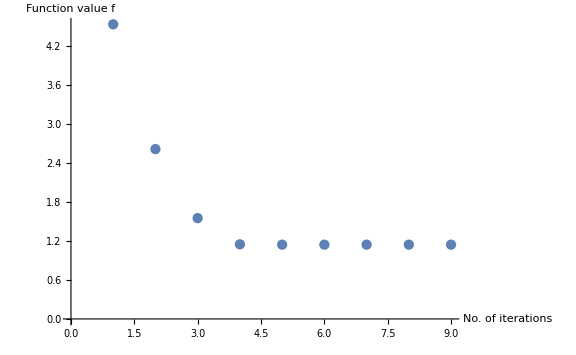

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.14175

#### Summary Case 1.3

```mathematica
listCase13={{0,1.0353996949506774},{1,1.0958670747421804},{2,1.1131666698812772},{3,1.122422627370193},{5,1.131881609255603},{8,1.137614589740662},{10,1.1393068517535765},{15,1.141010771014572},{20,1.141495464571084},{30,1.1417101572000095},{40,1.141742587423367},{47,1.1417463579004707}};
```

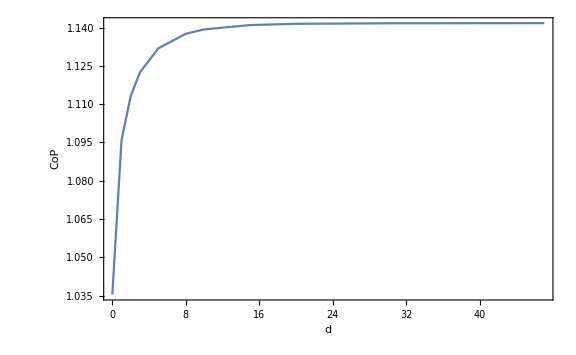

```mathematica
ListPlot[listCase13,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

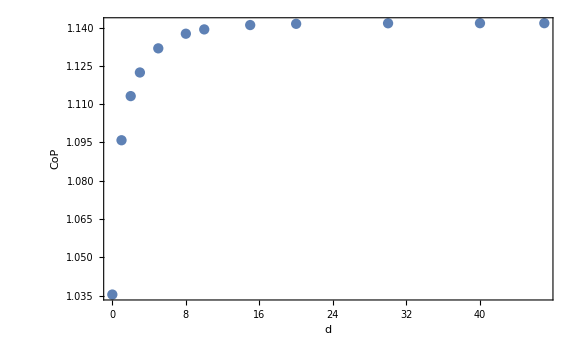
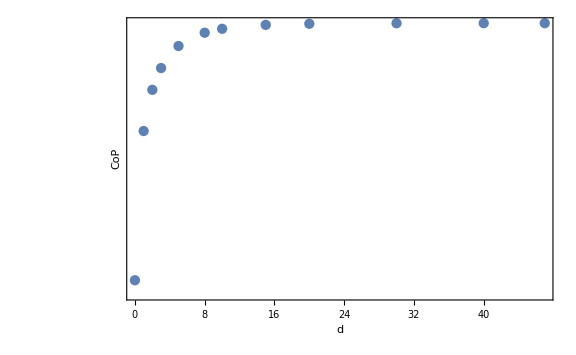

```mathematica
PlotlistCase13=Row[{ListPlot[listCase13,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[listCase13,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotlistCase13.pdf",PlotlistCase13];
```

### SubCase 1.4: N=100, m=1/10, δ=1, dimS=8 (No need to run. See relevant info. in Subsubsection Summary Case 1.4.)

IMPORTANT (04.09.19 - 13:21): SubCase 1.4 is being studied with the most recent function definitions (as of 30.08.19). In this subcase, we also use Schur Decomposition to find the correct transformation MTra that brings the mixed state covariance matrix to the standard form. 

UPDATE: (05.09.19 - 11:51): In SubCase 1.4.5, it seemed as if the Schur decomposition would no longer be needed. However, the transformation arising from the usual package implementation does not work. So, we continue using Schur decomposition.

#### Case 1.4.1: N=100, m=1/10, δ=1, dimS=8, l=0

```mathematica
CM0=partialCM[100,1/10,1,0,8,8];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771
-0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
GOExtractStdFormG[CM0]
```

Dot::dotsh: Tensors … and {«1»} have incompatible shapes.

There’s a problem here.

Problem analysis

```mathematica
Length[CM0]
```

32

```mathematica
GOΩqpqp[16].CM0//Eigenvalues//Chop
```

{0.+1.26217 ⅈ,0.-1.26217 ⅈ,0.+1.20751 ⅈ,0.-1.20751 ⅈ,0.+1.00303 ⅈ,0.-1.00303 ⅈ,0.+1.0013 ⅈ,0.-1.0013 ⅈ,0.+1.00002 ⅈ,0.-1.00002 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

```mathematica
GOTransformGtoJ[CM0,"qpqp","qpqp"]//Eigenvalues//Chop
```

{0.+1.26217 ⅈ,0.-1.26217 ⅈ,0.+1.20751 ⅈ,0.-1.20751 ⅈ,0.+1.00303 ⅈ,0.-1.00303 ⅈ,0.+1.0013 ⅈ,0.-1.0013 ⅈ,0.+1.00002 ⅈ,0.-1.00002 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

The problem is that there are many identical symplectic eigenvalues. We need to make a smart diagonalization. Here, we follow the discussion in https://math.stackexchange.com/questions/1171842/finding-the-symplectic-matrix-in-williamsons-theorem based on SchurDecomposition.

```mathematica
?SchurDecomposition
```

SchurDecomposition[m] yields the Schur decomposition for a numerical matrix m, given as a list {q,t} where q is an orthonormal matrix and t is a block upper-triangular matrix. 
SchurDecomposition[{m,a}] gives the generalized Schur decomposition of m with respect to a.

```mathematica
sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;
```

```mathematica
MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]];
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm
```

{0.354581,0.316783,0.0389142,0.0254456,0.00340455,0.0015736,0.00019428,0.0000683147,7.36423×10^-6,2.01119×10^-6,1.81586×10^-7,3.94248×10^-8,2.10734×10^-8,0.+1.05367×10^-8 ⅈ,0.+1.49012×10^-8 ⅈ,0.+1.97124×10^-8 ⅈ}

(1.26217 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.26217 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.20751 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.20751 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.00303 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.00303 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.0013 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.0013 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00002 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00002 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

The correct thing to do seems to do the Schur decomposition with respect to GOΩqpqp[16] and not GOTransformGtoJ[CM0,”qpqp”,”qpqp”].

```mathematica
Det[MTra.CM0.Transpose[MTra]]//Simplify
```

2.34311

So it’s not a pure state, as expected.

Back to the code:

```mathematica
{rlist,MTra};
```

```mathematica
JT=GOPurifyStandardJBoson[rlist,(8+8),"qpqp"]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[4(8+8)],"qpqp","qpqp"]//Chop;
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{8,8},"GOSpBasis"]}}]//SparseArray,{10}];
```

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];ProblemSpecific={function,gradient};
```

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{8,8,8,8}];
metric=GOMetricSp[LieBasis,JR0];
SystemSpecific={JR0,M0List,LieBasis,metric};
```

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 1765.73

Final value: {1.56955,1.56955}

Number of iterations: {8,8}

Number of total corrections: 0

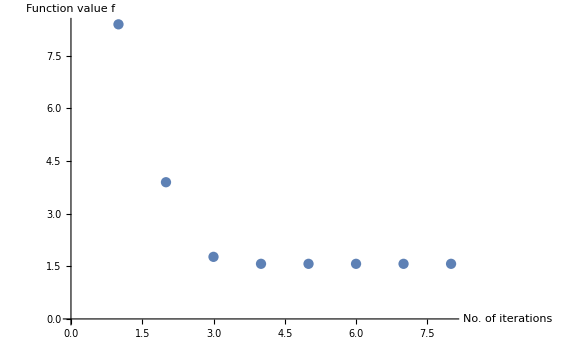

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
Result[[1,All]]
```

{1.56955,1.56955}

#### Case 1.4.2: N=100, m=1/10, δ=1, dimS=8, l=1

```mathematica
CM0=partialCM[100,1/10,1,1,8,8];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799
-0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
GOExtractStdFormG[CM0]
```

Dot::dotsh: Tensors … and {«1»} have incompatible shapes.

Same problem here.

```mathematica
Length[CM0]
```

32

```mathematica
GOΩqpqp[16].CM0//Eigenvalues//Chop
```

{0.+1.40578 ⅈ,0.-1.40578 ⅈ,0.+1.21068 ⅈ,0.-1.21068 ⅈ,0.+1.18017 ⅈ,0.-1.18017 ⅈ,0.+1.00175 ⅈ,0.-1.00175 ⅈ,0.+1.00138 ⅈ,0.-1.00138 ⅈ,0.+1.00001 ⅈ,0.-1.00001 ⅈ,0.+1.00001 ⅈ,0.-1.00001 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

```mathematica
GOTransformGtoJ[CM0,"qpqp","qpqp"]//Eigenvalues//Chop
```

{0.+1.40578 ⅈ,0.-1.40578 ⅈ,0.+1.21068 ⅈ,0.-1.21068 ⅈ,0.+1.18017 ⅈ,0.-1.18017 ⅈ,0.+1.00175 ⅈ,0.-1.00175 ⅈ,0.+1.00138 ⅈ,0.-1.00138 ⅈ,0.+1.00001 ⅈ,0.-1.00001 ⅈ,0.+1.00001 ⅈ,0.-1.00001 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

The problem is that there are many identical symplectic eigenvalues. We need to make a smart diagonalization. Here, we follow the discussion in https://math.stackexchange.com/questions/1171842/finding-the-symplectic-matrix-in-williamsons-theorem based on SchurDecomposition.

```mathematica
?SchurDecomposition
```

SchurDecomposition[m] yields the Schur decomposition for a numerical matrix m, given as a list {q,t} where q is an orthonormal matrix and t is a block upper-triangular matrix. 
SchurDecomposition[{m,a}] gives the generalized Schur decomposition of m with respect to a.

```mathematica
sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;
```

```mathematica
MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]];
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm
```

{0.436447,0.319118,0.295805,0.0296106,0.0262841,0.00236837,0.00170532,0.000140472,0.0000795338,5.62248×10^-6,2.59085×10^-6,1.42927×10^-7,5.67419×10^-8,1.05367×10^-8,0,0.+1.82501×10^-8 ⅈ}

(1.40578 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.40578 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.21068 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.21068 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.18017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.18017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.00175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00138 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00138 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

The correct thing to do seems to do the Schur decomposition with respect to GOΩqpqp[16] and not GOTransformGtoJ[CM0,”qpqp”,”qpqp”].

```mathematica
Det[MTra.CM0.Transpose[MTra]]//Simplify
```

4.05993

So it’s not a pure state, as expected.

Back to the code:

```mathematica
{rlist,MTra};
```

```mathematica
JT=GOPurifyStandardJBoson[rlist,(8+8),"qpqp"]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[4(8+8)],"qpqp","qpqp"]//Chop;
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{8,8},"GOSpBasis"]}}]//SparseArray,{20}];
```

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];ProblemSpecific={function,gradient};
```

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{8,8,8,8}];
metric=GOMetricSp[LieBasis,JR0];
SystemSpecific={JR0,M0List,LieBasis,metric};
```

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.62271+0. ⅈ,1.43788×10^-15+0. ⅈ,-0.545658+0. ⅈ,1.55466×10^-15+0. ⅈ,-0.113216+0. ⅈ,1.57233×10^-15+0. ⅈ,-0.0420564+0. ⅈ,1.18356×10^-15+0. ⅈ,-0.0233454+0. ⅈ,9.50715×10^-16+0. ⅈ,«31»,4.99313×10^-17+0. ⅈ,0.0000697658+0. ⅈ,4.10222×10^-18+0. ⅈ,0.000035444+0. ⅈ,9.93962×10^-19+0. ⅈ,2.94193×10^-6+0. ⅈ,-6.11675×10^-21+0. ⅈ,1.17664×10^-6+0. ⅈ,-8.28187×10^-20+0. ⅈ,«14»},«49»,«14»} may contain significant numerical errors.

Reason for termination: Function value tolerance reached

Time taken: 3818.98

Final value: {1.60737,1.60737}

Number of iterations: {9,9}

Number of total corrections: 3

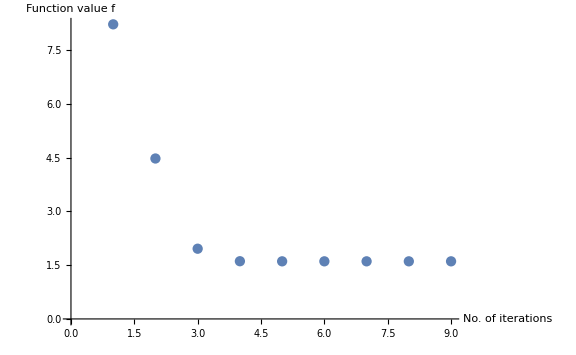

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
Result[[1,All]]
```

{1.60737,1.60737}

#### Case 1.4.3: N=100, m=1/10, δ=1, dimS=8, l=2

```mathematica
CM0=partialCM[100,1/10,1,2,8,8];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923
-0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
GOExtractStdFormG[CM0]
```

Dot::dotsh: Tensors … and {{-0.000104995,-0.00119763,0.00694994,0.0283294,-0.0793539,-0.211306,0.348963,0.735672,-0.729043,-1.36234,0.746451,1.37107,-0.325009,«6»,-0.0284842,0.0236188,0.0390319,-0.00647977,-0.0157864,-0.00378468,-0.00399568,0.00113327,0.00296645,0.0000850978,-0.000102886,-9.65087×10^-6,-0.0000516727},«30»,{«21»,«30»,«23»}} have incompatible shapes.

Same problem here.

```mathematica
Length[CM0]
```

32

```mathematica
GOTransformGtoJ[CM0,"qpqp","qpqp"]//Eigenvalues//Chop
```

{0.+1.42693 ⅈ,0.-1.42693 ⅈ,0.+1.21437 ⅈ,0.-1.21437 ⅈ,0.+1.18017 ⅈ,0.-1.18017 ⅈ,0.+1.03707 ⅈ,0.-1.03707 ⅈ,0.+1.00165 ⅈ,0.-1.00165 ⅈ,0.+1.00134 ⅈ,0.-1.00134 ⅈ,0.+1.00001 ⅈ,0.-1.00001 ⅈ,0.+1.00001 ⅈ,0.-1.00001 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

The problem is that there are many identical symplectic eigenvalues. We need to make a smart diagonalization. Here, we follow the discussion in https://math.stackexchange.com/questions/1171842/finding-the-symplectic-matrix-in-williamsons-theorem based on SchurDecomposition.

```mathematica
?SchurDecomposition
```

SchurDecomposition[m] yields the Schur decomposition for a numerical matrix m, given as a list {q,t} where q is an orthonormal matrix and t is a block upper-triangular matrix. 
SchurDecomposition[{m,a}] gives the generalized Schur decomposition of m with respect to a.

```mathematica
sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;
```

```mathematica
MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]]//Chop;
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm
```

{0.44699,0.321805,0.295808,0.135728,0.0286787,0.0259051,0.0022629,0.00167401,0.000137118,0.0000782001,5.77378×10^-6,2.55877×10^-6,1.56993×10^-7,5.86659×10^-8,2.35608×10^-8,0.+1.82501×10^-8 ⅈ}

(1.42693 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.42693 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.21437 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.21437 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.18017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.18017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.03707 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.03707 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00165 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00165 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00134 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00134 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

The correct thing to do seems to do the Schur decomposition with respect to GOΩqpqp[16] and not GOTransformGtoJ[CM0,”qpqp”,”qpqp”].

```mathematica
Det[MTra.CM0.Transpose[MTra]]//Simplify
```

4.525

```mathematica
JT=GOPurifyStandardJBoson[rlist,(8+8),"qpqp"]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[4(8+8)],"qpqp","qpqp"]//Chop;
```

We do the minimization with 20 randomly generated initial matrices M0:

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{8,8},"GOSpBasis"]}}]//SparseArray,{20}];
```

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];ProblemSpecific={function,gradient};
```

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{8,8,8,8}];
metric=GOMetricSp[LieBasis,JR0];
SystemSpecific={JR0,M0List,LieBasis,metric};
```

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 4505.42

Final value: {1.62036,1.62036}

Number of iterations: {9,9}

Number of total corrections: 5

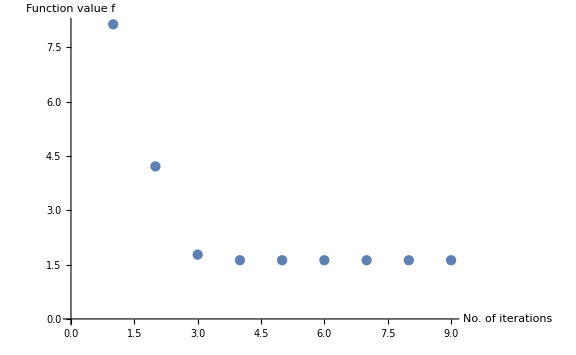

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
Result[[1,All]]
```

{1.62036,1.62036}

#### Case 1.4.4: N=100, m=1/10, δ=1, dimS=8, l=3

```mathematica
CM0=partialCM[100,1/10,1,3,8,8];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311
-0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
GOExtractStdFormG[CM0]
```

Dot::dotsh: Tensors … and {{-5.26449×10^-6,-0.000057478,0.000282236,0.000441272,0.00141205,0.0120652,-0.0435582,-0.12277,0.208618,0.427908,-0.382566,-0.68434,0.264001,0.49507,«5»,-0.361686,0.168656,0.261136,0.135471,0.200212,-0.206771,-0.362514,0.0814281,0.182555,-0.010686,-0.0366386,0.000235079,0.00221991},«30»,{«1»}} have incompatible shapes.

Same problem here.

```mathematica
Length[CM0]
```

32

```mathematica
GOTransformGtoJ[CM0,"qpqp","qpqp"]//Eigenvalues//Chop
```

{0.+1.42288 ⅈ,0.-1.42288 ⅈ,0.+1.21872 ⅈ,0.-1.21872 ⅈ,0.+1.17747 ⅈ,0.-1.17747 ⅈ,0.+1.06639 ⅈ,0.-1.06639 ⅈ,0.+1.00173 ⅈ,0.-1.00173 ⅈ,0.+1.00136 ⅈ,0.-1.00136 ⅈ,0.+1.00016 ⅈ,0.-1.00016 ⅈ,0.+1.00001 ⅈ,0.-1.00001 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

The problem is that there are many identical symplectic eigenvalues. We need to make a smart diagonalization. Here, we follow the discussion in https://math.stackexchange.com/questions/1171842/finding-the-symplectic-matrix-in-williamsons-theorem based on SchurDecomposition.

```mathematica
sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;
```

```mathematica
MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]]//Chop;
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm
```

{0.444996,0.324944,0.293647,0.181198,0.0293967,0.0261046,0.00892831,0.00171684,0.00131552,0.000082758,0.0000688818,2.83334×10^-6,2.56181×10^-6,6.40923×10^-8,5.67419×10^-8,1.05367×10^-8}

(1.42288 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.42288 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.21872 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.21872 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.17747 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.17747 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.06639 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.06639 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00173 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00173 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00136 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00136 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00016 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00016 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

The correct thing to do seems to do the Schur decomposition with respect to GOΩqpqp[16] and not GOTransformGtoJ[CM0,”qpqp”,”qpqp”].

```mathematica
Det[MTra.CM0.Transpose[MTra]]//Simplify
```

4.77204

```mathematica
JT=GOPurifyStandardJBoson[rlist,(8+8),"qpqp"]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[4(8+8)],"qpqp","qpqp"]//Chop;
```

We do the minimization with 10 randomly generated initial matrices M0:

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{8,8},"GOSpBasis"]}}]//SparseArray,{10}];
```

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];ProblemSpecific={function,gradient};
```

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{8,8,8,8}];
metric=GOMetricSp[LieBasis,JR0];
SystemSpecific={JR0,M0List,LieBasis,metric};
```

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 784.022

Final value: {1.62771}

Number of iterations: {9}

Number of total corrections: 1

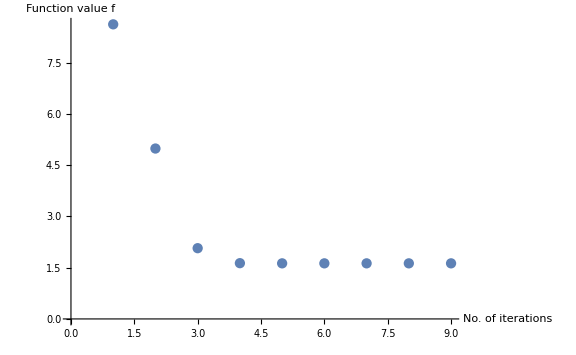

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
Result[[1,All]]
```

{1.62771}

#### Case 1.4.5: N=100, m=1/10, δ=1, dimS=8, l=5

```mathematica
CM0=partialCM[100,1/10,1,5,8,8];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
GOExtractStdFormG[CM0][[2]]//MatrixForm
```

(0. | 0.234514 | 0. | 0.0671801 | 0. | 0.0408398 | 0. | 0.0350631 | 0. | 0.0391537 | 0. | 0.0553236 | 0. | 0.103273 | 0. | 0.376851 | 0. | 0.376851 | 0. | 0.103273 | 0. | 0.0553236 | 0. | 0.0391537 | 0. | 0.0350631 | 0. | 0.0408398 | 0. | 0.0671801 | 0. | 0.234514
-0.437337 | 0. | -0.395043 | 0. | -0.384602 | 0. | -0.393316 | 0. | -0.418624 | 0. | -0.46239 | 0. | -0.531803 | 0. | -0.64882 | 0. | -0.64882 | 0. | -0.531803 | 0. | -0.46239 | 0. | -0.418624 | 0. | -0.393316 | 0. | -0.384602 | 0. | -0.395043 | 0. | -0.437337 | 0.
0. | 0.502367 | 0. | 0.125329 | 0. | 0.0604663 | 0. | 0.0366516 | 0. | 0.0262613 | 0. | 0.0237212 | 0. | 0.0335002 | 0. | 0.12975 | 0. | -0.12975 | 0. | -0.0335002 | 0. | -0.0237212 | 0. | -0.0262613 | 0. | -0.0366516 | 0. | -0.0604663 | 0. | -0.125329 | 0. | -0.502367
-0.692715 | 0. | -0.515172 | 0. | -0.408548 | 0. | -0.335113 | 0. | -0.282215 | 0. | -0.245087 | 0. | -0.224025 | 0. | -0.229063 | 0. | 0.229063 | 0. | 0.224025 | 0. | 0.245087 | 0. | 0.282215 | 0. | 0.335113 | 0. | 0.408548 | 0. | 0.515172 | 0. | 0.692715 | 0.
0. | 0.489751 | 0. | 0.113759 | 0. | 0.0465653 | 0. | 0.0174407 | 0. | -0.00336005 | 0. | -0.0281802 | 0. | -0.0797647 | 0. | -0.349926 | 0. | -0.349926 | 0. | -0.0797647 | 0. | -0.0281802 | 0. | -0.00336005 | 0. | 0.0174407 | 0. | 0.0465653 | 0. | 0.113759 | 0. | 0.489751
-0.585265 | 0. | -0.374215 | 0. | -0.232261 | 0. | -0.11693 | 0. | -0.0110686 | 0. | 0.0971302 | 0. | 0.221713 | 0. | 0.393101 | 0. | 0.393101 | 0. | 0.221713 | 0. | 0.0971302 | 0. | -0.0110686 | 0. | -0.11693 | 0. | -0.232261 | 0. | -0.374215 | 0. | -0.585265 | 0.
0. | 0.211454 | 0. | 0.0452885 | 0. | 0.0150599 | 0. | -0.0000417984 | 0. | -0.0147915 | 0. | -0.0402495 | 0. | -0.111982 | 0. | -0.59731 | 0. | 0.59731 | 0. | 0.111982 | 0. | 0.0402495 | 0. | 0.0147915 | 0. | 0.0000417984 | 0. | -0.0150599 | 0. | -0.0452885 | 0. | -0.211454
-0.201333 | 0. | -0.0880285 | 0. | -0.00390526 | 0. | 0.0738766 | 0. | 0.157294 | 0. | 0.25939 | 0. | 0.404284 | 0. | 0.661866 | 0. | -0.661866 | 0. | -0.404284 | 0. | -0.25939 | 0. | -0.157294 | 0. | -0.0738766 | 0. | 0.00390526 | 0. | 0.0880285 | 0. | 0.201333 | 0.
0.000335713 | -0.00373528 | -0.0192017 | 0.0664266 | 0.146563 | -0.322865 | -0.358583 | 0.647584 | 0.320402 | -0.581158 | -0.0732994 | 0.200145 | -0.00886809 | -0.00253486 | 0.0010374 | -0.00524255 | -0.00157614 | 0.0105105 | 0.0334224 | -0.0760661 | -0.084247 | 0.131841 | 0.013063 | -0.0221543 | 0.0737879 | -0.114769 | -0.0493551 | 0.0968972 | 0.00925381 | -0.0273969 | -0.000288827 | 0.0022724
0.000310093 | 0.00358698 | -0.0187987 | -0.0656731 | 0.146188 | 0.322684 | -0.359727 | -0.648683 | 0.318953 | 0.577762 | -0.0679713 | -0.191674 | -0.0111643 | -0.00252481 | 0.00115606 | 0.00599601 | -0.00165002 | -0.0109727 | 0.0347227 | 0.0785077 | -0.0853784 | -0.131826 | 0.00690209 | 0.0113472 | 0.0821875 | 0.129434 | -0.0524421 | -0.103959 | 0.00950556 | 0.0285393 | -0.000285418 | -0.00229109
0. | -0.412391 | 0. | 0.19637 | 0. | 0.190209 | 0. | 0.166034 | 0. | 0.153456 | 0. | 0.152672 | 0. | 0.140327 | 0. | -0.377825 | 0. | -0.377825 | 0. | 0.140327 | 0. | 0.152672 | 0. | 0.153456 | 0. | 0.166034 | 0. | 0.190209 | 0. | 0.19637 | 0. | -0.412391
0.185262 | 0. | -0.273519 | 0. | -0.411098 | 0. | -0.443988 | 0. | -0.425588 | 0. | -0.362204 | 0. | -0.218433 | 0. | 0.176583 | 0. | 0.176583 | 0. | -0.218433 | 0. | -0.362204 | 0. | -0.425588 | 0. | -0.443988 | 0. | -0.411098 | 0. | -0.273519 | 0. | 0.185262 | 0.
0. | -0.47517 | 0. | 0.293493 | 0. | 0.245178 | 0. | 0.179947 | 0. | 0.128781 | 0. | 0.0868494 | 0. | 0.0369002 | 0. | -0.211328 | 0. | 0.211328 | 0. | -0.0369002 | 0. | -0.0868494 | 0. | -0.128781 | 0. | -0.179947 | 0. | -0.245178 | 0. | -0.293493 | 0. | 0.47517
0.20227 | 0. | -0.363746 | 0. | -0.480839 | 0. | -0.460666 | 0. | -0.384107 | 0. | -0.275656 | 0. | -0.133994 | 0. | 0.0851433 | 0. | -0.0851433 | 0. | 0.133994 | 0. | 0.275656 | 0. | 0.384107 | 0. | 0.460666 | 0. | 0.480839 | 0. | 0.363746 | 0. | -0.20227 | 0.
0.0962867 | 0. | -0.329191 | 0. | -0.277246 | 0. | -0.0937301 | 0. | 0.126177 | 0. | 0.324427 | 0. | 0.389503 | 0. | -0.129946 | 0. | -0.129946 | 0. | 0.389503 | 0. | 0.324427 | 0. | 0.126177 | 0. | -0.0937301 | 0. | -0.277246 | 0. | -0.329191 | 0. | 0.0962867 | 0.
0. | 0.279111 | 0. | -0.35147 | 0. | -0.212338 | 0. | -0.0706449 | 0. | 0.0686697 | 0. | 0.23047 | 0. | 0.416681 | 0. | -0.35553 | 0. | -0.35553 | 0. | 0.416681 | 0. | 0.23047 | 0. | 0.0686697 | 0. | -0.0706449 | 0. | -0.212338 | 0. | -0.35147 | 0. | 0.279111
-0.0105389 | -0.0615852 | 0.180174 | 0.395721 | -0.407975 | -0.625156 | 0.00835601 | 0.0478817 | 0.267682 | 0.315574 | 0.149431 | 0.149499 | -0.146095 | -0.270672 | 0.00994424 | 0.0560431 | 0.00071277 | -0.000314659 | 0.0116264 | 0.0371813 | -0.0612194 | -0.0996571 | 0.0384338 | 0.0685803 | 0.0250662 | 0.0513645 | -0.0820947 | -0.135809 | 0.0454295 | 0.0917417 | -0.00356892 | -0.0179519
0.0104861 | -0.0613282 | -0.179528 | 0.394481 | 0.406935 | -0.623508 | -0.00812784 | 0.0471915 | -0.267727 | 0.315717 | -0.149344 | 0.14932 | 0.145977 | -0.270498 | -0.00992681 | 0.0559784 | -0.000575059 | -0.00115507 | -0.0141054 | 0.0425974 | 0.066743 | -0.108295 | -0.0391156 | 0.0702915 | -0.0282602 | 0.0558452 | 0.0827015 | -0.137675 | -0.044995 | 0.0912162 | 0.00352327 | -0.0177396
0.0401154 | 0. | -0.229577 | 0. | -0.134361 | 0. | 0.0409665 | 0. | 0.235844 | 0. | 0.416152 | 0. | 0.482781 | 0. | -0.130989 | 0. | 0.130989 | 0. | -0.482781 | 0. | -0.416152 | 0. | -0.235844 | 0. | -0.0409665 | 0. | 0.134361 | 0. | 0.229577 | 0. | -0.0401154 | 0.
0. | 0.146476 | 0. | -0.276698 | 0. | -0.135638 | 0. | -0.0194521 | 0. | 0.0945235 | 0. | 0.248547 | 0. | 0.484975 | 0. | -0.406979 | 0. | 0.406979 | 0. | -0.484975 | 0. | -0.248547 | 0. | -0.0945235 | 0. | 0.0194521 | 0. | 0.135638 | 0. | 0.276698 | 0. | -0.146476
-0.0391949 | 0.170109 | 0.342178 | -0.53237 | -0.0979723 | 0.103281 | -0.329696 | 0.275767 | -0.317632 | 0.254704 | -0.0901981 | 0.0697081 | 0.271658 | -0.432198 | -0.0263287 | 0.12524 | -0.00284339 | 0.0129351 | 0.0257195 | -0.0411136 | -0.0174589 | 0.0354685 | 0.00459197 | -0.00628268 | 0.0137545 | -0.0200112 | -0.00922208 | 0.0195719 | 0.00471863 | -0.00912214 | -0.000690884 | 0.00252779
-0.0392176 | -0.170119 | 0.342413 | 0.532469 | -0.0981137 | -0.103324 | -0.330166 | -0.276279 | -0.317395 | -0.2541 | -0.0900925 | -0.0695824 | 0.271627 | 0.431869 | -0.0263298 | -0.125166 | -0.00282726 | -0.0128424 | 0.0254893 | 0.040598 | -0.016941 | -0.034548 | 0.00425942 | 0.0057137 | 0.0134986 | 0.0195001 | -0.00848624 | -0.0183429 | 0.00433906 | 0.00833609 | -0.000662133 | -0.00237973
-0.00195069 | -0.0099961 | 0.0241028 | 0.0426225 | -0.0193594 | -0.0186513 | -0.0404447 | -0.0475922 | -0.000741428 | 0.00307455 | 0.0375166 | 0.0632917 | -0.0282909 | -0.0518352 | 0.0024571 | 0.012361 | 0.0255692 | 0.12091 | -0.260996 | -0.413896 | 0.0852603 | 0.070516 | 0.288987 | 0.219334 | 0.323393 | 0.265999 | 0.132733 | 0.157634 | -0.353996 | -0.560592 | 0.0396735 | 0.173475
0.00200899 | -0.0102736 | -0.0247195 | 0.0437056 | 0.0198145 | -0.0191137 | 0.0414538 | -0.0489482 | 0.000389472 | 0.00374548 | -0.0380764 | 0.0640436 | 0.0284627 | -0.0523018 | -0.00245824 | 0.0124009 | -0.0255641 | 0.120957 | 0.261097 | -0.414503 | -0.0862558 | 0.0723495 | -0.287967 | 0.218102 | -0.322245 | 0.264547 | -0.13379 | 0.159599 | 0.354034 | -0.561187 | -0.0396547 | 0.173496
-0.00525061 | -0.0244036 | 0.0521665 | 0.0787961 | 0.00905296 | 0.0713978 | -0.209638 | -0.292076 | -0.00828868 | -0.0346155 | 0.283958 | 0.432883 | -0.119546 | -0.267689 | 0.00581743 | 0.0382077 | -0.00160064 | -0.00522026 | -0.00307677 | -0.0499265 | 0.161305 | 0.31125 | -0.224422 | -0.287879 | -0.2043 | -0.279962 | 0.242912 | 0.422641 | -0.0300988 | -0.118397 | -0.00202558 | -0.000616831
0.00540229 | -0.0251811 | -0.0541648 | 0.0828604 | -0.0054764 | 0.0658842 | 0.20992 | -0.292629 | 0.00406362 | -0.0274118 | -0.280295 | 0.426135 | 0.118521 | -0.265131 | -0.00577488 | 0.0379116 | 0.00154494 | -0.00476536 | 0.00469311 | -0.0538106 | -0.165822 | 0.317934 | 0.223872 | -0.286788 | 0.209396 | -0.286717 | -0.241628 | 0.421957 | 0.027614 | -0.114233 | 0.00226673 | -0.00174383
-0.00185074 | 0.00673919 | 0.00781751 | 0.00297402 | 0.0503243 | -0.0987095 | -0.0854526 | 0.117861 | -0.0440573 | 0.0546058 | 0.0772279 | -0.137061 | -0.0355369 | 0.0739654 | 0.00325017 | -0.0149969 | 0.0134761 | -0.0773208 | -0.209566 | 0.412099 | 0.303859 | -0.398435 | 0.225253 | -0.245607 | -0.11436 | 0.141407 | -0.309709 | 0.438893 | 0.157732 | -0.33454 | -0.00962269 | 0.055331
-0.00182917 | -0.00655036 | 0.00704136 | -0.00507079 | 0.0534956 | 0.104332 | -0.0881092 | -0.122199 | -0.0452276 | -0.0556833 | 0.0782241 | 0.138991 | -0.0354267 | -0.0741402 | 0.00322318 | 0.014903 | 0.013446 | 0.0772463 | -0.209327 | -0.412129 | 0.304081 | 0.399012 | 0.225409 | 0.247025 | -0.117563 | -0.146902 | -0.306743 | -0.433839 | 0.15708 | 0.332958 | -0.00960811 | -0.0552211
-0.000714986 | -0.00560375 | 0.0222229 | 0.0630436 | -0.104081 | -0.18826 | 0.092792 | 0.103444 | 0.189359 | 0.335534 | -0.316561 | -0.534806 | 0.108867 | 0.257492 | -0.00496277 | -0.0334008 | 0.00445206 | 0.0298185 | -0.0958851 | -0.222189 | 0.258953 | 0.42147 | -0.0978643 | -0.172155 | -0.149526 | -0.214261 | 0.113242 | 0.217367 | -0.0204964 | -0.0621584 | 0.000525673 | 0.00469562
0.000762798 | -0.00593907 | -0.0234365 | 0.0663263 | 0.109344 | -0.198437 | -0.100436 | 0.116824 | -0.185953 | 0.32854 | 0.317139 | -0.534801 | -0.109389 | 0.258522 | 0.00499429 | -0.0335872 | -0.00444756 | 0.0298623 | 0.0963531 | -0.224236 | -0.26444 | 0.434458 | 0.114882 | -0.204277 | 0.128327 | -0.175814 | -0.101913 | 0.194234 | 0.0182552 | -0.0557481 | -0.000446832 | 0.00411254
-5.99361×10^-6 | 0.0000693325 | -0.000579383 | -0.0022021 | 0.00527679 | 0.0122519 | -0.0162183 | -0.0327908 | 0.0275992 | 0.0513958 | -0.024322 | -0.0445565 | 0.00711347 | 0.0176489 | -0.00029832 | -0.00208647 | -0.000345518 | -0.00372871 | 0.0189688 | 0.0649193 | -0.140855 | -0.307502 | 0.337281 | 0.616681 | -0.32688 | -0.603971 | 0.133463 | 0.293235 | -0.0193703 | -0.0634302 | 0.000453752 | 0.00419318
0.0000464375 | -0.000280826 | -0.000945996 | 0.00246368 | 0.00342123 | -0.00480688 | 0.00335147 | -0.0134028 | -0.0319926 | 0.0591641 | 0.0420514 | -0.07275 | -0.0139626 | 0.033351 | 0.00061737 | -0.00422836 | -0.000022806 | -0.00134671 | -0.0115778 | 0.0483492 | 0.122871 | -0.278954 | -0.33295 | 0.607779 | 0.336313 | -0.617315 | -0.137923 | 0.302891 | 0.0195868 | -0.0649056 | -0.000432931 | 0.00414645)

Nan desu ka? It works?

```mathematica
GOExtractStdFormG[CM0][[1]]
```

{0.434621,0.332487,0.28977,0.226758,0.0975131,0.0325815,0.0266132,0.0135998,0.012295,0.00515799,0.00345536,0.+0.0028214 ⅈ,0.+0.0072301 ⅈ,0.+0.0103954 ⅈ,0.+0.0489297 ⅈ,0.+0.0803398 ⅈ}

But, aren’t the r[i]s supposed to be real?

```mathematica
Det[GOExtractStdFormG[CM0][[2]]]
```

0.999863

```mathematica
GOExtractStdFormG[CM0][[2]].CM0.Transpose[GOExtractStdFormG[CM0][[2]]]//Chop//MatrixForm
```

(1.40219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.40219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.22936 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.22936 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.17269 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.17269 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.10461 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.10461 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.01826 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.01908 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00212 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00212 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00037 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00037 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00029 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.0003 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00005 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00005 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00002 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00002 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999984 | 7.4225×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.4225×10^-9 | 0.999984 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999893 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999895 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999784 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999782 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.993973 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.995216 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.987119 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.986678)

```mathematica
(*{rlist,MTra}=GOExtractStdFormG[CM0]*)
```

We will check whether we obtain the same transformations from the Schur decomposition:

```mathematica
GOTransformGtoJ[CM0,"qpqp","qpqp"]//Eigenvalues//Chop
```

{0.+1.40219 ⅈ,0.-1.40219 ⅈ,0.+1.22936 ⅈ,0.-1.22936 ⅈ,0.+1.17269 ⅈ,0.-1.17269 ⅈ,0.+1.10461 ⅈ,0.-1.10461 ⅈ,0.+1.00212 ⅈ,0.-1.00212 ⅈ,0.+1.00142 ⅈ,0.-1.00142 ⅈ,0.+1.00037 ⅈ,0.-1.00037 ⅈ,0.+1.00005 ⅈ,0.-1.00005 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

The problem is that there are many identical symplectic eigenvalues. We need to make a smart diagonalization. Here, we follow the discussion in https://math.stackexchange.com/questions/1171842/finding-the-symplectic-matrix-in-williamsons-theorem based on SchurDecomposition.

```mathematica
sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;
```

```mathematica
MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]]//Chop;MTra//MatrixForm//Chop
Det[MTra]
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm
```

(0.095464 | 0.228859 | 0.0862318 | 0.06556 | 0.0839526 | 0.039855 | 0.0858549 | 0.0342176 | 0.0913791 | 0.0382095 | 0.100933 | 0.0539895 | 0.116084 | 0.100783 | 0.141627 | 0.367764 | 0.141627 | 0.367764 | 0.116084 | 0.100783 | 0.100933 | 0.0539895 | 0.0913791 | 0.0382095 | 0.0858549 | 0.0342176 | 0.0839526 | 0.039855 | 0.0862318 | 0.06556 | 0.095464 | 0.228859
-0.426791 | 0.0511908 | -0.385516 | 0.0146644 | -0.375327 | 0.00891471 | -0.383832 | 0.00765374 | -0.408529 | 0.00854665 | -0.451239 | 0.0120763 | -0.518978 | 0.0225429 | -0.633174 | 0.0822609 | -0.633174 | 0.0822609 | -0.518978 | 0.0225429 | -0.451239 | 0.0120763 | -0.408529 | 0.00854665 | -0.383832 | 0.00765374 | -0.375327 | 0.00891471 | -0.385516 | 0.0146644 | -0.426791 | 0.0511908
-0.0653983 | -0.500124 | -0.0486366 | -0.124769 | -0.0385705 | -0.0601962 | -0.0316375 | -0.0364879 | -0.0266435 | -0.026144 | -0.0231384 | -0.0236152 | -0.0211499 | -0.0333506 | -0.0216255 | -0.12917 | 0.0216255 | 0.12917 | 0.0211499 | 0.0333506 | 0.0231384 | 0.0236152 | 0.0266435 | 0.026144 | 0.0316375 | 0.0364879 | 0.0385705 | 0.0601962 | 0.0486366 | 0.124769 | 0.0653983 | 0.500124
-0.689621 | 0.0474278 | -0.512871 | 0.0118321 | -0.406724 | 0.00570853 | -0.333616 | 0.00346023 | -0.280955 | 0.0024793 | -0.243993 | 0.00223948 | -0.223024 | 0.00316271 | -0.22804 | 0.0122495 | 0.22804 | -0.0122495 | 0.223024 | -0.00316271 | 0.243993 | -0.00223948 | 0.280955 | -0.0024793 | 0.333616 | -0.00346023 | 0.406724 | -0.00570853 | 0.512871 | -0.0118321 | 0.689621 | -0.0474278
0.446987 | 0.316149 | 0.285801 | 0.0734347 | 0.177386 | 0.0300593 | 0.0893034 | 0.0112585 | 0.00845348 | -0.00216901 | -0.0741817 | -0.0181912 | -0.16933 | -0.0514905 | -0.300225 | -0.225888 | -0.300225 | -0.225888 | -0.16933 | -0.0514905 | -0.0741817 | -0.0181912 | 0.00845348 | -0.00216901 | 0.0893034 | 0.0112585 | 0.177386 | 0.0300593 | 0.285801 | 0.0734347 | 0.446987 | 0.316149
0.377806 | -0.37404 | 0.241567 | -0.0868815 | 0.149932 | -0.0355636 | 0.0754818 | -0.01332 | 0.00714512 | 0.00256618 | -0.0627005 | 0.0215222 | -0.143123 | 0.0609191 | -0.253759 | 0.267251 | -0.253759 | 0.267251 | -0.143123 | 0.0609191 | -0.0627005 | 0.0215222 | 0.00714512 | 0.00256618 | 0.0754818 | -0.01332 | 0.149932 | -0.0355636 | 0.241567 | -0.0868815 | 0.377806 | -0.37404
-0.1557 | 0.13406 | -0.0680762 | 0.0287124 | -0.0030201 | 0.00954779 | 0.0571319 | -0.0000264997 | 0.121642 | -0.00937763 | 0.200597 | -0.0255178 | 0.31265 | -0.0709956 | 0.511849 | -0.378688 | -0.511849 | 0.378688 | -0.31265 | 0.0709956 | -0.200597 | 0.0255178 | -0.121642 | 0.00937763 | -0.0571319 | 0.0000264997 | 0.0030201 | -0.00954779 | 0.0680762 | -0.0287124 | 0.1557 | -0.13406
-0.127643 | -0.163526 | -0.0558091 | -0.0350235 | -0.00247589 | -0.0116464 | 0.046837 | 0.0000323244 | 0.099723 | 0.0114389 | 0.16445 | 0.0311267 | 0.256311 | 0.0866007 | 0.419616 | 0.461925 | -0.419616 | -0.461925 | -0.256311 | -0.0866007 | -0.16445 | -0.0311267 | -0.099723 | -0.0114389 | -0.046837 | -0.0000323244 | 0.00247589 | 0.0116464 | 0.0558091 | 0.0350235 | 0.127643 | 0.163526
-0.0973978 | 0.3508 | 0.143797 | -0.167042 | 0.216127 | -0.161802 | 0.233418 | -0.141237 | 0.223745 | -0.130538 | 0.190422 | -0.12987 | 0.114837 | -0.119369 | -0.092835 | 0.321397 | -0.092835 | 0.321397 | 0.114837 | -0.119369 | 0.190422 | -0.12987 | 0.223745 | -0.130538 | 0.233418 | -0.141237 | 0.216127 | -0.161802 | 0.143797 | -0.167042 | -0.0973978 | 0.3508
0.157593 | 0.216807 | -0.232669 | -0.103238 | -0.349701 | -0.099999 | -0.377679 | -0.0872894 | -0.362027 | -0.0806768 | -0.308109 | -0.0802643 | -0.185811 | -0.0737743 | 0.15021 | 0.198634 | 0.15021 | 0.198634 | -0.185811 | -0.0737743 | -0.308109 | -0.0802643 | -0.362027 | -0.0806768 | -0.377679 | -0.0872894 | -0.349701 | -0.099999 | -0.232669 | -0.103238 | 0.157593 | 0.216807
-0.167493 | -0.266394 | 0.301206 | 0.164541 | 0.398167 | 0.137454 | 0.381462 | 0.100884 | 0.318067 | 0.0721983 | 0.228262 | 0.0486903 | 0.110956 | 0.0206873 | -0.0705044 | -0.118476 | 0.0705044 | 0.118476 | -0.110956 | -0.0206873 | -0.228262 | -0.0486903 | -0.318067 | -0.0721983 | -0.381462 | -0.100884 | -0.398167 | -0.137454 | -0.301206 | -0.164541 | 0.167493 | 0.266394
-0.113399 | 0.393473 | 0.203926 | -0.243032 | 0.269572 | -0.203024 | 0.258263 | -0.149008 | 0.215342 | -0.106639 | 0.154541 | -0.0719171 | 0.0751211 | -0.0305559 | -0.0477338 | 0.174994 | 0.0477338 | -0.174994 | -0.0751211 | 0.0305559 | -0.154541 | 0.0719171 | -0.215342 | 0.106639 | -0.258263 | 0.149008 | -0.269572 | 0.203024 | -0.203926 | 0.243032 | 0.113399 | -0.393473
-0.0625403 | -0.21222 | 0.213817 | 0.267238 | 0.180077 | 0.161449 | 0.0608798 | 0.0537143 | -0.0819549 | -0.0522125 | -0.210722 | -0.175236 | -0.252991 | -0.316821 | 0.0844028 | 0.270324 | 0.0844028 | 0.270324 | -0.252991 | -0.316821 | -0.210722 | -0.175236 | -0.0819549 | -0.0522125 | 0.0608798 | 0.0537143 | 0.180077 | 0.161449 | 0.213817 | 0.267238 | -0.0625403 | -0.21222
0.0732109 | -0.181289 | -0.250298 | 0.228288 | -0.210802 | 0.137918 | -0.071267 | 0.0458854 | 0.095938 | -0.0446025 | 0.246675 | -0.149695 | 0.296156 | -0.270644 | -0.0988035 | 0.230924 | -0.0988035 | 0.230924 | 0.296156 | -0.270644 | 0.246675 | -0.149695 | 0.095938 | -0.0446025 | -0.071267 | 0.0458854 | -0.210802 | 0.137918 | -0.250298 | 0.228288 | 0.0732109 | -0.181289
0.0309591 | 0.0931477 | -0.177176 | -0.17596 | -0.103693 | -0.0862554 | 0.0316159 | -0.0123701 | 0.182013 | 0.0601099 | 0.321166 | 0.158057 | 0.372587 | 0.308408 | -0.101091 | -0.258808 | 0.101091 | 0.258808 | -0.372587 | -0.308408 | -0.321166 | -0.158057 | -0.182013 | -0.0601099 | -0.0316159 | 0.0123701 | 0.103693 | 0.0862554 | 0.177176 | 0.17596 | -0.0309591 | -0.0931477
-0.0255104 | 0.113043 | 0.145994 | -0.213542 | 0.0854435 | -0.104678 | -0.0260516 | -0.0150122 | -0.149979 | 0.0729485 | -0.264642 | 0.191816 | -0.307013 | 0.37428 | 0.0832995 | -0.314086 | -0.0832995 | 0.314086 | 0.307013 | -0.37428 | 0.264642 | -0.191816 | 0.149979 | -0.0729485 | 0.0260516 | 0.0150122 | -0.0854435 | 0.104678 | -0.145994 | 0.213542 | 0.0255104 | -0.113043
-0.0204426 | -0.151229 | 0.180546 | 0.482661 | -0.0611785 | -0.114279 | -0.177554 | -0.264384 | -0.149011 | -0.201851 | -0.0194458 | -0.00286155 | 0.128713 | 0.333173 | -0.0132501 | -0.104737 | -0.0132501 | -0.104737 | 0.128713 | 0.333173 | -0.0194458 | -0.00286155 | -0.149011 | -0.201851 | -0.177554 | -0.264384 | -0.0611785 | -0.114279 | 0.180546 | 0.482661 | -0.0204426 | -0.151229
0.0347314 | -0.0890118 | -0.306744 | 0.28409 | 0.103941 | -0.0672633 | 0.30166 | -0.155614 | 0.253166 | -0.118807 | 0.0330379 | -0.00168428 | -0.218679 | 0.196103 | 0.0225116 | -0.0616471 | 0.0225116 | -0.0616471 | -0.218679 | 0.196103 | 0.0330379 | -0.00168428 | 0.253166 | -0.118807 | 0.30166 | -0.155614 | 0.103941 | -0.0672633 | -0.306744 | 0.28409 | 0.0347314 | -0.0890118
0.0283474 | -0.124163 | -0.252998 | 0.398088 | 0.0846086 | -0.0911116 | 0.25016 | -0.215375 | 0.217315 | -0.169847 | 0.0429394 | -0.0149076 | -0.169716 | 0.267122 | 0.0165116 | -0.0782783 | -0.0165116 | 0.0782783 | 0.169716 | -0.267122 | -0.0429394 | 0.0149076 | -0.217315 | 0.169847 | -0.25016 | 0.215375 | -0.0846086 | 0.0911116 | 0.252998 | -0.398088 | -0.0283474 | 0.124163
0.0283474 | 0.124163 | -0.252998 | -0.398088 | 0.0846086 | 0.0911116 | 0.25016 | 0.215375 | 0.217315 | 0.169847 | 0.0429394 | 0.0149076 | -0.169716 | -0.267122 | 0.0165116 | 0.0782783 | -0.0165116 | -0.0782783 | 0.169716 | 0.267122 | -0.0429394 | -0.0149076 | -0.217315 | -0.169847 | -0.25016 | -0.215375 | -0.0846086 | -0.0911116 | 0.252998 | 0.398088 | -0.0283474 | -0.124163
0 | 0.0474333 | 3.52975×10^-10 | -0.305224 | 2.67001×10^-9 | 0.412478 | -9.73434×10^-9 | 0.154355 | 5.40388×10^-9 | -0.258513 | 5.05896×10^-9 | -0.429772 | -4.06829×10^-9 | 0.470486 | 3.32837×10^-10 | -0.0967629 | 7.10066×10^-10 | -0.0967629 | -1.10091×10^-8 | 0.470486 | 1.86054×10^-8 | -0.429772 | 4.20338×10^-9 | -0.258513 | -5.24344×10^-9 | 0.154355 | -9.14189×10^-9 | 0.412479 | 4.77334×10^-9 | -0.305224 | -2.72553×10^-10 | 0.0474333
-0.00783073 | -2.31572×10^-10 | 0.140802 | 0 | -0.293883 | 6.82008×10^-9 | -0.115538 | -1.6171×10^-8 | 0.238909 | 8.97272×10^-9 | 0.320995 | 6.58419×10^-9 | -0.246838 | -7.64649×10^-9 | 0.0180694 | 1.67522×10^-9 | 0.0180694 | 4.0365×10^-9 | -0.246838 | -2.22653×10^-8 | 0.320995 | 2.72837×10^-8 | 0.238909 | 1.23536×10^-9 | -0.115538 | -6.18037×10^-9 | -0.293883 | -1.22681×10^-8 | 0.140802 | 1.01361×10^-8 | -0.00783073 | -1.63389×10^-9
-0.00671694 | -0.0257776 | 0.132994 | 0.182237 | -0.32485 | -0.292952 | -0.0274488 | -0.0166064 | 0.255047 | 0.174842 | 0.199656 | 0.136216 | -0.158187 | -0.184798 | 0.00940444 | 0.0344647 | -0.00940444 | -0.0344647 | 0.158187 | 0.184798 | -0.199656 | -0.136217 | -0.255046 | -0.174841 | 0.0274484 | 0.016606 | 0.32485 | 0.292952 | -0.132994 | -0.182238 | 0.00671694 | 0.0257776
0.00406104 | -0.0426361 | -0.0804079 | 0.30142 | 0.196403 | -0.484542 | 0.0165954 | -0.0274669 | -0.1542 | 0.289187 | -0.120711 | 0.225301 | 0.0956393 | -0.305655 | -0.00568589 | 0.0570046 | 0.00568589 | -0.0570045 | -0.0956393 | 0.305655 | 0.120711 | -0.225302 | 0.1542 | -0.289187 | -0.0165952 | 0.0274663 | -0.196403 | 0.484542 | 0.0804079 | -0.30142 | -0.00406104 | 0.0426361
-0.00296436 | 0.0126638 | 0.071381 | -0.112788 | -0.2589 | 0.281053 | 0.205536 | -0.192123 | 0.174975 | -0.158308 | -0.250958 | 0.268456 | 0.0724115 | -0.112584 | -0.00312754 | 0.0131041 | -0.00312756 | 0.0131042 | 0.0724118 | -0.112585 | -0.250959 | 0.268457 | 0.174974 | -0.158308 | 0.205536 | -0.192124 | -0.2589 | 0.281053 | 0.0713811 | -0.112789 | -0.00296436 | 0.0126638
0.00183206 | 0.0204906 | -0.0441156 | -0.182497 | 0.160008 | 0.454755 | -0.127027 | -0.310863 | -0.10814 | -0.256149 | 0.1551 | 0.434374 | -0.0447525 | -0.182166 | 0.00193292 | 0.0212031 | 0.00193293 | 0.0212032 | -0.0447527 | -0.182167 | 0.1551 | 0.434375 | -0.108139 | -0.256149 | -0.127028 | -0.310865 | 0.160008 | 0.454756 | -0.0441157 | -0.182497 | 0.00183206 | 0.0204906
-0.000592431 | -0.00790958 | 0.021506 | 0.102326 | -0.120545 | -0.374934 | 0.189665 | 0.474316 | 0.00338812 | 0.000661888 | -0.17214 | -0.413443 | 0.0710231 | 0.251153 | -0.00343127 | -0.0354879 | 0.00343106 | 0.0354845 | -0.0710143 | -0.251105 | 0.172084 | 0.413242 | -0.00326724 | -0.000284952 | -0.189777 | -0.47467 | 0.12059 | 0.375101 | -0.0215125 | -0.102362 | 0.00059259 | 0.00791199
-0.000930259 | 0.00503719 | 0.0337693 | -0.0651664 | -0.189282 | 0.23878 | 0.297806 | -0.302084 | 0.00534624 | -0.000391424 | -0.270322 | 0.263275 | 0.111529 | -0.159937 | -0.00538815 | 0.0225993 | 0.00538778 | -0.0225973 | -0.111514 | 0.159909 | 0.270227 | -0.263157 | -0.00513996 | 0.0001705 | -0.297996 | 0.302292 | 0.189358 | -0.238879 | -0.0337803 | 0.0651876 | 0.000930527 | -0.00503862
-0.0001937 | -0.00378743 | 0.00779159 | 0.0557635 | -0.0531231 | -0.257803 | 0.131977 | 0.539876 | -0.141915 | -0.570767 | 0.0647531 | 0.302767 | -0.0102214 | -0.0711788 | 0.000247761 | 0.0049755 | 0.000258477 | 0.00517242 | -0.010485 | -0.0729455 | 0.0657295 | 0.307616 | -0.143117 | -0.576701 | 0.132593 | 0.543478 | -0.0532493 | -0.258866 | 0.00779868 | 0.0558931 | -0.000193685 | -0.00379127
0.000426351 | -0.00172078 | -0.0171484 | 0.0253381 | 0.116903 | -0.117157 | -0.290373 | 0.245388 | 0.31214 | -0.259498 | -0.142347 | 0.137707 | 0.0224502 | -0.0323939 | -0.000543401 | 0.00226672 | -0.000571184 | 0.00234241 | 0.0231391 | -0.0330665 | -0.144937 | 0.139526 | 0.315415 | -0.261675 | -0.292131 | 0.246664 | 0.117297 | -0.117511 | -0.0171767 | 0.0253757 | 0.000426556 | -0.00172142
-0.0000821604 | -0.000662561 | 0.00484802 | 0.0139534 | -0.0483347 | -0.0907899 | 0.178535 | 0.267334 | -0.294697 | -0.400897 | 0.215072 | 0.30677 | -0.0545541 | -0.106725 | 0.00214032 | 0.0115186 | -0.00213542 | -0.01149 | 0.0543538 | 0.10632 | -0.213809 | -0.305054 | 0.29194 | 0.397671 | -0.175975 | -0.264287 | 0.0473052 | 0.0893369 | -0.0046971 | -0.0136393 | 0.0000784085 | 0.000641234
0.0000614109 | -0.000885793 | -0.00362836 | 0.0186359 | 0.0362066 | -0.121174 | -0.133821 | 0.356626 | 0.220992 | -0.534609 | -0.161333 | 0.408979 | 0.0409312 | -0.142256 | -0.00160605 | 0.0153511 | 0.00160292 | -0.0153065 | -0.0408031 | 0.141623 | 0.160525 | -0.406297 | -0.219227 | 0.529566 | 0.132183 | -0.351864 | -0.0355479 | 0.118903 | 0.00353179 | -0.018145 | -0.00005901 | 0.000852463)

1.

{0.434621,0.332487,0.28977,0.226758,0.0325815,0.0266132,0.0135998,0.00515799,0.00124081,0.00120355,0.000116231,0.0000541524,0.0000215666,1.6505×10^-6,6.46528×10^-7,2.10734×10^-8}

(1.40219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.40219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.22936 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.22936 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.17269 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.17269 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.10461 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.10461 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00212 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00212 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00037 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00037 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00005 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00005 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

Compare with the egienvalues obtained from the normal decomposition:

{0.434621,0.332487,0.28977,0.226758,0.0975131,0.0325815,0.0266132,0.0135998,0.012295,0.00515799,0.00345536,0.+0.0028214 ⅈ,0.+0.0072301 ⅈ,0.+0.0103954 ⅈ,0.+0.0489297 ⅈ,0.+0.0803398 ⅈ}

{0.434621,0.332487,0.28977,0.226758,0.0325815,0.0266132,0.0135998,0.00515799,0.00124081,0.00120355,0.000116231,0.0000541524,0.0000215666,1.6505×10^-6,6.46528×10^-7,2.10734×10^-8}

Strange that the first four eigenvalues are identical, but the rest are not.

```mathematica
Det[MTra.CM0.Transpose[MTra]]//Simplify
```

5.02575

We continue with the use of the Schur decomposition, and not the implemented way in the package.

```mathematica
JT=GOPurifyStandardJBoson[rlist,(8+8),"qpqp"]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[4(8+8)],"qpqp","qpqp"]//Chop;
```

We do the minimization with 10 randomly generated initial matrices M0:

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{8,8},"GOSpBasis"]}}]//SparseArray,{10}];
```

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];ProblemSpecific={function,gradient};
```

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{8,8,8,8}];
metric=GOMetricSp[LieBasis,JR0];
SystemSpecific={JR0,M0List,LieBasis,metric};
```

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 941.198

Final value: {1.63556}

Number of iterations: {8}

Number of total corrections: 0

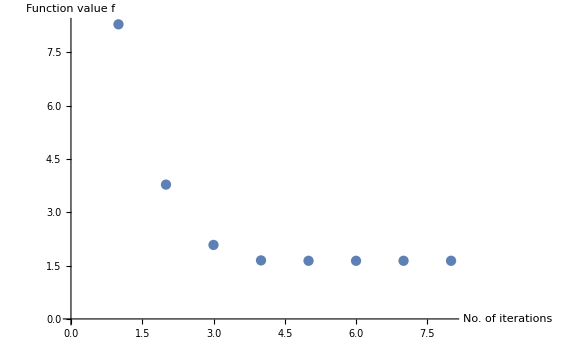

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
Result[[1,All]]
```

{1.63556}

#### Case 1.4.6: N=100, m=1/10, δ=1, dimS=8, l=8

```mathematica
CM0=partialCM[100,1/10,1,8,8,8];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0 | -0.00018661 | 0 | -0.000156594 | 0 | -0.000131877 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986 | 0 | 0.0321328 | 0 | 0.0284749 | 0 | 0.0252583
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0 | -0.00018661 | 0 | -0.000156594 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986 | 0 | 0.0321328 | 0 | 0.0284749
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0 | -0.00018661 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986 | 0 | 0.0321328
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408
-0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.00018661 | 0 | -0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0321328 | 0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000156594 | 0 | -0.00018661 | 0 | -0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0284749 | 0 | 0.0321328 | 0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000131877 | 0 | -0.000156594 | 0 | -0.00018661 | 0 | -0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.0321328 | 0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
GOExtractStdFormG[CM0][[2]]//MatrixForm
```

Dot::dotsh: Tensors … and {{0.,-0.258201,0.,-0.0734552,0.,-0.0441672,0.,-0.0372915,0.,-0.0407577,0.,-0.0562286,0.,-0.102449,0.,-0.36635,0.,-0.36635,0.,-0.102449,0.,-0.0562286,0.,-0.0407577,0.,-0.0372915,0.,-0.0441672,0.,-0.0734552,0.,-0.258201},«31»} have incompatible shapes.

Ok, now it doesn’t work. Great (?)

```mathematica
GOExtractStdFormG[CM0][[1]]
```

Dot::dotsh: Tensors … and {{0.,-0.258201,0.,-0.0734552,0.,-0.0441672,0.,-0.0372915,0.,-0.0407577,0.,-0.0562286,0.,-0.102449,0.,-0.36635,0.,-0.36635,0.,-0.102449,0.,-0.0562286,0.,-0.0407577,0.,-0.0372915,0.,-0.0441672,0.,-0.0734552,0.,-0.258201},«31»} have incompatible shapes.

But, aren’t the r[i]s supposed to be real?

```mathematica
GOTransformGtoJ[CM0,"qpqp","qpqp"]//Eigenvalues//Chop
```

{0.+1.37334 ⅈ,0.-1.37334 ⅈ,0.+1.24744 ⅈ,0.-1.24744 ⅈ,0.+1.16782 ⅈ,0.-1.16782 ⅈ,0.+1.13228 ⅈ,0.-1.13228 ⅈ,0.+1.00261 ⅈ,0.-1.00261 ⅈ,0.+1.00155 ⅈ,0.-1.00155 ⅈ,0.+1.00045 ⅈ,0.-1.00045 ⅈ,0.+1.00017 ⅈ,0.-1.00017 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

The problem is that there are many identical symplectic eigenvalues. We need to make a smart diagonalization. Here, we follow the discussion in https://math.stackexchange.com/questions/1171842/finding-the-symplectic-matrix-in-williamsons-theorem based on SchurDecomposition.

```mathematica
sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;
```

```mathematica
MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]]//Chop;MTra//MatrixForm//Chop
Det[MTra]
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm
```

(-0.0422576 | 0.257113 | -0.0374063 | 0.0731456 | -0.0357513 | 0.043981 | -0.0359428 | 0.0371343 | -0.0376655 | 0.0405859 | -0.0410315 | 0.0559916 | -0.0466346 | 0.102017 | -0.0563936 | 0.364806 | -0.0563936 | 0.364806 | -0.0466346 | 0.102017 | -0.0410315 | 0.0559916 | -0.0376655 | 0.0405859 | -0.0359428 | 0.0371343 | -0.0357513 | 0.043981 | -0.0374063 | 0.0731456 | -0.0422576 | 0.257113
0.458803 | 0.0236811 | 0.406131 | 0.00673699 | 0.388162 | 0.00405082 | 0.390242 | 0.00342022 | 0.408946 | 0.00373812 | 0.445491 | 0.00515704 | 0.506326 | 0.00939621 | 0.612283 | 0.0336001 | 0.612283 | 0.0336001 | 0.506326 | 0.00939621 | 0.445491 | 0.00515704 | 0.408946 | 0.00373812 | 0.390242 | 0.00342022 | 0.388162 | 0.00405082 | 0.406131 | 0.00673699 | 0.458803 | 0.0236811
0.0852015 | 0.447336 | 0.0654951 | 0.113589 | 0.0541604 | 0.0567481 | 0.0469137 | 0.0368834 | 0.0423996 | 0.0300249 | 0.0402505 | 0.0327121 | 0.0408746 | 0.0546918 | 0.0464513 | 0.216425 | -0.0464513 | -0.216425 | -0.0408746 | -0.0546918 | -0.0402505 | -0.0327121 | -0.0423996 | -0.0300249 | -0.0469137 | -0.0368834 | -0.0541604 | -0.0567481 | -0.0654951 | -0.113589 | -0.0852015 | -0.447336
-0.641718 | 0.0593932 | -0.493294 | 0.0150813 | -0.407923 | 0.0075345 | -0.353343 | 0.00489704 | -0.319344 | 0.00398643 | -0.303157 | 0.00434321 | -0.307858 | 0.00726148 | -0.349861 | 0.0287349 | 0.349861 | -0.0287349 | 0.307858 | -0.00726148 | 0.303157 | -0.00434321 | 0.319344 | -0.00398643 | 0.353343 | -0.00489704 | 0.407923 | -0.0075345 | 0.493294 | -0.0150813 | 0.641718 | -0.0593932
0.429942 | -0.310885 | 0.27034 | -0.0713224 | 0.162555 | -0.0283492 | 0.0746276 | -0.00949323 | -0.00636916 | 0.0042497 | -0.0893952 | 0.0209324 | -0.185291 | 0.0558485 | -0.318174 | 0.240035 | -0.318174 | 0.240035 | -0.185291 | 0.0558485 | -0.0893952 | 0.0209324 | -0.00636916 | 0.0042497 | 0.0746276 | -0.00949323 | 0.162555 | -0.0283492 | 0.27034 | -0.0713224 | 0.429942 | -0.310885
-0.366805 | -0.364397 | -0.23064 | -0.083599 | -0.138683 | -0.0332289 | -0.0636684 | -0.0111273 | 0.00543383 | 0.0049812 | 0.0762674 | 0.0245354 | 0.15808 | 0.0654617 | 0.271449 | 0.281352 | 0.271449 | 0.281352 | 0.15808 | 0.0654617 | 0.0762674 | 0.0245354 | 0.00543383 | 0.0049812 | -0.0636684 | -0.0111273 | -0.138683 | -0.0332289 | -0.23064 | -0.083599 | -0.366805 | -0.364397
0.19998 | 0.239275 | 0.10682 | 0.0530058 | 0.0401454 | 0.0191925 | -0.0186197 | 0.00313837 | -0.0781918 | -0.0109016 | -0.146609 | -0.0323797 | -0.236908 | -0.0871212 | -0.383887 | -0.424495 | 0.383887 | 0.424495 | 0.236908 | 0.0871212 | 0.146609 | 0.0323797 | 0.0781918 | 0.0109016 | 0.0186197 | -0.00313837 | -0.0401454 | -0.0191925 | -0.10682 | -0.0530058 | -0.19998 | -0.239275
-0.252189 | 0.189739 | -0.134708 | 0.0420323 | -0.0506262 | 0.0152192 | 0.0234808 | 0.00248865 | 0.0986056 | -0.00864473 | 0.184885 | -0.0256763 | 0.298758 | -0.069085 | 0.484109 | -0.336614 | -0.484109 | 0.336614 | -0.298758 | 0.069085 | -0.184885 | 0.0256763 | -0.0986056 | 0.00864473 | -0.0234808 | -0.00248865 | 0.0506262 | -0.0152192 | 0.134708 | -0.0420323 | 0.252189 | -0.189739
-0.152874 | 0.177864 | 0.206247 | -0.0727551 | 0.33353 | -0.0783523 | 0.381792 | -0.0754975 | 0.386803 | -0.0773166 | 0.346983 | -0.0842395 | 0.220476 | -0.0830066 | -0.170628 | 0.194345 | -0.170628 | 0.194345 | 0.220476 | -0.0830066 | 0.346983 | -0.0842395 | 0.386803 | -0.0773166 | 0.381792 | -0.0754975 | 0.33353 | -0.0783523 | 0.206247 | -0.0727551 | -0.152874 | 0.177864
0.0816305 | 0.333096 | -0.11013 | -0.136252 | -0.178096 | -0.146735 | -0.203867 | -0.141388 | -0.206543 | -0.144795 | -0.185279 | -0.15776 | -0.117728 | -0.155451 | 0.0911106 | 0.36396 | 0.0911106 | 0.36396 | -0.117728 | -0.155451 | -0.185279 | -0.15776 | -0.206543 | -0.144795 | -0.203867 | -0.141388 | -0.178096 | -0.146735 | -0.11013 | -0.136252 | 0.0816305 | 0.333096
0.0852805 | 0.415753 | -0.146641 | -0.242322 | -0.199689 | -0.208671 | -0.197473 | -0.159692 | -0.171778 | -0.123362 | -0.131037 | -0.0970318 | -0.0702159 | -0.0643295 | 0.0480884 | 0.236959 | -0.0480884 | -0.236959 | 0.0702159 | 0.0643295 | 0.131037 | 0.0970318 | 0.171778 | 0.123362 | 0.197473 | 0.159692 | 0.199689 | 0.208671 | 0.146641 | 0.242322 | -0.0852805 | -0.415753
-0.179196 | 0.197859 | 0.30813 | -0.115322 | 0.419599 | -0.0993077 | 0.414943 | -0.0759982 | 0.36095 | -0.0587084 | 0.275342 | -0.0461779 | 0.147542 | -0.0306147 | -0.101046 | 0.11277 | 0.101046 | -0.11277 | -0.147542 | 0.0306147 | -0.275342 | 0.0461779 | -0.36095 | 0.0587084 | -0.414943 | 0.0759982 | -0.419599 | 0.0993077 | -0.30813 | 0.115322 | 0.179196 | -0.197859
-0.113479 | 0.0681335 | 0.356826 | -0.0800662 | 0.312654 | -0.0487586 | 0.128716 | -0.0169509 | -0.0904903 | 0.0132192 | -0.28332 | 0.0459864 | -0.344523 | 0.0797791 | 0.107536 | -0.0644931 | 0.107536 | -0.0644931 | -0.344523 | 0.0797791 | -0.28332 | 0.0459864 | -0.0904903 | 0.0132192 | 0.128716 | -0.0169509 | 0.312654 | -0.0487586 | 0.356826 | -0.0800662 | -0.113479 | 0.0681335
-0.0243001 | -0.318178 | 0.0764094 | 0.373903 | 0.0669506 | 0.227699 | 0.0275628 | 0.0791595 | -0.0193773 | -0.0617327 | -0.060669 | -0.214753 | -0.0737749 | -0.372562 | 0.0230273 | 0.301178 | 0.0230273 | 0.301178 | -0.0737749 | -0.372562 | -0.060669 | -0.214753 | -0.0193773 | -0.0617327 | 0.0275628 | 0.0791595 | 0.0669506 | 0.227699 | 0.0764094 | 0.373903 | -0.0243001 | -0.318178
0.0383773 | -0.138225 | -0.173082 | 0.218336 | -0.123017 | 0.122665 | -0.00287415 | 0.0294893 | 0.137242 | -0.0657528 | 0.264937 | -0.18631 | 0.304939 | -0.343789 | -0.091881 | 0.296854 | 0.091881 | -0.296854 | -0.304939 | 0.343789 | -0.264937 | 0.18631 | -0.137242 | 0.0657528 | 0.00287415 | -0.0294893 | 0.123017 | -0.122665 | 0.173082 | -0.218336 | -0.0383773 | 0.138225
-0.0423988 | -0.125114 | 0.191219 | 0.197627 | 0.135908 | 0.11103 | 0.00317533 | 0.0266923 | -0.151623 | -0.0595161 | -0.292699 | -0.168639 | -0.336894 | -0.31118 | 0.101509 | 0.268697 | -0.101509 | -0.268697 | 0.336894 | 0.31118 | 0.292699 | 0.168639 | 0.151623 | 0.0595161 | -0.00317533 | -0.0266923 | -0.135908 | -0.11103 | -0.191219 | -0.197627 | 0.0423988 | 0.125114
0.0345917 | -0.0713477 | -0.305344 | 0.226836 | 0.097766 | -0.0485987 | 0.306572 | -0.126021 | 0.271068 | -0.105204 | 0.042617 | -0.0109367 | -0.257094 | 0.184963 | 0.0290476 | -0.0605999 | 0.0290476 | -0.0605999 | -0.257094 | 0.184963 | 0.042617 | -0.0109367 | 0.271068 | -0.105204 | 0.306572 | -0.126021 | 0.097766 | -0.0485987 | -0.305344 | 0.226836 | 0.0345917 | -0.0713477
0.0163822 | 0.150654 | -0.144607 | -0.478975 | 0.0463006 | 0.102618 | 0.145188 | 0.2661 | 0.128374 | 0.222144 | 0.0201828 | 0.0230933 | -0.121756 | -0.390557 | 0.0137565 | 0.127959 | 0.0137565 | 0.127959 | -0.121756 | -0.390557 | 0.0201828 | 0.0230933 | 0.128374 | 0.222144 | 0.145188 | 0.2661 | 0.0463006 | 0.102618 | -0.144607 | -0.478975 | 0.0163822 | 0.150654
-0.0299294 | -0.118589 | 0.266773 | 0.380344 | -0.0904833 | -0.0891682 | -0.262937 | -0.206086 | -0.224753 | -0.159034 | -0.040039 | -0.00888423 | 0.176612 | 0.249965 | -0.0170146 | -0.073747 | 0.0170146 | 0.073747 | -0.176612 | -0.249965 | 0.040039 | 0.00888423 | 0.224753 | 0.159034 | 0.262937 | 0.206086 | 0.0904833 | 0.0891682 | -0.266773 | -0.380344 | 0.0299294 | 0.118589
0.0270988 | -0.130977 | -0.241542 | 0.420073 | 0.0819257 | -0.0984824 | 0.23807 | -0.227613 | 0.203497 | -0.175646 | 0.0362522 | -0.00981224 | -0.159908 | 0.276075 | 0.0154054 | -0.0814503 | -0.0154054 | 0.0814503 | 0.159908 | -0.276075 | -0.0362522 | 0.00981224 | -0.203497 | 0.175646 | -0.23807 | 0.227613 | -0.0819257 | 0.0984824 | 0.241542 | -0.420073 | -0.0270988 | 0.130977
-0.0089131 | 0.0338724 | 0.134156 | -0.189491 | -0.232685 | 0.220434 | -0.126811 | 0.112218 | 0.171778 | -0.131704 | 0.26716 | -0.253034 | -0.196983 | 0.260324 | 0.0153145 | -0.0541634 | 0.0153145 | -0.0541634 | -0.196983 | 0.260324 | 0.26716 | -0.253034 | 0.171778 | -0.131704 | -0.126811 | 0.112218 | -0.232685 | 0.220434 | 0.134156 | -0.189491 | -0.0089131 | 0.0338724
0.0061393 | 0.0491764 | -0.0924056 | -0.275105 | 0.160272 | 0.320028 | 0.0873464 | 0.16292 | -0.11832 | -0.19121 | -0.184018 | -0.367358 | 0.135681 | 0.377942 | -0.0105486 | -0.078635 | -0.0105486 | -0.078635 | 0.135681 | 0.377942 | -0.184018 | -0.367358 | -0.11832 | -0.19121 | 0.0873464 | 0.16292 | 0.160272 | 0.320028 | -0.0924056 | -0.275105 | 0.0061393 | 0.0491764
0.00524221 | 0.0314839 | -0.0968541 | -0.207121 | 0.207334 | 0.283696 | 0.0829256 | 0.110649 | -0.172137 | -0.177668 | -0.240324 | -0.311361 | 0.170753 | 0.325543 | -0.0114442 | -0.0627342 | 0.0114442 | 0.0627342 | -0.170753 | -0.325543 | 0.240324 | 0.311361 | 0.172137 | 0.177668 | -0.0829256 | -0.110649 | -0.207334 | -0.283696 | 0.0968541 | 0.207121 | -0.00524221 | -0.0314839
-0.00512602 | 0.0321975 | 0.0947074 | -0.211815 | -0.202739 | 0.290126 | -0.0810877 | 0.113157 | 0.168322 | -0.181695 | 0.234998 | -0.318418 | -0.166968 | 0.332921 | 0.0111905 | -0.0641562 | -0.0111905 | 0.0641562 | 0.166968 | -0.332921 | -0.234998 | 0.318418 | -0.168322 | 0.181695 | 0.0810877 | -0.113157 | 0.202739 | -0.290126 | -0.0947074 | 0.211815 | 0.00512602 | -0.0321975
-0.00353619 | 0.00992481 | 0.083899 | -0.0870093 | -0.297717 | 0.212536 | 0.226959 | -0.141684 | 0.192723 | -0.112167 | -0.253944 | 0.18136 | 0.0659535 | -0.0708238 | -0.00244846 | 0.0073699 | -0.00244844 | 0.00736986 | 0.0659528 | -0.0708234 | -0.253941 | 0.181358 | 0.19272 | -0.112166 | 0.226959 | -0.141684 | -0.297716 | 0.212535 | 0.0838985 | -0.0870091 | -0.00353617 | 0.00992478
0.00144554 | 0.0242789 | -0.0342966 | -0.212849 | 0.121702 | 0.519921 | -0.0927772 | -0.346598 | -0.0787819 | -0.274394 | 0.103808 | 0.443657 | -0.0269607 | -0.173255 | 0.00100089 | 0.0180288 | 0.00100089 | 0.0180287 | -0.0269606 | -0.173253 | 0.103807 | 0.443652 | -0.078781 | -0.274388 | -0.0927775 | -0.346599 | 0.121702 | 0.519919 | -0.0342965 | -0.212848 | 0.00144554 | 0.0242787
-0.00281261 | 0.014872 | 0.0679825 | -0.132655 | -0.246385 | 0.329739 | 0.193576 | -0.223688 | 0.165337 | -0.182696 | -0.22893 | 0.303487 | 0.0632266 | -0.123565 | -0.00256518 | 0.0137315 | 0.00256518 | -0.0137316 | -0.0632268 | 0.123566 | 0.22893 | -0.303489 | -0.165336 | 0.182696 | -0.193578 | 0.223692 | 0.246387 | -0.329742 | -0.067983 | 0.132656 | 0.00281263 | -0.0148721
-0.00214641 | -0.0194879 | 0.0518802 | 0.173828 | -0.188026 | -0.432081 | 0.147726 | 0.293115 | 0.126175 | 0.239401 | -0.174705 | -0.397683 | 0.0482508 | 0.161917 | -0.00195759 | -0.0179934 | 0.0019576 | 0.0179935 | -0.048251 | -0.161917 | 0.174706 | 0.397683 | -0.126175 | -0.2394 | -0.147728 | -0.293119 | 0.188028 | 0.432085 | -0.0518807 | -0.173829 | 0.00214643 | 0.019488
0.0000239067 | 0.00389724 | -0.000989673 | -0.0588741 | 0.00692536 | 0.27812 | -0.0175954 | -0.592559 | 0.0192195 | 0.63396 | -0.00879829 | -0.338112 | 0.00138623 | 0.0794641 | -0.0000340488 | -0.0055667 | 0.000033391 | 0.00553786 | -0.00136335 | -0.0790983 | 0.00866709 | 0.336661 | -0.0189487 | -0.631343 | 0.0173527 | 0.590158 | -0.00682981 | -0.276997 | 0.000975821 | 0.0586342 | -0.000023563 | -0.00388103
0.000432239 | -0.000215533 | -0.0178963 | 0.00325563 | 0.125242 | -0.0153788 | -0.318208 | 0.0327664 | 0.347544 | -0.0350588 | -0.159053 | 0.0187017 | 0.0250459 | -0.00439696 | -0.000614573 | 0.000308233 | 0.000611097 | -0.000302776 | -0.024925 | 0.00432776 | 0.158359 | -0.0184272 | -0.346112 | 0.0345642 | 0.316923 | -0.0323128 | -0.124735 | 0.0151668 | 0.0178228 | -0.0032104 | -0.000430413 | 0.000212481
0.000289842 | -0.00291977 | -0.0117157 | 0.0433661 | 0.0809726 | -0.203593 | -0.205966 | 0.436035 | 0.230012 | -0.475859 | -0.111583 | 0.264294 | 0.0194721 | -0.0666908 | -0.000560577 | 0.00526391 | -0.000562528 | 0.00527928 | 0.0195514 | -0.0669097 | -0.112086 | 0.265224 | 0.231111 | -0.477601 | -0.206971 | 0.43766 | 0.0813674 | -0.204355 | -0.011772 | 0.0435269 | 0.000291198 | -0.00293038
0.000328237 | 0.00257821 | -0.0132678 | -0.0382928 | 0.0917006 | 0.179775 | -0.233254 | -0.385025 | 0.260482 | 0.420196 | -0.12636 | -0.233383 | 0.0220497 | 0.0588931 | -0.00063474 | -0.00464871 | -0.000636439 | -0.00466636 | 0.0221188 | 0.0591447 | -0.126798 | -0.234453 | 0.261437 | 0.4222 | -0.234127 | -0.386896 | 0.0920432 | 0.180652 | -0.0133166 | -0.0384782 | 0.000329411 | 0.00259046)

-1.

{0.419627,0.344864,0.285765,0.254419,0.0361036,0.0278298,0.0149274,0.00925849,0.00128072,0.00120328,0.000284938,0.000108141,0.0000216461,0.0000206971,9.21827×10^-7,5.3551×10^-7}

(1.37334 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.37334 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.24744 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.24744 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.16782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.16782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.13228 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.13228 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00155 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00155 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

We continue with the use of the Schur decomposition, and not the implemented way in the package.

```mathematica
JT=GOPurifyStandardJBoson[rlist,(8+8),"qpqp"]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[4(8+8)],"qpqp","qpqp"]//Chop;
```

We do the minimization with 10 randomly generated initial matrices M0:

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{8,8},"GOSpBasis"]}}]//SparseArray,{10}];
```

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];ProblemSpecific={function,gradient};
```

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{8,8,8,8}];
metric=GOMetricSp[LieBasis,JR0];
SystemSpecific={JR0,M0List,LieBasis,metric};
```

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 737.136

Final value: {1.64053}

Number of iterations: {8}

Number of total corrections: 1

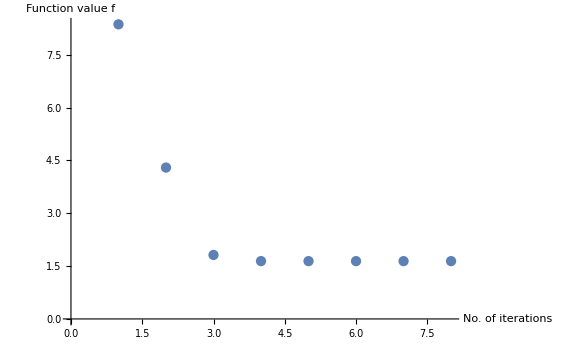

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
Result[[1,All]]
```

{1.64053}

#### Case 1.4.7: N=100, m=1/10, δ=1, dimS=8, l=10

```mathematica
CM0=partialCM[100,1/10,1,10,8,8];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0 | -0.00018661 | 0 | -0.000156594 | 0 | -0.000131877 | 0 | -0.000111427 | 0 | -0.0000944326 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986 | 0 | 0.0321328 | 0 | 0.0284749 | 0 | 0.0252583 | 0 | 0.0224262 | 0 | 0.0199298
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0 | -0.00018661 | 0 | -0.000156594 | 0 | -0.000131877 | 0 | -0.000111427 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986 | 0 | 0.0321328 | 0 | 0.0284749 | 0 | 0.0252583 | 0 | 0.0224262
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0 | -0.00018661 | 0 | -0.000156594 | 0 | -0.000131877 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986 | 0 | 0.0321328 | 0 | 0.0284749 | 0 | 0.0252583
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0 | -0.00018661 | 0 | -0.000156594 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986 | 0 | 0.0321328 | 0 | 0.0284749
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0 | -0.00018661 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986 | 0 | 0.0321328
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815
-0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.00018661 | 0 | -0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.000731856 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.0321328 | 0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.000156594 | 0 | -0.00018661 | 0 | -0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.000590478 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.0284749 | 0 | 0.0321328 | 0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.0680592 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.000131877 | 0 | -0.000156594 | 0 | -0.00018661 | 0 | -0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.0321328 | 0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000111427 | 0 | -0.000131877 | 0 | -0.000156594 | 0 | -0.00018661 | 0 | -0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0224262 | 0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.0321328 | 0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0000944326 | 0 | -0.000111427 | 0 | -0.000131877 | 0 | -0.000156594 | 0 | -0.00018661 | 0 | -0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0199298 | 0 | 0.0224262 | 0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.0321328 | 0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
GOExtractStdFormG[CM0][[2]]//Chop//MatrixForm
```

(0 | -0.271601 | 0 | -0.0766998 | 0 | -0.0456075 | 0 | -0.0379649 | 0 | -0.0409002 | 0 | -0.0557671 | 0 | -0.100865 | 0 | -0.360426 | 0 | -0.360426 | 0 | -0.100865 | 0 | -0.0557671 | 0 | -0.0409002 | 0 | -0.0379649 | 0 | -0.0456075 | 0 | -0.0766998 | 0 | -0.271601
0.473868 | 0 | 0.414714 | 0 | 0.39224 | 0 | 0.390569 | 0 | 0.405808 | 0 | 0.438907 | 0 | 0.496142 | 0 | 0.598332 | 0 | 0.598332 | 0 | 0.496142 | 0 | 0.438907 | 0 | 0.405808 | 0 | 0.390569 | 0 | 0.39224 | 0 | 0.414714 | 0 | 0.473868 | 0
-0.619323 | -1.65039×10^-6 | -0.484773 | 1.92663×10^-6 | -0.409568 | -0.0000112112 | -0.363994 | 0.0000235747 | -0.338945 | -0.0000258217 | -0.332499 | 0.0000138468 | -0.348822 | -3.61706×10^-6 | -0.406686 | -6.57683×10^-7 | 0.406686 | 6.36352×10^-7 | 0.348822 | 3.91132×10^-6 | 0.332499 | -0.0000151172 | 0.338945 | 0.0000283341 | 0.363994 | -0.0000261321 | 0.409568 | 0.0000125559 | 0.484773 | -2.25479×10^-6 | 0.619323 | 1.67635×10^-6
2.05287×10^-6 | -0.421915 | 7.72111×10^-7 | -0.10835 | 7.14049×10^-6 | -0.0553024 | -0.0000137073 | -0.037356 | 0.0000176581 | -0.0322417 | -6.68379×10^-6 | -0.0374658 | 2.42221×10^-6 | -0.065094 | 1.3017×10^-6 | -0.255317 | -1.29844×10^-6 | 0.255317 | -2.54698×10^-6 | 0.065094 | 7.46965×10^-6 | 0.0374658 | -0.0000194671 | 0.0322417 | 0.0000155548 | 0.037356 | -7.98304×10^-6 | 0.0553024 | -6.28392×10^-7 | 0.10835 | -2.05715×10^-6 | 0.421915
0 | -0.471802 | 0 | -0.107725 | 0 | -0.0423306 | 0 | -0.0134939 | 0 | 0.00772392 | 0 | 0.0337616 | 0 | 0.0887442 | 0 | 0.381291 | 0 | 0.381291 | 0 | 0.0887442 | 0 | 0.0337616 | 0 | 0.00772392 | 0 | -0.0134939 | 0 | -0.0423306 | 0 | -0.107725 | 0 | -0.471802
0.553252 | 0 | 0.34507 | 0 | 0.204142 | 0 | 0.0888473 | 0 | -0.0177151 | 0 | -0.127379 | 0 | -0.254695 | 0 | -0.432533 | 0 | -0.432533 | 0 | -0.254695 | 0 | -0.127379 | 0 | -0.0177151 | 0 | 0.0888473 | 0 | 0.204142 | 0 | 0.34507 | 0 | 0.553252 | 0
0 | 0.344738 | 0 | 0.0770648 | 0 | 0.0285773 | 0 | 0.0059714 | 0 | -0.0130114 | 0 | -0.0407045 | 0 | -0.108591 | 0 | -0.513708 | 0 | 0.513708 | 0 | 0.108591 | 0 | 0.0407045 | 0 | 0.0130114 | 0 | -0.0059714 | 0 | -0.0285773 | 0 | -0.0770648 | 0 | -0.344738
-0.374339 | 0 | -0.209783 | 0 | -0.0935847 | 0 | 0.00703735 | 0 | 0.106901 | 0 | 0.21883 | 0 | 0.362509 | 0 | 0.588834 | 0 | -0.588834 | 0 | -0.362509 | 0 | -0.21883 | 0 | -0.106901 | 0 | -0.00703735 | 0 | 0.0935847 | 0 | 0.209783 | 0 | 0.374339 | 0
-0.000104504 | -0.000665506 | 0.0023367 | 0.00580121 | -0.0075351 | -0.0123066 | 0.00304209 | 0.00456436 | 0.0059167 | 0.00764994 | -0.00174653 | -0.00435124 | -0.000975933 | -0.00102783 | 0.0000936181 | 0.000496473 | -0.000130992 | 0.000362679 | -0.00676216 | -0.0321971 | 0.0907795 | 0.217769 | -0.292176 | -0.55151 | 0.367356 | 0.664565 | -0.193989 | -0.39733 | 0.0370339 | 0.107738 | -0.00119851 | -0.00935769
0.0000768217 | -0.000656274 | -0.00231814 | 0.00582946 | 0.00788418 | -0.0131873 | -0.00416988 | 0.00626001 | -0.00588684 | 0.00771336 | 0.00319623 | -0.00659124 | 0.000233373 | 0.000513097 | -0.0000619717 | 0.000224745 | 0.0000566371 | 0.000942715 | 0.0086227 | -0.0366769 | -0.0966118 | 0.227868 | 0.296285 | -0.558067 | -0.364327 | 0.660419 | 0.190051 | -0.390397 | -0.0359881 | 0.105047 | 0.00118076 | -0.00905624
0.000120494 | 0.000640148 | -0.00178939 | -0.00393091 | 0.00422401 | 0.00706017 | -0.00197927 | -0.00381244 | -0.000766728 | -0.00024845 | -0.000537993 | -0.000478855 | 0.000362672 | 0.000767035 | -3.62518×10^-6 | -0.0000935127 | -0.00323924 | -0.0229987 | 0.0822844 | 0.214793 | -0.315679 | -0.563126 | 0.283298 | 0.439598 | 0.164535 | 0.224262 | -0.276023 | -0.47005 | 0.0804215 | 0.202212 | -0.00341534 | -0.0233895
-0.000120072 | 0.000666146 | 0.00184783 | -0.00399346 | -0.00413041 | 0.0066744 | 0.00111005 | -0.00218833 | 0.00198076 | -0.0023354 | 0.0000913982 | 0.000551944 | -0.000358864 | 0.00063703 | 0.0000115329 | -0.000104066 | 0.00322815 | -0.0229428 | -0.0820287 | 0.213996 | 0.313973 | -0.559293 | -0.278647 | 0.430712 | -0.170434 | 0.234982 | 0.279303 | -0.47669 | -0.0810914 | 0.204099 | 0.00343363 | -0.0235662
0 | -0.370768 | 0 | 0.145707 | 0 | 0.162009 | 0 | 0.160004 | 0 | 0.16707 | 0 | 0.183896 | 0 | 0.180821 | 0 | -0.416149 | 0 | -0.416149 | 0 | 0.180821 | 0 | 0.183896 | 0 | 0.16707 | 0 | 0.160004 | 0 | 0.162009 | 0 | 0.145707 | 0 | -0.370768
0.17104 | 0 | -0.225736 | 0 | -0.372075 | 0 | -0.431548 | 0 | -0.441777 | 0 | -0.39923 | 0 | -0.254666 | 0 | 0.194858 | 0 | 0.194858 | 0 | -0.254666 | 0 | -0.39923 | 0 | -0.441777 | 0 | -0.431548 | 0 | -0.372075 | 0 | -0.225736 | 0 | 0.17104 | 0
0 | 0.448154 | 0 | -0.249498 | 0 | -0.220483 | 0 | -0.174491 | 0 | -0.142275 | 0 | -0.121949 | 0 | -0.0941018 | 0 | 0.292143 | 0 | -0.292143 | 0 | 0.0941018 | 0 | 0.121949 | 0 | 0.142275 | 0 | 0.174491 | 0 | 0.220483 | 0 | 0.249498 | 0 | -0.448154
-0.194891 | 0 | 0.324142 | 0 | 0.451926 | 0 | 0.457709 | 0 | 0.410094 | 0 | 0.325028 | 0 | 0.183716 | 0 | -0.126675 | 0 | 0.126675 | 0 | -0.183716 | 0 | -0.325028 | 0 | -0.410094 | 0 | -0.457709 | 0 | -0.451926 | 0 | -0.324142 | 0 | 0.194891 | 0
0.11943 | 0 | -0.372084 | 0 | -0.3265 | 0 | -0.136373 | 0 | 0.088577 | 0 | 0.284187 | 0 | 0.344259 | 0 | -0.1055 | 0 | -0.1055 | 0 | 0.344259 | 0 | 0.284187 | 0 | 0.088577 | 0 | -0.136373 | 0 | -0.3265 | 0 | -0.372084 | 0 | 0.11943 | 0
0 | 0.333625 | 0 | -0.389429 | 0 | -0.236138 | 0 | -0.0813477 | 0 | 0.0636921 | 0 | 0.218004 | 0 | 0.371919 | 0 | -0.297916 | 0 | -0.297916 | 0 | 0.371919 | 0 | 0.218004 | 0 | 0.0636921 | 0 | -0.0813477 | 0 | -0.236138 | 0 | -0.389429 | 0 | 0.333625
0.0690848 | 0 | -0.281316 | 0 | -0.211875 | 0 | -0.0286061 | 0 | 0.185831 | 0 | 0.378329 | 0 | 0.435147 | 0 | -0.134628 | 0 | 0.134628 | 0 | -0.435147 | 0 | -0.378329 | 0 | -0.185831 | 0 | 0.0286061 | 0 | 0.211875 | 0 | 0.281316 | 0 | -0.0690848 | 0
0 | 0.215157 | 0 | -0.314476 | 0 | -0.180714 | 0 | -0.0478279 | 0 | 0.0860353 | 0 | 0.248857 | 0 | 0.447584 | 0 | -0.387059 | 0 | 0.387059 | 0 | -0.447584 | 0 | -0.248857 | 0 | -0.0860353 | 0 | 0.0478279 | 0 | 0.180714 | 0 | 0.314476 | 0 | -0.215157
0.00108765 | 0.00543871 | -0.0127821 | -0.0227993 | 0.0125173 | 0.0176035 | 0.00929163 | 0.00946561 | -0.00526806 | -0.01119 | -0.00521207 | -0.0171513 | 0.0291704 | 0.0418734 | -0.00522368 | -0.0184182 | -0.0296036 | -0.132278 | 0.270194 | 0.413366 | -0.0483881 | -0.0206204 | -0.30093 | -0.243359 | -0.344024 | -0.29825 | -0.112655 | -0.11934 | 0.343619 | 0.53986 | -0.0387532 | -0.169108
-0.00108589 | 0.00543135 | 0.0127611 | -0.0227689 | -0.0124994 | 0.0175962 | -0.00924357 | 0.00939678 | 0.00523391 | -0.0111422 | 0.00518006 | -0.0171174 | -0.0291429 | 0.0418395 | 0.00522104 | -0.0184127 | 0.0295958 | -0.132279 | -0.270113 | 0.413336 | 0.0483331 | -0.0205401 | 0.30083 | -0.243316 | 0.344013 | -0.298376 | 0.112674 | -0.119426 | -0.343589 | 0.540016 | 0.0387488 | -0.169148
-0.0027977 | -0.0126043 | 0.0267538 | 0.0441624 | -0.0154122 | -0.0199961 | -0.0237855 | -0.0221834 | -0.00888498 | 0.000177116 | -0.00330741 | 0.000467087 | 0.0022032 | 0.00539176 | 0.000746944 | 0.000963314 | 0.0177939 | 0.0933141 | -0.237485 | -0.457449 | 0.32411 | 0.439819 | 0.21854 | 0.238267 | -0.135885 | -0.174906 | -0.290641 | -0.404702 | 0.156327 | 0.326834 | -0.00986136 | -0.0558295
0.00268277 | -0.0119388 | -0.0248283 | 0.0400149 | 0.0113684 | -0.0140114 | 0.0231664 | -0.0218076 | 0.0110767 | -0.00178143 | 0.00713929 | -0.00480327 | -0.00500878 | 0.010773 | -0.000536436 | -0.000139731 | -0.0178048 | 0.0933908 | 0.237749 | -0.457886 | -0.324313 | 0.439878 | -0.219336 | 0.239366 | 0.136399 | -0.176102 | 0.290125 | -0.403693 | -0.155918 | 0.326096 | 0.0098212 | -0.0556508
0.0386749 | 0.169485 | -0.342845 | -0.540847 | 0.112042 | 0.118967 | 0.343455 | 0.299136 | 0.300514 | 0.244033 | 0.0486362 | 0.0210702 | -0.269605 | -0.414473 | 0.0295034 | 0.132497 | 0.00483303 | 0.0167126 | -0.0254122 | -0.0360086 | 0.00371149 | 0.0156756 | 0.00124256 | 0.00774768 | -0.0126523 | -0.0122019 | -0.0129777 | -0.0179361 | 0.0161668 | 0.0280218 | -0.00149134 | -0.00719666
-0.0387626 | 0.168364 | 0.343111 | -0.536206 | -0.110373 | 0.115612 | -0.343781 | 0.296458 | -0.303436 | 0.244778 | -0.0513321 | 0.0242607 | 0.272545 | -0.41611 | -0.0297619 | 0.132626 | -0.00485461 | 0.0166278 | 0.0254493 | -0.0357219 | -0.00364399 | 0.0155372 | -0.00113138 | 0.00767361 | 0.0128961 | -0.0123339 | 0.0130697 | -0.0178869 | -0.0164097 | 0.0281628 | 0.00151768 | -0.00725088
0.00967767 | 0.054798 | -0.153373 | -0.320041 | 0.282348 | 0.389701 | 0.143714 | 0.188504 | -0.218495 | -0.239051 | -0.328877 | -0.446999 | 0.238879 | 0.461151 | -0.0177819 | -0.0935879 | 0.000372236 | 0.00479652 | -0.0165185 | -0.0323242 | 0.0207855 | 0.0225037 | 0.0236628 | 0.0158615 | 0.0189754 | 0.0162542 | -0.00386983 | -0.0079347 | -0.0178651 | -0.0247407 | 0.00230121 | 0.00961418
-0.0100036 | 0.0562699 | 0.156412 | -0.325106 | -0.284169 | 0.392321 | -0.145424 | 0.189051 | 0.21574 | -0.236246 | 0.328405 | -0.44673 | -0.236814 | 0.457747 | 0.017571 | -0.0925633 | -0.000197759 | 0.00382064 | 0.0139175 | -0.0272096 | -0.0169714 | 0.0172795 | -0.0215674 | 0.0140551 | -0.0195287 | 0.0165672 | -0.0000320878 | -0.00214167 | 0.0196784 | -0.0286804 | -0.00240688 | 0.0102328
-0.00374906 | 0.0256915 | 0.0887093 | -0.224744 | -0.313612 | 0.545893 | 0.232722 | -0.350878 | 0.219563 | -0.318498 | -0.281934 | 0.493992 | 0.0740776 | -0.193364 | -0.00284571 | 0.0205193 | -0.000119874 | 0.000825164 | 0.00266964 | -0.00619486 | -0.00734998 | 0.012615 | 0.00553356 | -0.0115111 | -0.00445341 | 0.00924605 | 0.0044301 | -0.00796249 | -0.00160541 | 0.00368282 | 0.0000959539 | -0.000547202
-0.00377167 | -0.0258693 | 0.0893098 | 0.226596 | -0.316608 | -0.552526 | 0.238876 | 0.362737 | 0.212952 | 0.306337 | -0.278084 | -0.486665 | 0.0731268 | 0.191045 | -0.00280248 | -0.0202558 | -0.0001397 | -0.000923066 | 0.00289856 | 0.0065314 | -0.00729098 | -0.0121644 | 0.00423585 | 0.00939699 | -0.00343674 | -0.00743414 | 0.00447934 | 0.00774673 | -0.00174127 | -0.00391614 | 0.000105109 | 0.00059745
0.000503595 | 0.00439567 | -0.0193385 | -0.0618717 | 0.1277 | 0.280812 | -0.314587 | -0.586446 | 0.342339 | 0.626621 | -0.162061 | -0.341182 | 0.0276502 | 0.0844063 | -0.000793642 | -0.00654387 | -0.0000984656 | -0.00057028 | 0.00142222 | 0.00253185 | -0.00115777 | -0.000944648 | -0.00290622 | -0.00359811 | 0.0000342265 | -0.0000148749 | 0.00341069 | 0.00516802 | -0.00136371 | -0.00311583 | 0.0000808516 | 0.000434999
-0.000581133 | 0.00479302 | 0.0208075 | -0.0657664 | -0.133446 | 0.291056 | 0.319605 | -0.594093 | -0.338459 | 0.620905 | 0.15563 | -0.330297 | -0.0256342 | 0.0794826 | 0.000685599 | -0.0059353 | 0.000155003 | -0.000810403 | -0.00211108 | 0.00402709 | 0.00261143 | -0.00319118 | 0.00283449 | -0.00332635 | -0.00100642 | 0.00145552 | -0.00305509 | 0.00436112 | 0.00140694 | -0.00307238 | -0.0000665531 | 0.000474046)

Ok, now it works (?)

```mathematica
GOExtractStdFormG[CM0][[1]]
```

{0.411806,0.352221,0.283894,0.262604,0.0805981,0.0557479,0.0371565,0.0287879,0.0150417,0.0108717,0.00435538,0.00384025,0.+0.00395773 ⅈ,0.+0.00410445 ⅈ,0.+0.0572146 ⅈ,0.+0.0792538 ⅈ}

But, aren’t the r[i]s supposed to be real?

```mathematica
GOTransformGtoJ[CM0,"qpqp","qpqp"]//Eigenvalues//Chop
```

{0.+1.35878 ⅈ,0.-1.35878 ⅈ,0.+1.25855 ⅈ,0.-1.25855 ⅈ,0.+1.16557 ⅈ,0.-1.16557 ⅈ,0.+1.14112 ⅈ,0.-1.14112 ⅈ,0.+1.00276 ⅈ,0.-1.00276 ⅈ,0.+1.00166 ⅈ,0.-1.00166 ⅈ,0.+1.00045 ⅈ,0.-1.00045 ⅈ,0.+1.00024 ⅈ,0.-1.00024 ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.-1. ⅈ}

The problem is that there are many identical symplectic eigenvalues. We need to make a smart diagonalization. Here, we follow the discussion in https://math.stackexchange.com/questions/1171842/finding-the-symplectic-matrix-in-williamsons-theorem based on SchurDecomposition.

```mathematica
sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;
```

```mathematica
MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]]//Chop;MTra//MatrixForm//Chop
Det[MTra]
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm
```

(-0.0422576 | 0.257113 | -0.0374063 | 0.0731456 | -0.0357513 | 0.043981 | -0.0359428 | 0.0371343 | -0.0376655 | 0.0405859 | -0.0410315 | 0.0559916 | -0.0466346 | 0.102017 | -0.0563936 | 0.364806 | -0.0563936 | 0.364806 | -0.0466346 | 0.102017 | -0.0410315 | 0.0559916 | -0.0376655 | 0.0405859 | -0.0359428 | 0.0371343 | -0.0357513 | 0.043981 | -0.0374063 | 0.0731456 | -0.0422576 | 0.257113
0.458803 | 0.0236811 | 0.406131 | 0.00673699 | 0.388162 | 0.00405082 | 0.390242 | 0.00342022 | 0.408946 | 0.00373812 | 0.445491 | 0.00515704 | 0.506326 | 0.00939621 | 0.612283 | 0.0336001 | 0.612283 | 0.0336001 | 0.506326 | 0.00939621 | 0.445491 | 0.00515704 | 0.408946 | 0.00373812 | 0.390242 | 0.00342022 | 0.388162 | 0.00405082 | 0.406131 | 0.00673699 | 0.458803 | 0.0236811
0.0852015 | 0.447336 | 0.0654951 | 0.113589 | 0.0541604 | 0.0567481 | 0.0469137 | 0.0368834 | 0.0423996 | 0.0300249 | 0.0402505 | 0.0327121 | 0.0408746 | 0.0546918 | 0.0464513 | 0.216425 | -0.0464513 | -0.216425 | -0.0408746 | -0.0546918 | -0.0402505 | -0.0327121 | -0.0423996 | -0.0300249 | -0.0469137 | -0.0368834 | -0.0541604 | -0.0567481 | -0.0654951 | -0.113589 | -0.0852015 | -0.447336
-0.641718 | 0.0593932 | -0.493294 | 0.0150813 | -0.407923 | 0.0075345 | -0.353343 | 0.00489704 | -0.319344 | 0.00398643 | -0.303157 | 0.00434321 | -0.307858 | 0.00726148 | -0.349861 | 0.0287349 | 0.349861 | -0.0287349 | 0.307858 | -0.00726148 | 0.303157 | -0.00434321 | 0.319344 | -0.00398643 | 0.353343 | -0.00489704 | 0.407923 | -0.0075345 | 0.493294 | -0.0150813 | 0.641718 | -0.0593932
0.429942 | -0.310885 | 0.27034 | -0.0713224 | 0.162555 | -0.0283492 | 0.0746276 | -0.00949323 | -0.00636916 | 0.0042497 | -0.0893952 | 0.0209324 | -0.185291 | 0.0558485 | -0.318174 | 0.240035 | -0.318174 | 0.240035 | -0.185291 | 0.0558485 | -0.0893952 | 0.0209324 | -0.00636916 | 0.0042497 | 0.0746276 | -0.00949323 | 0.162555 | -0.0283492 | 0.27034 | -0.0713224 | 0.429942 | -0.310885
-0.366805 | -0.364397 | -0.23064 | -0.083599 | -0.138683 | -0.0332289 | -0.0636684 | -0.0111273 | 0.00543383 | 0.0049812 | 0.0762674 | 0.0245354 | 0.15808 | 0.0654617 | 0.271449 | 0.281352 | 0.271449 | 0.281352 | 0.15808 | 0.0654617 | 0.0762674 | 0.0245354 | 0.00543383 | 0.0049812 | -0.0636684 | -0.0111273 | -0.138683 | -0.0332289 | -0.23064 | -0.083599 | -0.366805 | -0.364397
0.19998 | 0.239275 | 0.10682 | 0.0530058 | 0.0401454 | 0.0191925 | -0.0186197 | 0.00313837 | -0.0781918 | -0.0109016 | -0.146609 | -0.0323797 | -0.236908 | -0.0871212 | -0.383887 | -0.424495 | 0.383887 | 0.424495 | 0.236908 | 0.0871212 | 0.146609 | 0.0323797 | 0.0781918 | 0.0109016 | 0.0186197 | -0.00313837 | -0.0401454 | -0.0191925 | -0.10682 | -0.0530058 | -0.19998 | -0.239275
-0.252189 | 0.189739 | -0.134708 | 0.0420323 | -0.0506262 | 0.0152192 | 0.0234808 | 0.00248865 | 0.0986056 | -0.00864473 | 0.184885 | -0.0256763 | 0.298758 | -0.069085 | 0.484109 | -0.336614 | -0.484109 | 0.336614 | -0.298758 | 0.069085 | -0.184885 | 0.0256763 | -0.0986056 | 0.00864473 | -0.0234808 | -0.00248865 | 0.0506262 | -0.0152192 | 0.134708 | -0.0420323 | 0.252189 | -0.189739
-0.152874 | 0.177864 | 0.206247 | -0.0727551 | 0.33353 | -0.0783523 | 0.381792 | -0.0754975 | 0.386803 | -0.0773166 | 0.346983 | -0.0842395 | 0.220476 | -0.0830066 | -0.170628 | 0.194345 | -0.170628 | 0.194345 | 0.220476 | -0.0830066 | 0.346983 | -0.0842395 | 0.386803 | -0.0773166 | 0.381792 | -0.0754975 | 0.33353 | -0.0783523 | 0.206247 | -0.0727551 | -0.152874 | 0.177864
0.0816305 | 0.333096 | -0.11013 | -0.136252 | -0.178096 | -0.146735 | -0.203867 | -0.141388 | -0.206543 | -0.144795 | -0.185279 | -0.15776 | -0.117728 | -0.155451 | 0.0911106 | 0.36396 | 0.0911106 | 0.36396 | -0.117728 | -0.155451 | -0.185279 | -0.15776 | -0.206543 | -0.144795 | -0.203867 | -0.141388 | -0.178096 | -0.146735 | -0.11013 | -0.136252 | 0.0816305 | 0.333096
0.0852805 | 0.415753 | -0.146641 | -0.242322 | -0.199689 | -0.208671 | -0.197473 | -0.159692 | -0.171778 | -0.123362 | -0.131037 | -0.0970318 | -0.0702159 | -0.0643295 | 0.0480884 | 0.236959 | -0.0480884 | -0.236959 | 0.0702159 | 0.0643295 | 0.131037 | 0.0970318 | 0.171778 | 0.123362 | 0.197473 | 0.159692 | 0.199689 | 0.208671 | 0.146641 | 0.242322 | -0.0852805 | -0.415753
-0.179196 | 0.197859 | 0.30813 | -0.115322 | 0.419599 | -0.0993077 | 0.414943 | -0.0759982 | 0.36095 | -0.0587084 | 0.275342 | -0.0461779 | 0.147542 | -0.0306147 | -0.101046 | 0.11277 | 0.101046 | -0.11277 | -0.147542 | 0.0306147 | -0.275342 | 0.0461779 | -0.36095 | 0.0587084 | -0.414943 | 0.0759982 | -0.419599 | 0.0993077 | -0.30813 | 0.115322 | 0.179196 | -0.197859
-0.113479 | 0.0681335 | 0.356826 | -0.0800662 | 0.312654 | -0.0487586 | 0.128716 | -0.0169509 | -0.0904903 | 0.0132192 | -0.28332 | 0.0459864 | -0.344523 | 0.0797791 | 0.107536 | -0.0644931 | 0.107536 | -0.0644931 | -0.344523 | 0.0797791 | -0.28332 | 0.0459864 | -0.0904903 | 0.0132192 | 0.128716 | -0.0169509 | 0.312654 | -0.0487586 | 0.356826 | -0.0800662 | -0.113479 | 0.0681335
-0.0243001 | -0.318178 | 0.0764094 | 0.373903 | 0.0669506 | 0.227699 | 0.0275628 | 0.0791595 | -0.0193773 | -0.0617327 | -0.060669 | -0.214753 | -0.0737749 | -0.372562 | 0.0230273 | 0.301178 | 0.0230273 | 0.301178 | -0.0737749 | -0.372562 | -0.060669 | -0.214753 | -0.0193773 | -0.0617327 | 0.0275628 | 0.0791595 | 0.0669506 | 0.227699 | 0.0764094 | 0.373903 | -0.0243001 | -0.318178
0.0383773 | -0.138225 | -0.173082 | 0.218336 | -0.123017 | 0.122665 | -0.00287415 | 0.0294893 | 0.137242 | -0.0657528 | 0.264937 | -0.18631 | 0.304939 | -0.343789 | -0.091881 | 0.296854 | 0.091881 | -0.296854 | -0.304939 | 0.343789 | -0.264937 | 0.18631 | -0.137242 | 0.0657528 | 0.00287415 | -0.0294893 | 0.123017 | -0.122665 | 0.173082 | -0.218336 | -0.0383773 | 0.138225
-0.0423988 | -0.125114 | 0.191219 | 0.197627 | 0.135908 | 0.11103 | 0.00317533 | 0.0266923 | -0.151623 | -0.0595161 | -0.292699 | -0.168639 | -0.336894 | -0.31118 | 0.101509 | 0.268697 | -0.101509 | -0.268697 | 0.336894 | 0.31118 | 0.292699 | 0.168639 | 0.151623 | 0.0595161 | -0.00317533 | -0.0266923 | -0.135908 | -0.11103 | -0.191219 | -0.197627 | 0.0423988 | 0.125114
0.0345917 | -0.0713477 | -0.305344 | 0.226836 | 0.097766 | -0.0485987 | 0.306572 | -0.126021 | 0.271068 | -0.105204 | 0.042617 | -0.0109367 | -0.257094 | 0.184963 | 0.0290476 | -0.0605999 | 0.0290476 | -0.0605999 | -0.257094 | 0.184963 | 0.042617 | -0.0109367 | 0.271068 | -0.105204 | 0.306572 | -0.126021 | 0.097766 | -0.0485987 | -0.305344 | 0.226836 | 0.0345917 | -0.0713477
0.0163822 | 0.150654 | -0.144607 | -0.478975 | 0.0463006 | 0.102618 | 0.145188 | 0.2661 | 0.128374 | 0.222144 | 0.0201828 | 0.0230933 | -0.121756 | -0.390557 | 0.0137565 | 0.127959 | 0.0137565 | 0.127959 | -0.121756 | -0.390557 | 0.0201828 | 0.0230933 | 0.128374 | 0.222144 | 0.145188 | 0.2661 | 0.0463006 | 0.102618 | -0.144607 | -0.478975 | 0.0163822 | 0.150654
-0.0299294 | -0.118589 | 0.266773 | 0.380344 | -0.0904833 | -0.0891682 | -0.262937 | -0.206086 | -0.224753 | -0.159034 | -0.040039 | -0.00888423 | 0.176612 | 0.249965 | -0.0170146 | -0.073747 | 0.0170146 | 0.073747 | -0.176612 | -0.249965 | 0.040039 | 0.00888423 | 0.224753 | 0.159034 | 0.262937 | 0.206086 | 0.0904833 | 0.0891682 | -0.266773 | -0.380344 | 0.0299294 | 0.118589
0.0270988 | -0.130977 | -0.241542 | 0.420073 | 0.0819257 | -0.0984824 | 0.23807 | -0.227613 | 0.203497 | -0.175646 | 0.0362522 | -0.00981224 | -0.159908 | 0.276075 | 0.0154054 | -0.0814503 | -0.0154054 | 0.0814503 | 0.159908 | -0.276075 | -0.0362522 | 0.00981224 | -0.203497 | 0.175646 | -0.23807 | 0.227613 | -0.0819257 | 0.0984824 | 0.241542 | -0.420073 | -0.0270988 | 0.130977
-0.0089131 | 0.0338724 | 0.134156 | -0.189491 | -0.232685 | 0.220434 | -0.126811 | 0.112218 | 0.171778 | -0.131704 | 0.26716 | -0.253034 | -0.196983 | 0.260324 | 0.0153145 | -0.0541634 | 0.0153145 | -0.0541634 | -0.196983 | 0.260324 | 0.26716 | -0.253034 | 0.171778 | -0.131704 | -0.126811 | 0.112218 | -0.232685 | 0.220434 | 0.134156 | -0.189491 | -0.0089131 | 0.0338724
0.0061393 | 0.0491764 | -0.0924056 | -0.275105 | 0.160272 | 0.320028 | 0.0873464 | 0.16292 | -0.11832 | -0.19121 | -0.184018 | -0.367358 | 0.135681 | 0.377942 | -0.0105486 | -0.078635 | -0.0105486 | -0.078635 | 0.135681 | 0.377942 | -0.184018 | -0.367358 | -0.11832 | -0.19121 | 0.0873464 | 0.16292 | 0.160272 | 0.320028 | -0.0924056 | -0.275105 | 0.0061393 | 0.0491764
0.00524221 | 0.0314839 | -0.0968541 | -0.207121 | 0.207334 | 0.283696 | 0.0829256 | 0.110649 | -0.172137 | -0.177668 | -0.240324 | -0.311361 | 0.170753 | 0.325543 | -0.0114442 | -0.0627342 | 0.0114442 | 0.0627342 | -0.170753 | -0.325543 | 0.240324 | 0.311361 | 0.172137 | 0.177668 | -0.0829256 | -0.110649 | -0.207334 | -0.283696 | 0.0968541 | 0.207121 | -0.00524221 | -0.0314839
-0.00512602 | 0.0321975 | 0.0947074 | -0.211815 | -0.202739 | 0.290126 | -0.0810877 | 0.113157 | 0.168322 | -0.181695 | 0.234998 | -0.318418 | -0.166968 | 0.332921 | 0.0111905 | -0.0641562 | -0.0111905 | 0.0641562 | 0.166968 | -0.332921 | -0.234998 | 0.318418 | -0.168322 | 0.181695 | 0.0810877 | -0.113157 | 0.202739 | -0.290126 | -0.0947074 | 0.211815 | 0.00512602 | -0.0321975
-0.00353619 | 0.00992481 | 0.083899 | -0.0870093 | -0.297717 | 0.212536 | 0.226959 | -0.141684 | 0.192723 | -0.112167 | -0.253944 | 0.18136 | 0.0659535 | -0.0708238 | -0.00244846 | 0.0073699 | -0.00244844 | 0.00736986 | 0.0659528 | -0.0708234 | -0.253941 | 0.181358 | 0.19272 | -0.112166 | 0.226959 | -0.141684 | -0.297716 | 0.212535 | 0.0838985 | -0.0870091 | -0.00353617 | 0.00992478
0.00144554 | 0.0242789 | -0.0342966 | -0.212849 | 0.121702 | 0.519921 | -0.0927772 | -0.346598 | -0.0787819 | -0.274394 | 0.103808 | 0.443657 | -0.0269607 | -0.173255 | 0.00100089 | 0.0180288 | 0.00100089 | 0.0180287 | -0.0269606 | -0.173253 | 0.103807 | 0.443652 | -0.078781 | -0.274388 | -0.0927775 | -0.346599 | 0.121702 | 0.519919 | -0.0342965 | -0.212848 | 0.00144554 | 0.0242787
-0.00281261 | 0.014872 | 0.0679825 | -0.132655 | -0.246385 | 0.329739 | 0.193576 | -0.223688 | 0.165337 | -0.182696 | -0.22893 | 0.303487 | 0.0632266 | -0.123565 | -0.00256518 | 0.0137315 | 0.00256518 | -0.0137316 | -0.0632268 | 0.123566 | 0.22893 | -0.303489 | -0.165336 | 0.182696 | -0.193578 | 0.223692 | 0.246387 | -0.329742 | -0.067983 | 0.132656 | 0.00281263 | -0.0148721
-0.00214641 | -0.0194879 | 0.0518802 | 0.173828 | -0.188026 | -0.432081 | 0.147726 | 0.293115 | 0.126175 | 0.239401 | -0.174705 | -0.397683 | 0.0482508 | 0.161917 | -0.00195759 | -0.0179934 | 0.0019576 | 0.0179935 | -0.048251 | -0.161917 | 0.174706 | 0.397683 | -0.126175 | -0.2394 | -0.147728 | -0.293119 | 0.188028 | 0.432085 | -0.0518807 | -0.173829 | 0.00214643 | 0.019488
0.0000239067 | 0.00389724 | -0.000989673 | -0.0588741 | 0.00692536 | 0.27812 | -0.0175954 | -0.592559 | 0.0192195 | 0.63396 | -0.00879829 | -0.338112 | 0.00138623 | 0.0794641 | -0.0000340488 | -0.0055667 | 0.000033391 | 0.00553786 | -0.00136335 | -0.0790983 | 0.00866709 | 0.336661 | -0.0189487 | -0.631343 | 0.0173527 | 0.590158 | -0.00682981 | -0.276997 | 0.000975821 | 0.0586342 | -0.000023563 | -0.00388103
0.000432239 | -0.000215533 | -0.0178963 | 0.00325563 | 0.125242 | -0.0153788 | -0.318208 | 0.0327664 | 0.347544 | -0.0350588 | -0.159053 | 0.0187017 | 0.0250459 | -0.00439696 | -0.000614573 | 0.000308233 | 0.000611097 | -0.000302776 | -0.024925 | 0.00432776 | 0.158359 | -0.0184272 | -0.346112 | 0.0345642 | 0.316923 | -0.0323128 | -0.124735 | 0.0151668 | 0.0178228 | -0.0032104 | -0.000430413 | 0.000212481
0.000289842 | -0.00291977 | -0.0117157 | 0.0433661 | 0.0809726 | -0.203593 | -0.205966 | 0.436035 | 0.230012 | -0.475859 | -0.111583 | 0.264294 | 0.0194721 | -0.0666908 | -0.000560577 | 0.00526391 | -0.000562528 | 0.00527928 | 0.0195514 | -0.0669097 | -0.112086 | 0.265224 | 0.231111 | -0.477601 | -0.206971 | 0.43766 | 0.0813674 | -0.204355 | -0.011772 | 0.0435269 | 0.000291198 | -0.00293038
0.000328237 | 0.00257821 | -0.0132678 | -0.0382928 | 0.0917006 | 0.179775 | -0.233254 | -0.385025 | 0.260482 | 0.420196 | -0.12636 | -0.233383 | 0.0220497 | 0.0588931 | -0.00063474 | -0.00464871 | -0.000636439 | -0.00466636 | 0.0221188 | 0.0591447 | -0.126798 | -0.234453 | 0.261437 | 0.4222 | -0.234127 | -0.386896 | 0.0920432 | 0.180652 | -0.0133166 | -0.0384782 | 0.000329411 | 0.00259046)

-1.

{0.419627,0.344864,0.285765,0.254419,0.0361036,0.0278298,0.0149274,0.00925849,0.00128072,0.00120328,0.000284938,0.000108141,0.0000216461,0.0000206971,9.21827×10^-7,5.3551×10^-7}

(1.37334 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.37334 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.24744 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.24744 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.16782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.16782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.13228 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.13228 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00155 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00155 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

We continue with the use of the Schur decomposition, and not the implemented way in the package.

```mathematica
JT=GOPurifyStandardJBoson[rlist,(8+8),"qpqp"]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[4(8+8)],"qpqp","qpqp"]//Chop;
```

We do the minimization with 10 randomly generated initial matrices M0:

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{8,8},"GOSpBasis"]}}]//SparseArray,{10}];
```

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];ProblemSpecific={function,gradient};
```

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{8,8,8,8}];
metric=GOMetricSp[LieBasis,JR0];
SystemSpecific={JR0,M0List,LieBasis,metric};
```

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

Time taken: 737.136

Final value: {1.64053}

Number of iterations: {8}

Number of total corrections: 1

-Graphics-

```mathematica
Result[[1,All]]
```

#### Case 1.4.8: N=100, m=1/10, δ=1, dimS=8, l=15

#### Case 1.4.9: N=100, m=1/10, δ=1, dimS=8, l=20

#### Case 1.4.10: N=100, m=1/10, δ=1, dimS=8, l=30

#### Case 1.4.11: N=100, m=1/10, δ=1, dimS=8, l=40

#### Case 1.4.12: N=100, m=1/10, δ=1, dimS=8, l=42

#### Summary

```mathematica
listCase14={{0,1.5695492615988176},{1,1.6073722367947338},{2,1.6203556368305736},{3,1.6277081554361919},{5,1.6355612463543434},{8,1.6405311224068597},{10,},{15,},{20,},{30,},{40,},{42,}};
```

```mathematica
ListPlot[listCase14,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

```mathematica
PlotlistCase14=Row[{ListPlot[listCase14,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[listCase14,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotlistCase14.pdf",PlotlistCase14];
```

### SubCase 1.5: N=100, m=1/10, δ=1, dimS=10 (No need to run. See relevant info. in Subsubsection Summary Case 1.5.)

### SubCase 1.6: N=100, m=1/10, δ=1, dimS=20 (No need to run. See relevant info. in Subsubsection Summary Case 1.6.)

### SubCase 1.7: N=100, m=1/10, δ=1, dimS=40 (No need to run. See relevant info. in Subsubsection Summary Case 1.7.)

### SubCase 1.8: N=100, m=1/10, δ=1, dimS=45 (No need to run. See relevant info. in Subsubsection Summary Case 1.8.)

### Summary Results Case 1

```mathematica
listCase11={{0,0.7074591735168936},{1,0.7672233438804287},{2,0.7806345878621787},{3,0.7872619247999597},{4,0.7911400250356868},{5,0.7936011522537301},{10,0.7981635927445374},{15,0.7991053475076283},{20,0.7993457814692719},{30,0.7994336154396451},{45,0.799442414994183},{46,0.7994424641780215},{47,0.7994424976489363},{48,0.799442517083822},{49,0.7994425234562166}};
```

```mathematica
ListPlot[listCase11,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

```mathematica
listCase12={{0,0.8907375335066201},{1,0.9565937985206172},{2,0.9738019994613343},{3,0.982673119719363},{4,0.9879949368237251},{5,0.9914320951322009},{8,0.9965233529563681},{10,0.9979697604259276},{15,0.9993623138824264},{20,0.9997234483230049},{30,0.9998568167242625},{40,0.9998693733738202},{45,0.9998702749184759},{48,0.9998703891905889}};
```

```mathematica
ListPlot[listCase12,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

```mathematica
listCase13={{0,1.0353996949506774},{1,1.0958670747421804},{2,1.1131666698812772},{3,1.122422627370193},{5,1.131881609255603},{8,1.137614589740662},{10,1.1393068517535765},{15,1.141010771014572},{20,1.141495464571084},{30,1.1417101572000095},{40,1.141742587423367},{47,1.1417463579004707}};
```

```mathematica
ListPlot[listCase13,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

## Case 2: N=100, m=1/10, δ=1/10 ; (N-1)δ == L=9.9

### SubCase 2.1: N=100, m=1/10, δ=1/10, dimS=1

### SubCase 2.2: N=100, m=1/10, δ=1/10, dimS=2

### SubCase 2.3: N=100, m=1/10, δ=1/10, dimS=3

### SubCase 2.4: N=100, m=1/10, δ=1/10, dimS=5

### SubCase 2.5: N=100, m=1/10, δ=1/10, dimS=8

### SubCase 2.6: N=100, m=1/10, δ=1/10, dimS=10

### SubCase 2.7: N=100, m=1/10, δ=1/10, dimS=15

### SubCase 2.8: N=100, m=1/10, δ=1/10, dimS=20

### SubCase 2.9: N=100, m=1/10, δ=1/10, dimS=25

### SubCase 2.10: N=100, m=1/10, δ=1/10, dimS=40

### Summary Case 2

## Case 3: N=10, m=1/10, δ=1; (N-1)δ == L=9

### SubCase 3.1: N=10, m=1/10, δ=1, dimS=1

### SubCase 3.2: N=10, m=1/10, δ=1, dimS=2

### SubCase 3.3: N=10, m=1/10, δ=1, dimS=3

### SubCase 3.4: N=10, m=1/10, δ=1, dimS=4

### Summary Case 3

## Case 4: N=10, m=1/10, δ=1/10

### SubCase 4.1: N=10, m=1/10, δ=1/10, dimS=1

### SubCase 4.2: N=10, m=1/10, δ=1/10, dimS=2

### SubCase 4.3: N=10, m=1/10, δ=1/10, dimS=3

### SubCase 4.4: N=10, m=1/10, δ=1/10, dimS=4

### Summary Case 4

## Case 5: N=300, m=1/10, δ=1

### SubCase 5.1: N=300, m=1/10, δ=1, dimS=1

### SubCase 5.2: N=300, m=1/10, δ=1, dimS=2

### SubCase 5.3: N=300, m=1/10, δ=1, dimS=3

### SubCase 5.4: N=300, m=1/10, δ=1, dimS=5

### SubCase 5.5: N=300, m=1/10, δ=1, dimS=10

### SubCase 5.6: N=300, m=1/10, δ=1, dimS=15

### SubCase 5.7: N=300, m=1/10, δ=1, dimS=30

### SubCase 5.8: N=300, m=1/10, δ=1, dimS=50

### SubCase 5.9: N=300, m=1/10, δ=1, dimS=80

### SubCase 5.10: N=300, m=1/10, δ=1, dimS=100

### Summary Case 5

## Summary of Results Scenario 1

Scenario 2: BCoP as a Function of Subsystem Size (0 Separation)

## Case 1: N=100, m=1/10, δ=1

## Case 2: N=100, m=1/10, δ=1/10

## Case 3: N=10, m=1/10, δ=1

## Case 4: N=10, m=1/10, δ=1/10

## Case 5: N=300, m=1/10, δ=1

## Summary of Results Scenario 2

Scenario 3: CoP as a Function of Subsystem Size (Variable Separation)

## Case 1: N=100, m=1/10, δ=1

## Case 2: N=100, m=1/10, δ=1/10

## Case 3: N=100, m=1/10, δ=1

## Case 4: N=10, m=1/10, δ=1/10

## Case 5: N=300, m=1/10, δ=1

## Summary of Results Scenario 3

Scenario 4: CoP in the Continuum Limit?

## Case 1: N=300, m=1/10, δ=1/10

## Case 2: N=500, m=1/10, δ=1/10

## Case 3: N=800, m=1/10, δ=1/10

## Summary of Results Scenario 4

## Chapter 2: Bosons under a Smooth Quench Through a Critical Point

Definitions

```mathematica
(* note that w0 and ω0 are the same thing *)
```

```mathematica
(*Pawel and company work with something called ΓQ := ω0 dt. They also define something called tKZ = ξKZ = Sqrt[dt/ω0]=Sqrt[ΓQ/ω0^2], Kibble-Zurek time*)
```

```mathematica
(*Kibble-Zurek scaling for ΓQ>>1. Fast-quench-regime ΓQ<<1 but dt>1.*)
```

```mathematica
(*Initial Correlation Length ξI proportional to 1/ω0*)
```

```mathematica
(*repCorr={ω0->1/ξi};*)(*How to insert the lenght of the system?It's already there in L!*)
```

```mathematica
Solve[{ΓQ==ω0 dt&&ξI==1/ω0},{dt,ω0}]
```

{{dt→ΓQ ξI,ω0→1/ξI}}

```mathematica
repCorr={dt->ΓQ ξI,ω0->1/ξI};
```

```mathematica
Solve[{ΓQ==ω0 dt && ξKZ^2==dt/ω0},{dt,ω0}]
```

{{dt→-√ΓQ ξKZ,ω0→-(√ΓQ)/ξKZ},{dt→√ΓQ ξKZ,ω0→(√ΓQ)/ξKZ}}

```mathematica
repPar={dt->√ΓQ ξKZ,ω0->(√ΓQ)/ξKZ};
```

```mathematica
$Assumptions=And[$Assumptions&& ΓQ ∈ Reals&&ξKZ ∈ Reals && ΓQ > 0 && ξKZ > 0];
```

```mathematica
$Assumptions=And[$Assumptions&&ξI∈Reals&&ξI>0];
```

Definitions from the exact solution with ω_0 as a parameter (taken from Diptarka’s file and checked with Pawel’s paper) :

```mathematica
ω[k_,ω0_]:= Sqrt[ 4 Sin[k/2]^2 + ω0^2];
α[dt_,ω0_]:= 1/4(1 + Sqrt[1- 4 ω0^2 dt^2]);
a[k_,dt_,ω0_]:= α[dt,ω0] + I/2 dt ω[k,ω0];
b[k_,dt_,ω0_]:= α[dt,ω0] - I/2 dt ω[k,ω0];
e12[k_,dt_,ω0_]:= (Gamma[1/2]Gamma[b[k,dt,ω0]-a[k,dt,ω0]])/(Gamma[b[k,dt,ω0]]Gamma[1/2-a[k,dt,ω0]]);
e12p[k_,dt_,ω0_]:= (Gamma[1/2]Gamma[a[k,dt,ω0]-b[k,dt,ω0]])/(Gamma[a[k,dt,ω0]]Gamma[1/2-b[k,dt,ω0]]);
e32[k_,dt_,ω0_]:= (Gamma[3/2]Gamma[b[k,dt,ω0]-a[k,dt,ω0]])/(Gamma[1/2+b[k,dt,ω0]]Gamma[1-a[k,dt,ω0]]);
e32p[k_,dt_,ω0_]:= (Gamma[3/2]Gamma[a[k,dt,ω0]-b[k,dt,ω0]])/(Gamma[1/2+a[k,dt,ω0]]Gamma[1-b[k,dt,ω0]]);
f[k_,dt_,x_,ω0_]:= 1/Sqrt[2 ω[k,ω0]] (((2)^(I ω[k,ω0]dt)Cosh[x]^(2 α[dt,ω0]))/(e12p[k,dt,ω0]e32[k,dt,ω0]-e12[k,dt,ω0]e32p[k,dt,ω0]))(e32p[k,dt,ω0] Hypergeometric2F1[a[k,dt,ω0],b[k,dt,ω0],1/2, -Sinh[x]^2] + e12p[k,dt,ω0] Sinh[x] Hypergeometric2F1[a[k,dt,ω0]+1/2, b[k,dt,ω0]+1/2, 3/2, -Sinh[x]^2]);
(*Df[k_,dt_,x_,ω0_]:=( 1/dt( D[f[k,dt,y,ω0],y])/.y->x);*)
Module[{exp=( 1/dt( D[f[k,dt,y,ω0],y])/.y->x)},Df[kval_,dtval_,xval_,ω0val_]:=exp//.{k-> kval,dt-> dtval,x-> xval,ω0-> ω0val};]
ff[k_,dt_,x_,ω0_]:=  I Conjugate[ Df[k,dt,x,ω0]/f[k,dt,x,ω0]]/ω[k,ω0];
ff1[k_,dt_,x_,ω0_]:=  I Conjugate[ Df[k,dt,x,ω0]/f[k,dt,x,ω0]]/ω0;
```

## Static Adiabatic Wavefunction

```mathematica
fadiak[k_,dt_,x_,ω0_]:=1/Sqrt[2 √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2)] Exp[-I √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2) (dt x )];
```

```mathematica
ωadiak[k_,x_,ω0_]:= √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2);
```

```mathematica
(*Dfadiak[k_,dt_,x_,ω0_]:=( 1/dt( D[fadiak[k,dt,y,ω0],y])/.y->x);*)
```

```mathematica
Module[{exp=( 1/dt( D[fadiak[k,dt,y,ω0],y])/.y->x)},Dfadiak[kval_,dtval_,xval_,ω0val_]:=exp//.{k-> kval,dt-> dtval,x-> xval,ω0-> ω0val};]
ffadiak[k_,dt_,x_,ω0_]:=  I Conjugate[ Dfadiak[k,dt,x,ω0]/fadiak[k,dt,x,ω0]]/ωadiak[k,x,ω0];
ff1adiak[k_,dt_,x_,ω0_]:=  I Conjugate[ Dfadiak[k,dt,x,ω0]/fadiak[k,dt,x,ω0]]/ω0;
```

## Correlators

```mathematica
(*Expressions taken from https://arxiv.org/pdf/1702.04359.pdf Eqs. 13*)
```

```mathematica
(*dt->ΓQ ξI,ω0->1/ξI*)
```

```mathematica
Xmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Abs[f[k,dt,x,ω0]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
Pmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Abs[Df[k,dt,x,ω0]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
Dmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Re[Conjugate[f[k,dt,x,ω0]]Df[k,dt,x,ω0]]Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
{Xmn[1,0,1,1,1],Pmn[1,0,1,1,1],Dmn[1,0,1,1,1]}
```

{0.458879124592772692390794947403,0.680419473195872175101848907276,0.0893033409694448901693926712853}

```mathematica
repPar
```

{dt→√ΓQ ξKZ,ω0→(√ΓQ)/ξKZ}

```mathematica
repCorr
```

{dt→ΓQ ξI,ω0→1/ξI}

```mathematica
$Assumptions=And[$Assumptions&&m ∈Integers&&n∈Integers];
```

```mathematica
XmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Abs[f[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
PmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Abs[Df[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
DmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Re[Conjugate[f[k,ΓQ ξI,x,1/ξI]]Df[k,ΓQ ξI,x,1/ξI]]Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
{XmnΓ[1,0,1,1,1],PmnΓ[1,0,1,1,1],DmnΓ[1,0,1,1,1]}
```

{0.458879124592772692390794947403,0.680419473195872175101848907276,0.0893033409694448901693926712853}

```mathematica
(*Call Mn:=Abs[m-n]*)
```

```mathematica
$Assumptions=And[$Assumptions&& Mn∈Reals&&Mn≥ 0];
```

```mathematica
(*$MaxExtraPrecision=mp*)
```

```mathematica
(*Block[{$MaxExtraPrecision=mp},N[MQ[[Abs[ii-jj]+1]],mp]];*)
```

```mathematica
XMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Abs[f[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20,MaxRecursion->100];
```

```mathematica
PMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Abs[Df[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20,MaxRecursion->100];
```

```mathematica
DMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Re[Conjugate[f[k,ΓQ ξI,x,1/ξI]]Df[k,ΓQ ξI,x,1/ξI]]Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20, MaxRecursion->100];
```

```mathematica
{XMnΓ[1,0,1,0],PMnΓ[1,0,1,0],DMnΓ[1,0,1,0]}
```

{0.45887912459277269239,0.68041947319587217641,0.089303340969444890177}

```mathematica
N[Precision[XMnΓ[1,0,1,0]]]
```

20.

```mathematica
(*A plot for the sake of it*)
```

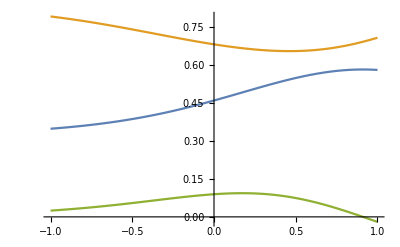

```mathematica
Plot[{XMnΓ[1,t,1,0],PMnΓ[1,t,1,0],DMnΓ[1,t,1,0]},{t,-1,1},PlotRange->All]
```

```mathematica
Jl[L_]:=KroneckerProduct[{{0,1},{-1,0}},IdentityMatrix[L]];
```

```mathematica
Jl[2]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
Ω[tot_]:=SparseArray[{{x_,y_}/;x-y==-1&&OddQ[x]-> 1,{x_,y_}/;x-y==1&&OddQ[y]->-1},{2tot,2tot}]//Normal;
```

```mathematica
Ω[2]//MatrixForm
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
XmnΓtabRex[ΓQ_,x_,ξI_,L_]:=XmnΓtabRex[ΓQ,x,ξI,L]=Module[{XmntabC},
XmntabC=Table[XmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];XmntabC]
```

```mathematica
PmnΓtabRex[ΓQ_,x_,ξI_,L_]:=PmnΓtabRex[ΓQ,x,ξI,L]=Module[{PmntabC},
PmntabC=Table[PmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];PmntabC]
```

```mathematica
DmnΓtabRex[ΓQ_,x_,ξI_,L_]:=DmnΓtabRex[ΓQ,x,ξI,L]=Module[{DmntabC},
DmntabC=Table[DmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];DmntabC]
```

```mathematica
(*Nice!*)
```

```mathematica
(*CmnΓtabRex3 is the correct thing to use.*)
```

```mathematica
ToeXMnΓ[ΓQ_, x_, ξI_, L_]:=ToeXMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[XMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
ToePMnΓ[ΓQ_, x_, ξI_, L_]:=ToePMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[PMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
ToeDMnΓ[ΓQ_, x_, ξI_, L_]:=ToeDMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[DMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
CmnΓtabRex3[ΓQ_,x_,ξI_,L_]:=ArrayFlatten[{{ToeXMnΓ[ΓQ,x,ξI,L],ToeDMnΓ[ΓQ,x,ξI,L]},{ToeDMnΓ[ΓQ,x,ξI,L],ToePMnΓ[ΓQ,x,ξI,L]}}];
```

CoP as a Function of Subsystem Separation (Fixed Subsystem Size)

CoP as a Function of Subsystem Size (0 Separation)

CoP as a Function of Subsystem Size (Variable Separation)

CoP in the Continuum Limit?